# Alg AG4

```mathematica
getSol[chromosome_]:=
Module[{chromosomes=chromosome},
curLimits={α,β};
currentX=Table[0,muchii];
currentSol=0;
Do[
parents=SparseArray[chromosomes⟦2,source⟧[[All,2]]->chromosomes⟦2,source⟧[[All,1]]];
curFlow=Table[0,noduri];
Do[
minVal=Min[{curLimits⟦1,source⟧,curLimits⟦2,dest⟧}];
curFlow⟦noduri-n+dest⟧+=minVal;
curLimits⟦1,source⟧-=minVal;
curLimits⟦2,dest⟧-=minVal;
,{dest,chromosomes⟦4⟧}];

DepthFirstScan[chromosomes⟦2,source⟧,source,"PostvisitVertex"->(
If[#≠source,
edgeId=pos⟦parents⟦#⟧*noduri+#⟧;
curFlow⟦parents⟦#⟧⟧+=curFlow⟦#⟧;
currentX⟦edgeId⟧+=curFlow⟦#⟧;
]&)];
,{source,chromosomes⟦3⟧}];
currentX
]
```

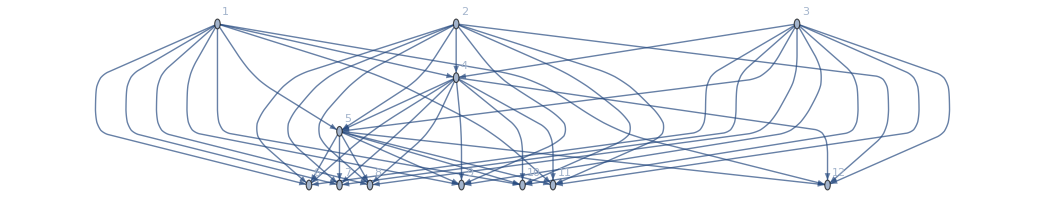

{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12,2->4,2->5,2->6,2->7,2->8,2->9,2->10,2->11,2->12,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->11,3->12,4->5,4->6,4->7,4->8,4->9,4->10,4->11,4->12,5->6,5->7,5->8,5->9,5->10,5->11,5->12}

42

SparseArray[…]

{{0},{0},{0},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}}

{19,12,19}

{5,5,20,13,1,5,1}

{2,2,1,1,2,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,2,1,2,2,2,2,1,1,2,1,2,1,1,2,1,1,2,1,1}

```mathematica
m=3;
n=7;
H=50;
(*Crearea unui graf cu m surse, n destinatii si noduri-m-n noduri intermediare*)
(*In acest graft exista drum din fiecare sursa in fiecare destinatie*)
noduri=12;
g= Graph[
Table[i,{i,noduri}],
DeleteDuplicates@Flatten[Table[
Join[
{source->m+1},
Table[source->j,{j,RandomSample[Range[m+2,noduri]]}],
Flatten[Table[i->j,{i,m+1,noduri-n-1},{j,RandomSample[Range[i+2,noduri-n],RandomInteger[noduri-i-n-1]]}]],
Table[i->i+1,{i,m+1,noduri-1-n}],
Flatten[Table[i->j,{j,noduri-n+1,noduri},{i,RandomSample[Range[m+1,noduri-n],RandomInteger[{1,noduri-n-m}]]}]]
],{source,m}]],
VertexLabels->Automatic
]
val=Sort[EdgeList[g]] (*care arce sunt in graf*)
muchii=EdgeCount[g] (*numarul de arce*)

M=muchii;
pos = SparseArray[MapIndexed[#⟦1⟧*noduri+#⟦2⟧->#2⟦1⟧&,val]] (*Se creaza un hastable pentru a accesa pozitia unei muchii*)

(*Lista nodurilor parinti pentru fiecare nod*)
adjList=Join[Table[{0},m],Sort[Gather[val,#1[[2]]==#2[[2]]&],#1[[1,2]]<#2[[1,2]]&][[All,All,1]]]



α=Differences[Flatten[{0,Sort[RandomSample[Range[H-1],m-1]],H}]]
β=Differences[Flatten[{0,Sort[RandomSample[Range[H-1],n-1]],H}]]


(*Se creaza functiile concave de cost*)
foo=Table[RandomInteger[Range[1,2]],M]
bar=foo;
f[j_,x_]:=Piecewise[{{foo⟦j⟧ x, x≤bar⟦j⟧}, {foo⟦j⟧ bar⟦j⟧, x>bar⟦j⟧}, {0, True}}]
```

```mathematica
Do[
Print[Style["Test ","Section"],Style[bigCount,"Section"]];
thisTimer=Timing[
(*Variabile necesare pentru algoritm*)
nrIteratii=10;

(*Se afla nodurile in care se poate ajunge din sursa i*)
subtrees=Table[VertexList@FindSpanningTree[{g,i}],{i,m}];

Print["------------------------------------------------------------------"];
Print["Virfurile ce pot fi atinse din fiecare sursa  ",subtrees];
(*Se creaza populatia intiala. Fiecare cromozom va fi format din {valoarea functiei, arborii din fiecare sursa, ordinea surselor, ordinea destinatiilor, ordinea transporturilor, ordinea produselor}*)
Print["------------------------------------------------------------------"];
Print["Populatia initiala"];
chromosomes=Table[
{
0,
Table[Table[RandomChoice[Intersection[adjList⟦i⟧,subtrees⟦j⟧]]->i,{i,Drop[subtrees⟦j⟧,1]}],{j,m}],
RandomSample[Range[m]],
RandomSample[Range[n]]
}
,4*noduri];
Print[chromosomes];
(*Se gaseste solutiile asociate fiecarui cromozom si functiile lor obiectiv*)
Do[
(*Maximul de flux care poate fi trimis din fiecare sursa, destinatie, transport, produs*)
curLimits={α,β};
(*Solutia cromozomului i*)
currentX=Table[0,muchii];
currentSol=0;
(*Fiecare arbore este evaluat aparte*)
Do[
(*Arborele este reprezentat ca un hashmap dintre nodul copil si nodul parinte*)
parents=SparseArray[chromosomes⟦i,2,source⟧[[All,2]]->chromosomes⟦i,2,source⟧[[All,1]]];
(*Se calculeaza fluxul care trebuie impins din destinatii catre sursa*)
curFlow=Table[0,noduri];
Do[
(*Se afla marimea fluxului care poate fi impins din source catre dest cu produsul k si transportul l*)
minVal=Min[{curLimits⟦1,source⟧,curLimits⟦2,dest⟧}];
curFlow⟦noduri-n+dest⟧+=minVal;
curLimits⟦1,source⟧-=minVal;
curLimits⟦2,dest⟧-=minVal;
,{dest,chromosomes⟦i,4⟧}];
(*Printr-un depth first search se impinge fluxul din destinatii catre sursa*)
DepthFirstScan[chromosomes⟦i,2,source⟧,source,"PostvisitVertex"->(
If[#≠source,
(*Se afla pozitia muchiei*)
edgeId=pos⟦parents⟦#⟧*noduri+#⟧;
(*Tot fluxul din nodul curent este impins catre parinte si solutia acestui cromozom este actualizata*)
curFlow⟦parents⟦#⟧⟧+=curFlow⟦#⟧;
currentX⟦edgeId⟧+=curFlow⟦#⟧;
]&)];
,{source,chromosomes⟦i,3⟧}];
(*Se afla valoarea funtiei obiectiv*)
chromosomes⟦i,1⟧=Sum[f[j,currentX⟦j⟧],{j,muchii}];
,{i,4*noduri}];
chromosomes=Sort[chromosomes];


Do[
Print["------------------------------------------------------------------"];
Print["Iteratia ",iteratia];
(*Sunt alesi cei mai buni parinti*)

chromosomes=Take[chromosomes,2*noduri];

(*Se creaza urmasii si urmatoarea populatie*)
chromosomes=Join[
(*Parintii nu sunt schimbati*)
chromosomes,

Print["Parintii si Urmasii"];
Flatten[Table[
(*Urmasii sunt creati prin impartirea aleatoarea a arborilor din cromozomii-parinti*)
(*Celelalte valori sunt luate de la ambii parinti*)

randPos=RandomInteger[{1,m-1}];
{
{0,Join[chromosomes⟦i,2,;;randPos⟧,chromosomes⟦i+1,2,randPos+1;;⟧],chromosomes⟦i,3⟧,chromosomes⟦i+1,4⟧},
{0,Join[chromosomes⟦i+1,2,;;randPos⟧,chromosomes⟦i,2,randPos+1;;⟧],chromosomes⟦i+1,3⟧,chromosomes⟦i,4⟧}
}
,{i,1,2*noduri,2}],1]];
(*Pentru fiecare lista de ordini din fiecare cromozom-copil mutatia se produce cu sansa de 50%*)
Do[
If[RandomInteger[100]≤50,
(*Doua pozitii sunt alese aleator si schimbate cu locurile*)
{it1,it2}=RandomSample[Range[Length@chromosomes⟦i⟧⟦j⟧],2];
chromosomes⟦i⟧⟦j⟧⟦{it1,it2}⟧=chromosomes⟦i⟧⟦j⟧⟦{it2,it1}⟧
];
,{i,2*noduri+1,4*noduri},{j,3,4}];
Print[chromosomes];
(*Se evalueaza cromozomii-copii*)
Do[
curLimits={α,β};
currentX=Table[0,muchii];
currentSol=0;
Do[
parents=SparseArray[chromosomes⟦i,2,source⟧[[All,2]]->chromosomes⟦i,2,source⟧[[All,1]]];
curFlow=Table[0,noduri];
Do[
minVal=Min[{curLimits⟦1,source⟧,curLimits⟦2,dest⟧}];
curFlow⟦noduri-n+dest⟧+=minVal;
curLimits⟦1,source⟧-=minVal;
curLimits⟦2,dest⟧-=minVal;
,{dest,chromosomes⟦i,4⟧}];
DepthFirstScan[chromosomes⟦i,2,source⟧,source,"PostvisitVertex"->(
If[#≠source,
edgeId=pos⟦parents⟦#⟧*noduri+#⟧;
curFlow⟦parents⟦#⟧⟧+=curFlow⟦#⟧;
currentX⟦edgeId⟧+=curFlow⟦#⟧;
]&)];
,{source,chromosomes⟦i,3⟧}];
chromosomes⟦i,1⟧=Sum[f[j,currentX⟦j⟧],{j,muchii}];
,{i,2*noduri+1,4*noduri}];

Print["Populatia noua "];
chromosomes=Sort[chromosomes];

Print[chromosomes];
Print["Cromozom cu cele mai bune caracteristici ",chromosomes⟦1⟧];
Print["Solutia cea mai buna ",getSol[chromosomes⟦1⟧]];
Print["Funtia obiectiv totala  ",Total@chromosomes⟦All,1⟧];
,{iteratia,nrIteratii}];];
Print[thisTimer];
,{bigCount,10}]
```

Test 1

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{3,4,5,6,7,8,9,10,11,12}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,4->6,1->7,4->8,5->9,4->10,4->11,1->12},{2->4,4->5,5->6,5->7,2->8,4->9,2->10,4->11,5->12},{3->4,3->5,3->6,5->7,4->8,3->9,4->10,3->11,3->12}},{3,2,1},{5,4,1,2,3,6,7}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,3->12}},{2,3,1},{2,6,4,5,3,7,1}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,7,6,1,2,4,5}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{0,{{1->4,4->5,5->6,5->7,5->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{1,6,3,7,4,5,2}},{0,{{1->4,1->5,4->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,4->10,5->11,4->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,4->11,4->12}},{2,1,3},{4,6,3,5,1,2,7}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,2->10,2->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{5,4,2,3,7,1,6}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,4->10,5->11,5->12},{2->4,2->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,5->7,4->8,4->9,4->10,3->11,4->12}},{2,1,3},{4,5,3,7,2,1,6}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,5,4,7,6}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,5,7,3,6,2,4}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,1->11,4->12},{2->4,4->5,4->6,2->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,3->6,5->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{3,2,6,4,5,7,1}},{0,{{1->4,1->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,5->9,5->10,2->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,5->10,4->11,3->12}},{2,1,3},{3,4,1,7,2,6,5}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,5->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,3->11,3->12}},{2,3,1},{7,3,1,4,5,6,2}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,2->11,2->12},{3->4,4->5,5->6,5->7,4->8,3->9,5->10,5->11,4->12}},{2,1,3},{2,5,6,4,3,1,7}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,2,1}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,2,1,7,3,4,6}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{2,1,3},{1,5,2,7,6,4,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{4,6,2,7,5,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{1,3,2},{7,2,1,6,5,4,3}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,5->8,4->9,5->10,5->11,3->12}},{3,1,2},{1,3,2,4,6,5,7}},{0,{{1->4,1->5,5->6,4->7,1->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,4->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,3->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,4,3,1,6,2,5}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,2,3},{7,5,3,1,2,6,4}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,3->9,5->10,5->11,3->12}},{3,2,1},{1,6,2,4,5,7,3}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,3->11,5->12}},{1,3,2},{2,3,5,7,1,6,4}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,5->7,4->8,4->9,5->10,2->11,4->12},{3->4,4->5,5->6,3->7,5->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,5,4,6,1,2,7}},{0,{{1->4,4->5,4->6,5->7,1->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,4->8,5->9,5->10,3->11,5->12}},{1,2,3},{6,1,5,2,4,3,7}},{0,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,5->7,2->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{7,5,4,6,3,2,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{4,6,7,2,5,1,3}},{0,{{1->4,4->5,5->6,4->7,1->8,5->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,5->8,4->9,4->10,5->11,5->12},{3->4,3->5,3->6,5->7,3->8,4->9,5->10,3->11,3->12}},{1,3,2},{7,2,1,5,3,6,4}},{0,{{1->4,4->5,1->6,5->7,1->8,4->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{5,7,3,1,4,2,6}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,4->9,5->10,4->11,5->12}},{2,1,3},{4,6,5,3,1,7,2}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,2->9,2->10,5->11,5->12},{3->4,3->5,4->6,5->7,5->8,4->9,5->10,4->11,3->12}},{3,1,2},{4,6,5,3,2,7,1}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,4->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,3->8,4->9,5->10,5->11,4->12}},{2,1,3},{6,4,2,3,7,1,5}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,3->11,3->12}},{3,1,2},{2,6,1,4,7,3,5}},{0,{{1->4,4->5,1->6,5->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,2->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,3->8,5->9,4->10,5->11,5->12}},{1,2,3},{1,7,2,6,3,4,5}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,4->10,4->11,4->12},{2->4,4->5,4->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{2,1,3},{7,5,1,3,4,2,6}},{0,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{0,{{1->4,4->5,4->6,5->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,3->7,5->8,3->9,3->10,5->11,4->12}},{2,1,3},{5,7,2,1,3,4,6}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,4->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{1,3,2},{3,5,7,1,4,6,2}},{0,{{1->4,4->5,1->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,3->6,3->7,4->8,3->9,5->10,3->11,4->12}},{1,2,3},{1,3,4,2,5,7,6}},{0,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{1,3,2,7,5,4,6}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,3,1,4,7,2,5}},{0,{{1->4,1->5,5->6,5->7,4->8,5->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,4->10,4->11,5->12}},{2,3,1},{1,6,2,3,7,4,5}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{1,2,3},{4,6,3,5,1,7,2}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{19,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{20,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{4,6,7,2,5,1,3}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,5,7,3,6,2,4}},{22,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{1,3,2,7,5,4,6}},{22,{{1->4,1->5,5->6,1->7,1->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{2,1,3},{1,5,2,7,6,4,3}},{22,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{23,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{4,6,2,7,5,1,3}},{23,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,3->11,5->12}},{1,3,2},{2,3,5,7,1,6,4}},{23,{{1->4,4->5,5->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,2,1}},{24,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,3->11,3->12}},{3,1,2},{2,6,1,4,7,3,5}},{24,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{1,3,2},{7,2,1,6,5,4,3}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,2,1,7,3,4,6}},{24,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{1,2,3},{4,6,3,5,1,7,2}},{24,{{1->4,4->5,1->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,3->6,3->7,4->8,3->9,5->10,3->11,4->12}},{1,2,3},{1,3,4,2,5,7,6}},{24,{{1->4,4->5,1->6,5->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,2->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,3->8,5->9,4->10,5->11,5->12}},{1,2,3},{1,7,2,6,3,4,5}},{25,{{1->4,1->5,1->6,5->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,3->9,5->10,5->11,3->12}},{3,2,1},{1,6,2,4,5,7,3}},{25,{{1->4,1->5,4->6,5->7,4->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,7,6,1,2,4,5}},{25,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,5->7,2->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{7,5,4,6,3,2,1}},{26,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,2,3},{7,5,3,1,2,6,4}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,2,3},{1,5,6,3,4,2,7}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{5,2,4,3,7,6,1}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,2,3},{3,4,1,6,5,2,7}},{0,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{5,6,7,4,1,3,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,3,2},{1,2,6,5,4,7,3}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,1,3},{1,7,4,2,3,6,5}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{3,1,2},{1,5,7,4,6,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{0,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{3,2,1},{1,5,2,6,7,4,3}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,3,2,4,5,7,6}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,1,3},{4,6,2,1,5,7,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,2,1}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{2,3,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{3,1,2},{7,5,1,6,2,4,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,3->11,3->12}},{1,3,2},{2,6,1,4,7,3,5}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{4,6,3,2,1,7,5}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,2,1,7,3,4,6}},{0,{{1->4,4->5,1->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,5->6,4->7,3->8,5->9,4->10,5->11,5->12}},{1,2,3},{1,7,6,2,3,4,5}},{0,{{1->4,4->5,1->6,5->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,2->8,5->9,2->10,4->11,2->12},{3->4,4->5,3->6,3->7,4->8,3->9,5->10,3->11,4->12}},{1,2,3},{1,3,4,2,5,7,6}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{3,1,2},{1,7,6,3,2,4,5}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,3->9,5->10,5->11,3->12}},{2,3,1},{2,6,1,4,5,7,3}},{0,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,5->7,2->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{2,3,1},{7,5,3,1,2,6,4}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{7,5,4,2,3,6,1}}}

Populatia noua

{{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,2,1,7,3,4,6}},{19,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{7,5,4,2,3,6,1}},{20,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{4,6,7,2,5,1,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{4,6,3,2,1,7,5}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,5,7,3,6,2,4}},{22,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{1,3,2,7,5,4,6}},{22,{{1->4,1->5,5->6,1->7,1->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{2,1,3},{1,5,2,7,6,4,3}},{22,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{23,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{4,6,2,7,5,1,3}},{23,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{5,6,7,4,1,3,2}},{23,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,3->11,5->12}},{1,3,2},{2,3,5,7,1,6,4}},{23,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,5->7,2->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{2,3,1},{7,5,3,1,2,6,4}},{23,{{1->4,4->5,5->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,2,1}},{24,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,3->11,3->12}},{3,1,2},{2,6,1,4,7,3,5}},{24,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{3,2,1},{1,5,2,6,7,4,3}},{24,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{1,3,2},{7,2,1,6,5,4,3}},{24,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,2,1,7,3,4,6}},{24,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{1,2,3},{4,6,3,5,1,7,2}},{24,{{1->4,4->5,1->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,3->6,3->7,4->8,3->9,5->10,3->11,4->12}},{1,2,3},{1,3,4,2,5,7,6}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,1,3},{4,6,2,1,5,7,3}},{24,{{1->4,4->5,1->6,5->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,2->8,5->9,2->10,4->11,2->12},{3->4,4->5,3->6,3->7,4->8,3->9,5->10,3->11,4->12}},{1,2,3},{1,3,4,2,5,7,6}},{24,{{1->4,4->5,1->6,5->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,2->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,3->8,5->9,4->10,5->11,5->12}},{1,2,3},{1,7,2,6,3,4,5}},{25,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{3,1,2},{7,5,1,6,2,4,3}},{25,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,2,3},{1,5,6,3,4,2,7}},{25,{{1->4,1->5,1->6,5->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,3->9,5->10,5->11,3->12}},{3,2,1},{1,6,2,4,5,7,3}},{25,{{1->4,1->5,4->6,5->7,4->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,7,6,1,2,4,5}},{25,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,3->11,3->12}},{1,3,2},{2,6,1,4,7,3,5}},{25,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,2,3},{3,4,1,6,5,2,7}},{25,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,2,1}},{25,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,5->7,2->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{7,5,4,6,3,2,1}},{26,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,2,3},{7,5,3,1,2,6,4}},{26,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{5,2,4,3,7,6,1}},{26,{{1->4,1->5,4->6,5->7,4->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,3->9,5->10,5->11,3->12}},{2,3,1},{2,6,1,4,5,7,3}},{27,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{3,1,2},{1,5,7,4,6,2,3}},{28,{{1->4,4->5,1->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,5->6,4->7,3->8,5->9,4->10,5->11,5->12}},{1,2,3},{1,7,6,2,3,4,5}},{29,{{1->4,1->5,5->6,1->7,1->8,1->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,3,2,4,5,7,6}},{30,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,1,3},{1,7,4,2,3,6,5}},{30,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,3,2},{1,2,6,5,4,7,3}},{30,{{1->4,4->5,5->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{2,3,5,7,1,6,4}},{34,{{1->4,1->5,1->6,5->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{3,1,2},{1,7,6,3,2,4,5}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}}

Solutia cea mai buna {6,0,0,0,0,13,0,0,0,12,0,0,0,0,0,0,0,0,0,10,0,0,8,0,0,0,1,0,0,5,12,0,1,0,0,5,0,0,0,0,5,0}

Funtia obiectiv totala  1129

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,2,1,7,3,4,6}},{19,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{7,5,4,2,3,6,1}},{20,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{4,6,7,2,5,1,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{4,6,3,2,1,7,5}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,5,7,3,6,2,4}},{22,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{1,3,2,7,5,4,6}},{22,{{1->4,1->5,5->6,1->7,1->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{2,1,3},{1,5,2,7,6,4,3}},{22,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{23,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{4,6,2,7,5,1,3}},{23,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{5,6,7,4,1,3,2}},{23,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,3->11,5->12}},{1,3,2},{2,3,5,7,1,6,4}},{23,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,5->7,2->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{2,3,1},{7,5,3,1,2,6,4}},{23,{{1->4,4->5,5->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,2,1}},{24,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,3->11,3->12}},{3,1,2},{2,6,1,4,7,3,5}},{24,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{3,2,1},{1,5,2,6,7,4,3}},{24,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{1,3,2},{7,2,1,6,5,4,3}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,2,5,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{5,6,7,4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{2,1,3},{3,4,1,6,5,2,7}},{0,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{3,1,2},{5,2,1,7,3,4,6}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{1,2,3},{1,7,6,2,3,4,5}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,2,3},{1,7,4,6,3,2,5}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,2,3},{1,2,3,5,7,4,6}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{2,1,3},{7,5,4,2,3,6,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,1,2},{4,6,3,2,7,1,5}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,3,2,7,5,4,6}},{0,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{2,1,3},{1,5,7,3,6,4,2}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,3,1},{2,7,6,1,3,4,5}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{2,1,3},{1,5,2,7,6,4,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{3,6,7,4,1,5,2}},{0,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,1,2},{4,6,1,7,5,2,3}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,3,2},{7,5,3,1,2,4,6}},{0,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{2,3,5,7,1,6,4}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,3->11,3->12}},{1,3,2},{2,6,1,4,7,3,5}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{0,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{3,2,1},{7,2,4,6,5,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{1,3,2},{1,5,2,6,7,4,3}}}

Populatia noua

{{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,2,1,7,3,4,6}},{19,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,2,3},{1,2,3,5,7,4,6}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{7,5,4,2,3,6,1}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,2,5,1,3}},{20,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{4,6,7,2,5,1,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{4,6,3,2,1,7,5}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,5,7,3,6,2,4}},{21,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{2,1,3},{1,5,7,3,6,4,2}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,1,2},{4,6,3,2,7,1,5}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,1,3}},{21,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{22,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{5,6,7,4,3,1,2}},{22,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{3,2,1},{7,2,4,6,5,1,3}},{22,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{1,3,2,7,5,4,6}},{22,{{1->4,1->5,5->6,1->7,1->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{2,1,3},{1,5,2,7,6,4,3}},{22,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{23,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{4,6,2,7,5,1,3}},{23,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{5,6,7,4,1,3,2}},{23,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{2,1,3},{1,5,2,7,6,4,3}},{23,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,3->11,5->12}},{1,3,2},{2,3,5,7,1,6,4}},{23,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,5->7,2->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{2,3,1},{7,5,3,1,2,6,4}},{23,{{1->4,4->5,5->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,2,1}},{24,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,3,2,7,5,4,6}},{24,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,3->11,3->12}},{3,1,2},{2,6,1,4,7,3,5}},{24,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{3,1,2},{5,2,1,7,3,4,6}},{24,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{3,2,1},{1,5,2,6,7,4,3}},{24,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{1,3,2},{7,2,1,6,5,4,3}},{25,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,2,3},{1,7,4,6,3,2,5}},{25,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{2,1,3},{7,5,4,2,3,6,1}},{25,{{1->4,1->5,5->6,1->7,1->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,3,1},{2,7,6,1,3,4,5}},{26,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{3,6,7,4,1,5,2}},{26,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,1,2},{4,6,1,7,5,2,3}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,5->10,3->11,5->12}},{1,3,2},{1,5,2,6,7,4,3}},{26,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{2,1,3},{3,4,1,6,5,2,7}},{26,{{1->4,4->5,5->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,3->11,3->12}},{1,3,2},{2,6,1,4,7,3,5}},{27,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{1,2,3},{1,7,6,2,3,4,5}},{27,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,3,2},{7,5,3,1,2,4,6}},{33,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{2,3,5,7,1,6,4}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}}

Solutia cea mai buna {6,0,0,0,0,13,0,0,0,12,0,0,0,0,0,0,0,0,0,10,0,0,8,0,0,0,1,0,0,5,12,0,1,0,0,5,0,0,0,0,5,0}

Funtia obiectiv totala  1064

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,2,1,7,3,4,6}},{19,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,2,3},{1,2,3,5,7,4,6}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{7,5,4,2,3,6,1}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,2,5,1,3}},{20,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{4,6,7,2,5,1,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{4,6,3,2,1,7,5}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,5,7,3,6,2,4}},{21,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{2,1,3},{1,5,7,3,6,4,2}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,1,2},{4,6,3,2,7,1,5}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,1,3}},{21,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{22,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{5,6,7,4,3,1,2}},{22,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{3,2,1},{7,2,4,6,5,1,3}},{22,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{1,3,2,7,5,4,6}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,1,3},{1,2,4,3,5,6,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{5,6,7,2,4,1,3}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{5,6,7,4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,2,3},{7,5,6,3,4,2,1}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,2,3},{3,4,1,2,5,6,7}},{0,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{3,1,2},{5,6,1,7,3,4,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{1,3,2},{2,7,6,1,3,4,5}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{3,1,2},{1,7,4,2,3,6,5}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,7,4,2,3,6,1}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,5,4,7,6}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{3,2,1},{1,2,3,5,4,7,6}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{7,6,4,2,5,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,1,3},{4,6,3,2,1,7,5}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,3,7,5,6,4,2}},{0,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{2,1,3},{1,5,7,3,6,2,4}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{4,6,7,2,5,3,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,2,1},{7,6,3,2,4,1,5}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,3,1,6}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,5,6,3,4,2,7}},{0,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{1,3,2,7,5,4,6}},{0,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{1,3,2},{7,2,4,6,5,1,3}}}

Populatia noua

{{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,3,1,6}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,2,1,7,3,4,6}},{19,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,3,7,5,6,4,2}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,7,4,2,3,6,1}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,2,3},{1,2,3,5,7,4,6}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{7,5,4,2,3,6,1}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{3,2,1},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,2,5,1,3}},{20,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,5,6,3,4,2,7}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{4,6,7,2,5,1,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{4,6,3,2,1,7,5}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,2,1},{7,6,3,2,4,1,5}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,5,7,3,6,2,4}},{21,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{3,1,2},{1,7,4,2,3,6,5}},{21,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{2,1,3},{1,5,7,3,6,2,4}},{21,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{2,1,3},{1,5,7,3,6,4,2}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,1,2},{4,6,3,2,7,1,5}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,1,3}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,1,3}},{21,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{22,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{5,6,7,4,3,1,2}},{22,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{5,6,7,4,3,1,2}},{22,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{3,2,1},{7,2,4,6,5,1,3}},{22,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{1,3,2,7,5,4,6}},{23,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{5,6,7,2,4,1,3}},{23,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,1,3},{1,2,4,3,5,6,7}},{24,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{7,6,4,2,5,1,3}},{25,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,5,4,7,6}},{25,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{4,6,7,2,5,3,1}},{25,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,2,3},{3,4,1,2,5,6,7}},{27,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{3,1,2},{5,6,1,7,3,4,2}},{27,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{1,3,2,7,5,4,6}},{28,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,1,3},{4,6,3,2,1,7,5}},{29,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{1,3,2},{2,7,6,1,3,4,5}},{29,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,2,3},{7,5,6,3,4,2,1}},{31,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{1,3,2},{7,2,4,6,5,1,3}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}}

Solutia cea mai buna {6,0,0,0,0,13,0,0,0,12,0,0,0,0,0,0,0,0,0,10,0,0,8,0,0,0,1,0,0,5,12,0,1,0,0,5,0,0,0,0,5,0}

Funtia obiectiv totala  1024

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,3,1,6}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,2,1,7,3,4,6}},{19,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,3,7,5,6,4,2}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,7,4,2,3,6,1}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,2,3},{1,2,3,5,7,4,6}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{7,5,4,2,3,6,1}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{3,2,1},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,2,5,1,3}},{20,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,5,6,3,4,2,7}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{4,6,7,2,5,1,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{4,6,3,2,1,7,5}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,2,1},{7,6,3,2,4,1,5}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{1,2,4,3,7,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{5,2,4,3,7,6,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,3,1,2,7,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,1,2},{6,4,5,7,3,2,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{4,2,7,5,3,1,6}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,5,6,3,4,2,7}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,3,4,6}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,6,7,4,3,1,2}},{0,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,1,3},{1,7,4,2,3,6,5}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,2,3},{3,4,1,5,6,2,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{1,3,2},{2,7,6,1,3,4,5}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{2,1,3},{1,3,7,5,6,4,2}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,3,2},{1,2,3,5,7,4,6}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,7,4,2,3,6,1}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,2,3},{1,2,3,5,4,7,6}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{2,3,1},{7,5,4,2,3,6,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{3,2,1},{1,2,3,5,4,7,6}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,5,2,1,3}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,5,4,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,1,2},{4,6,3,2,1,5,7}}}

Populatia noua

{{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,5,4,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,3,1,6}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,2,1,7,3,4,6}},{19,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{1,2,4,3,7,6,5}},{19,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{3,2,1},{1,2,3,5,4,7,6}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,3,7,5,6,4,2}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,7,4,2,3,6,1}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,2,3},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,2,3},{1,2,3,5,7,4,6}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{7,5,4,2,3,6,1}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{3,2,1},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,2,5,1,3}},{20,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,5,6,3,4,2,7}},{20,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,5,2,1,3}},{20,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{4,6,7,2,5,1,3}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{4,6,3,2,1,7,5}},{20,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,2,1},{7,6,3,2,4,1,5}},{20,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,5,6,3,4,2,7}},{21,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{2,1,3},{1,3,7,5,6,4,2}},{22,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,7,4,2,3,6,1}},{22,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,6,7,4,3,1,2}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,1,2},{6,4,5,7,3,2,1}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,3,1,2,7,6,4}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{5,2,4,3,7,6,1}},{23,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{4,2,7,5,3,1,6}},{23,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,3,4,6}},{25,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{1,3,2},{2,7,6,1,3,4,5}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,2,3},{3,4,1,5,6,2,7}},{26,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,3,2},{1,2,3,5,7,4,6}},{26,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{2,3,1},{7,5,4,2,3,6,1}},{27,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,1,2},{4,6,3,2,1,5,7}},{31,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,1,3},{1,7,4,2,3,6,5}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}}

Solutia cea mai buna {0,1,5,0,0,13,0,0,0,6,0,0,5,0,0,0,0,1,0,0,0,0,19,0,0,0,0,0,0,0,1,0,0,5,0,0,0,0,0,1,0,0}

Funtia obiectiv totala  975

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,5,4,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,3,1,6}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,2,1,7,3,4,6}},{19,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{1,2,4,3,7,6,5}},{19,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{3,2,1},{1,2,3,5,4,7,6}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,3,7,5,6,4,2}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,7,4,2,3,6,1}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,2,3},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,2,3},{1,2,3,5,7,4,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{7,2,4,3,5,6,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{3,6,7,2,5,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{5,6,7,2,4,1,3}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{1,2,4,3,7,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,2,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,1,3},{5,2,1,7,3,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,1,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,6,3,4,2,7}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,1,3},{7,3,6,5,4,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,6,3,4,2,7}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,2,4,3,1,7}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,1,3,6}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,2,1},{3,4,1,6,5,2,7}},{0,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,3,2},{5,3,1,7,2,4,6}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{3,2,1},{1,2,3,5,4,7,6}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{1,2,4,3,7,6,5}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,3,7,6,5,4,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{2,3,1},{5,1,4,2,3,6,7}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{1,2,3},{2,3,6,1,7,4,5}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,4,7,5,6}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,3,2},{1,5,3,2,4,7,6}}}

Populatia noua

{{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,5,4,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,3,1,6}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,2,4,3,1,7}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,2,1,7,3,4,6}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,2,1},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{5,6,7,2,4,1,3}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,1,2}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{7,2,4,3,5,6,1}},{19,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{1,2,4,3,7,6,5}},{19,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{1,2,4,3,7,6,5}},{19,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{3,2,1},{1,2,3,5,4,7,6}},{19,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{3,2,1},{1,2,3,5,4,7,6}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{19,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,1,3,6}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,3,7,5,6,4,2}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{2,1,3},{2,7,6,1,3,4,5}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,7,4,2,3,6,1}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,2,3},{1,2,3,5,4,7,6}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,2,3},{1,2,3,5,7,4,6}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,3,7,6,5,4,2}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,1,3},{5,2,1,7,3,6,4}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,2,1}},{21,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,5->12}},{2,3,1},{5,1,4,2,3,6,7}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,6,3,4,2,7}},{22,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{1,3,2},{1,5,3,2,4,7,6}},{22,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,5->10,5->11,5->12}},{2,1,3},{1,2,3,4,7,5,6}},{22,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,3,2},{5,3,1,7,2,4,6}},{24,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{1,2,4,3,7,6,5}},{25,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,1,3}},{25,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,2->6,4->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{1,2,3},{2,3,6,1,7,4,5}},{26,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{3,6,7,2,5,1,4}},{29,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,1,3},{7,3,6,5,4,1,2}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}}

Solutia cea mai buna {0,1,5,0,0,13,0,0,0,6,0,0,5,0,0,0,0,1,0,0,0,0,19,0,0,0,0,0,0,0,1,0,0,5,0,0,0,0,0,1,0,0}

Funtia obiectiv totala  936

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,5,4,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,3,1,6}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,2,4,3,1,7}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,2,1,7,3,4,6}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,2,1},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{5,6,7,2,4,1,3}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,1,2}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{7,2,4,3,5,6,1}},{19,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{5,2,4,3,7,6,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{5,6,7,3,4,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{1,2,4,3,5,6,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,7,3,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{1,7,4,2,5,6,3}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,7,5,2,3,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{2,5,6,3,4,1,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,2,1}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,6,3,1,2,7}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,2,7,4,3,1,6}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,2,1},{7,6,3,5,4,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,6,2,4,3,1,7}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,2,1},{4,3,1,6,5,2,7}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{3,1,2},{5,2,1,7,3,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{5,4,6,7,3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{5,6,7,2,4,1,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,2,3},{3,4,1,6,5,2,7}},{0,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{1,2,4,3,5,6,7}}}

Populatia noua

{{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,6,3,1,2,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{5,2,4,3,7,6,1}},{17,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{1,7,4,2,5,6,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,5,4,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,3,1,6}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,2,4,3,1,7}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,2,1,7,3,4,6}},{18,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,2,1},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{5,6,7,2,4,1,3}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{5,4,6,7,3,1,2}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,1,2}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,2,1}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{7,2,4,3,5,6,1}},{19,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,1,2},{3,4,1,6,5,2,7}},{19,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{5,6,7,2,4,1,3}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,1,3}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{21,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{2,5,6,3,4,1,7}},{21,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,2,1},{7,6,3,5,4,1,2}},{21,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{3,2,1},{4,3,1,6,5,2,7}},{22,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,7,3,1,6,4}},{22,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{1,2,4,3,5,6,7}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,7,5,2,3,4,1}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{5,6,7,3,4,1,2}},{23,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,6,2,4,3,1,7}},{23,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,5->11,5->12}},{3,1,2},{5,2,1,7,3,4,6}},{26,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,5->8,4->9,5->10,5->11,5->12}},{1,2,3},{3,4,1,6,5,2,7}},{26,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{1,2,4,3,5,6,7}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,2,7,4,3,1,6}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,6,3,1,2,7}}

Solutia cea mai buna {0,0,0,0,0,13,1,5,0,1,1,5,5,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,19,0,0,0,1}

Funtia obiectiv totala  925

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,6,3,1,2,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{5,2,4,3,7,6,1}},{17,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{1,7,4,2,5,6,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,5,4,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,3,1,6}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,2,4,3,1,7}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{2,6,7,3,5,1,4}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,5,6,3,1,2,7}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{1,2,4,3,7,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,1,3},{1,7,4,2,3,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{5,4,7,2,6,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,4,3,7,6,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{5,2,1,4,7,6,3}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,1,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,1,2},{6,4,5,7,3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{1,7,4,2,5,6,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,1,2,5,7,4}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,2,4,3,7}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{1,5,6,3,4,2,7}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,4,5,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{2,1,3},{6,5,2,4,3,1,7}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,3,1,6}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}}}

Populatia noua

{{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,6,3,1,2,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{5,2,4,3,7,6,1}},{17,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{1,7,4,2,5,6,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,5,6,3,1,2,7}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{1,7,4,2,5,6,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,5,4,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,3,1,6}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,2,7,4,3,1,6}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,2,4,3,1,7}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{18,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,6,7,4,3,1,2}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{5,2,1,4,7,6,3}},{19,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{1,2,4,3,7,6,5}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{5,4,7,2,6,1,3}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,1,2,5,7,4}},{21,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,1,2,3}},{22,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,1,2},{6,4,5,7,3,1,2}},{22,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,3,1}},{22,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,2,4,3,7}},{23,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{1,5,6,3,4,2,7}},{24,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,4,3,7,6,1}},{25,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{25,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,4->12}},{2,1,3},{6,5,2,4,3,1,7}},{27,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{2,6,7,3,5,1,4}},{29,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,4,5,1,2}},{30,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,1,3},{1,7,4,2,3,6,5}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,6,3,1,2,7}}

Solutia cea mai buna {0,0,0,0,0,13,1,5,0,1,1,5,5,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,19,0,0,0,1}

Funtia obiectiv totala  924

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,6,3,1,2,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{5,2,4,3,7,6,1}},{17,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{1,7,4,2,5,6,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,5,6,3,1,2,7}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{1,7,4,2,5,6,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,5,4,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{3,6,7,2,5,1,4}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,5,6,3,1,2,7}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{1,2,4,7,3,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,1,3},{5,1,6,3,4,2,7}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{5,6,7,2,4,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,1,3},{1,7,4,2,3,6,5}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,4,6,7,3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,3,7,2,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,2,5,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,3,7,5,2,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,2,3},{2,7,4,1,5,6,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,5,6,2,1,3,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,7,2,5,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{3,2,1},{1,7,4,2,5,6,3}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{1,5,6,3,4,2,7}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,4,6,3,5,2,7}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,1,2},{5,6,3,7,4,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,3,6,4,2,7}}}

Populatia noua

{{12,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,3,6,4,2,7}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,6,3,1,2,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,7,2,5,1,4}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,2,5,1,3}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{5,2,4,3,7,6,1}},{17,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,4,6,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{1,7,4,2,5,6,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,5,6,3,1,2,7}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,5,6,3,1,2,7}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{1,7,4,2,5,6,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,5,4,1,2}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,3,7,2,1}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,5,6,2,1,3,7}},{20,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,1,3},{5,1,6,3,4,2,7}},{21,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{3,2,1},{1,7,4,2,5,6,3}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{5,6,7,2,4,1,3}},{22,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,2,3},{2,7,4,1,5,6,3}},{22,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{3,6,7,2,5,1,4}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,1,3},{1,7,4,2,3,6,5}},{23,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{1,5,6,3,4,2,7}},{25,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,3,7,5,2,1}},{26,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,4,6,3,5,2,7}},{29,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{1,2,4,7,3,6,5}},{30,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,5->9,3->10,4->11,4->12}},{3,1,2},{5,6,3,7,4,1,2}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,3,6,4,2,7}}

Solutia cea mai buna {1,0,0,5,0,13,0,0,0,6,0,5,0,0,0,1,0,0,0,19,0,0,0,0,0,0,0,0,0,0,6,0,0,0,1,0,0,14,0,0,5,0}

Funtia obiectiv totala  901

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{12,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,3,6,4,2,7}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,6,3,1,2,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,7,2,5,1,4}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,2,5,1,3}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{5,2,4,3,7,6,1}},{17,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,4,6,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{1,7,4,2,5,6,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,5,6,3,2,1,7}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,2,3},{1,5,3,6,4,2,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{4,2,5,3,7,6,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{5,6,7,2,3,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{3,6,7,2,5,1,4}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{1,2,4,3,7,6,5}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,5,6,3,4,2,7}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{5,6,7,2,3,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,2,3},{1,7,6,2,3,4,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{5,2,4,3,7,6,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{1,5,6,3,4,2,7}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{5,4,6,7,3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,2,3,7,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,2,3,1,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,7,5,3,2,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,4,3,1,6,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{5,2,4,3,7,1,6}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{6,4,1,2,3,7,5}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,2,3},{1,5,4,2,7,6,3}}}

Populatia noua

{{12,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,3,6,4,2,7}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{1,5,6,3,4,2,7}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,6,3,1,2,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{4,2,5,3,7,6,1}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,7,2,5,1,4}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,5,6,3,2,1,7}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,2,5,1,3}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{5,2,4,3,7,6,1}},{17,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,4,6,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,4,3,7,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{1,7,4,2,5,6,3}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{5,6,7,2,3,1,4}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,2,3,7,1}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{6,4,1,2,3,7,5}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,2,3,1,7}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,7,5,3,2,1}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,2,3},{1,5,4,2,7,6,3}},{20,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,5,6,3,4,2,7}},{20,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{5,4,6,7,3,1,2}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,2,3},{1,5,3,6,4,2,7}},{22,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,2,3},{1,7,6,2,3,4,5}},{22,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{1,2,4,3,7,6,5}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{5,2,4,3,7,1,6}},{23,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{5,2,4,3,7,6,1}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{5,6,7,2,3,1,4}},{24,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,4,3,1,6,7}},{25,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{3,6,7,2,5,1,4}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,3,6,4,2,7}}

Solutia cea mai buna {1,0,0,5,0,13,0,0,0,6,0,5,0,0,0,1,0,0,0,19,0,0,0,0,0,0,0,0,0,0,6,0,0,0,1,0,0,14,0,0,5,0}

Funtia obiectiv totala  871

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{12,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,3,6,4,2,7}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{1,5,6,3,4,2,7}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,6,3,1,2,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{4,2,5,3,7,6,1}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,7,2,5,1,4}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,5,6,3,2,1,7}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,2,5,1,3}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{5,2,4,3,7,6,1}},{17,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,4,6,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,6,3,4,2,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{1,5,3,6,4,2,7}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,7,2,5,1,4}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,5,3,6,1,2,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,4,3,7,6,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{4,2,3,5,7,6,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,7,2,5,1,4}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{1,2,4,3,7,6,5}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,2,6,3,4,5,7}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{5,6,7,3,4,1,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{3,1,2},{1,5,4,2,3,6,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,6,3,2,1,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,1,3,4,6,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{6,4,7,2,5,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,1,3,7,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{5,2,1,3,7,6,4}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,3,7,1}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{5,2,1,3,7,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{5,4,6,7,3,2,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,1,2}}}

Populatia noua

{{12,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,3,6,4,2,7}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{1,5,6,3,4,2,7}},{14,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,6,3,1,2,7}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{3,6,7,2,5,1,4}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,5,3,6,1,2,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{4,2,5,3,7,6,1}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{5,2,1,3,7,6,4}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,4,3,7,6,1}},{15,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,6,3,4,2,7}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{1,2,4,3,7,6,5}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,7,2,5,1,4}},{16,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,1,3},{5,6,7,2,4,1,3}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{16,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,5,6,3,2,1,7}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{6,4,5,7,3,1,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,7,3,1,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{1,7,4,2,3,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{4,6,7,2,5,1,3}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,1,3,7,6,4}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{1,5,6,3,4,2,7}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,2,1},{1,5,3,6,4,2,7}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{5,2,4,3,7,6,1}},{17,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{17,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,7,2,5,1,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,4,6,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{6,4,5,7,3,2,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{6,4,5,7,3,1,2}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,3,2},{4,6,7,2,5,1,3}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,2,3},{5,2,1,3,4,6,7}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,3,7,1}},{18,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12}},{3,1,2},{1,5,4,2,3,6,7}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{2,3,1},{4,6,7,2,5,1,3}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,2,1},{6,4,7,2,5,1,3}},{21,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,2,6,3,4,5,7}},{21,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,1,2},{5,2,1,3,7,6,4}},{22,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{5,4,6,7,3,2,1}},{22,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,2,1,3,7,6,4}},{22,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{1,2,4,3,7,6,5}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,6,3,2,1,7}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,2->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,5,6,3,4,2,7}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{1,2,3},{5,6,7,3,4,1,2}},{24,{{1->4,1->5,1->6,1->7,5->8,1->9,5->10,5->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,2,4,3,7,6,1}},{25,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{4,2,3,5,7,6,1}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,4->5,1->6,1->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,3,6,4,2,7}}

Solutia cea mai buna {1,0,0,5,0,13,0,0,0,6,0,5,0,0,0,1,0,0,0,19,0,0,0,0,0,0,0,0,0,0,6,0,0,0,1,0,0,14,0,0,5,0}

Funtia obiectiv totala  857

{0.53125,Null}

Test 2

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{3,4,5,6,7,8,9,10,11,12}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{3,4,7,5,1,6,2}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,2,1},{7,4,6,5,3,2,1}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{4,5,7,6,2,1,3}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,4->11,4->12},{2->4,2->5,4->6,2->7,4->8,5->9,4->10,2->11,5->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{1,4,3,6,5,7,2}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,1->10,5->11,1->12},{2->4,4->5,2->6,5->7,4->8,4->9,2->10,5->11,5->12},{3->4,4->5,4->6,5->7,4->8,5->9,4->10,5->11,5->12}},{3,1,2},{5,2,3,4,7,6,1}},{0,{{1->4,4->5,1->6,5->7,1->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,3->10,5->11,5->12}},{2,3,1},{4,3,7,1,6,2,5}},{0,{{1->4,4->5,4->6,4->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,2->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,3->12}},{3,2,1},{1,7,4,2,3,5,6}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,2->5,4->6,2->7,5->8,4->9,4->10,2->11,5->12},{3->4,4->5,4->6,4->7,4->8,5->9,3->10,5->11,5->12}},{3,1,2},{4,7,6,2,5,3,1}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,4->10,4->11,3->12}},{2,3,1},{5,2,6,1,4,3,7}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{2,1,3},{5,3,2,1,6,7,4}},{0,{{1->4,1->5,4->6,1->7,4->8,5->9,4->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,5->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{4,1,5,2,6,7,3}},{0,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{4,6,1,3,2,5,7}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,2->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,1,3},{2,5,6,4,7,3,1}},{0,{{1->4,4->5,1->6,1->7,4->8,4->9,4->10,4->11,4->12},{2->4,2->5,4->6,5->7,4->8,5->9,4->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,3->9,3->10,5->11,5->12}},{1,3,2},{1,6,5,2,4,7,3}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{5,4,1,7,6,2,3}},{0,{{1->4,1->5,4->6,5->7,5->8,4->9,1->10,5->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{3,2,1},{4,6,5,7,1,2,3}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,4->11,4->12}},{2,3,1},{2,6,1,3,4,5,7}},{0,{{1->4,4->5,5->6,4->7,5->8,4->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,5->10,3->11,4->12}},{3,1,2},{5,4,7,1,3,6,2}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{1,2,3},{4,7,1,3,6,2,5}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,5->11,4->12},{3->4,3->5,3->6,5->7,4->8,3->9,4->10,5->11,5->12}},{3,1,2},{4,5,2,1,3,6,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,4->10,4->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,2->11,5->12},{3->4,4->5,4->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,3,1},{7,2,4,5,6,3,1}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,3->6,5->7,4->8,3->9,4->10,3->11,5->12}},{1,3,2},{5,2,1,6,3,4,7}},{0,{{1->4,4->5,4->6,4->7,1->8,4->9,4->10,5->11,4->12},{2->4,2->5,5->6,4->7,2->8,5->9,2->10,2->11,5->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,3->11,3->12}},{1,2,3},{3,7,2,5,4,1,6}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{0,{{1->4,4->5,4->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,4->6,2->7,5->8,5->9,5->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,5->11,3->12}},{1,2,3},{3,2,6,4,5,1,7}},{0,{{1->4,1->5,4->6,4->7,5->8,5->9,1->10,5->11,1->12},{2->4,4->5,4->6,2->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,3->6,5->7,4->8,3->9,5->10,3->11,4->12}},{2,1,3},{4,6,2,3,7,5,1}},{0,{{1->4,4->5,1->6,5->7,1->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,3->10,3->11,4->12}},{2,1,3},{6,2,4,3,7,1,5}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,7,1,2,6,5,3}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{2,3,1},{7,5,2,1,3,4,6}},{0,{{1->4,4->5,1->6,1->7,4->8,5->9,4->10,4->11,4->12},{2->4,4->5,4->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,3->6,4->7,4->8,3->9,3->10,3->11,3->12}},{2,3,1},{7,6,1,2,4,5,3}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,5->12},{2->4,2->5,2->6,5->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{3,1,2},{4,2,5,7,6,1,3}},{0,{{1->4,1->5,4->6,1->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,2->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,5->11,4->12}},{3,1,2},{2,3,7,1,4,5,6}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,3->12}},{1,2,3},{1,2,4,6,3,5,7}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,5->9,4->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,4->12}},{1,2,3},{4,6,2,5,3,1,7}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,4,2,3,6,5,7}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,4->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{7,5,1,2,3,4,6}},{0,{{1->4,4->5,4->6,4->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,5->7,2->8,5->9,2->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,3->9,3->10,3->11,3->12}},{1,2,3},{7,3,6,2,1,4,5}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,2->7,2->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,5->11,5->12}},{1,3,2},{5,1,7,2,4,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,7,2,5}},{0,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,1,6,5,3,4,2}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,2,1,6,3,5,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{2,6,3,4,5,1,7}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,3->11,3->12}},{3,1,2},{6,1,2,7,4,5,3}},{0,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,1,2},{6,4,3,7,2,5,1}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,3->11,4->12}},{1,2,3},{2,1,4,6,5,3,7}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,5->10,5->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,2->11,2->12},{3->4,4->5,5->6,4->7,3->8,5->9,3->10,4->11,3->12}},{1,2,3},{2,6,4,5,7,3,1}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,3->8,5->9,4->10,4->11,4->12}},{3,1,2},{4,2,7,6,3,1,5}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{2,6,3,4,5,1,7}},{20,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,2,1,6,3,5,4}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{2,3,1},{7,5,2,1,3,4,6}},{21,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,7,2,5}},{21,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,1,2},{6,4,3,7,2,5,1}},{21,{{1->4,4->5,1->6,5->7,1->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,3->10,3->11,4->12}},{2,1,3},{6,2,4,3,7,1,5}},{21,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,3->8,5->9,4->10,4->11,4->12}},{3,1,2},{4,2,7,6,3,1,5}},{21,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{1,2,3},{4,7,1,3,6,2,5}},{22,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,2,1},{7,4,6,5,3,2,1}},{22,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,1,6,5,3,4,2}},{22,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{3,4,7,5,1,6,2}},{22,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{23,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{5,4,1,7,6,2,3}},{23,{{1->4,1->5,4->6,5->7,5->8,4->9,1->10,5->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{3,2,1},{4,6,5,7,1,2,3}},{23,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,2->5,4->6,2->7,5->8,4->9,4->10,2->11,5->12},{3->4,4->5,4->6,4->7,4->8,5->9,3->10,5->11,5->12}},{3,1,2},{4,7,6,2,5,3,1}},{23,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,3->11,4->12}},{1,2,3},{2,1,4,6,5,3,7}},{23,{{1->4,4->5,1->6,1->7,5->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,2->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,1,3},{2,5,6,4,7,3,1}},{23,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{2,1,3},{5,3,2,1,6,7,4}},{23,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{4,5,7,6,2,1,3}},{23,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{4,6,1,3,2,5,7}},{23,{{1->4,4->5,4->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,4->6,2->7,5->8,5->9,5->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,5->11,3->12}},{1,2,3},{3,2,6,4,5,1,7}},{24,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,7,1,2,6,5,3}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,4->10,4->11,3->12}},{2,3,1},{5,2,6,1,4,3,7}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,3,4,2,1,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{3,1,2},{7,5,2,1,3,4,6}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{2,3,1},{6,4,3,7,5,2,1}},{0,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{3,1,2},{6,1,3,4,7,2,5}},{0,{{1->4,4->5,1->6,5->7,1->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,3->8,5->9,4->10,4->11,4->12}},{2,1,3},{4,2,7,6,3,1,5}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,3->10,3->11,4->12}},{2,1,3},{6,2,4,3,7,1,5}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{1,3,2},{7,4,6,5,3,2,1}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{3,2,1},{4,5,1,3,6,2,7}},{0,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{4,3,7,5,1,6,2}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,3,6,5,1,4,2}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{5,4,1,7,6,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{0,{{1->4,1->5,4->6,5->7,5->8,4->9,1->10,5->11,1->12},{2->4,2->5,4->6,2->7,5->8,4->9,4->10,2->11,5->12},{3->4,4->5,4->6,4->7,4->8,5->9,3->10,5->11,5->12}},{1,2,3},{2,7,6,4,5,3,1}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,1,3},{7,6,5,4,1,2,3}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{1,2,3},{5,2,6,4,7,3,1}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,2->9,4->10,5->11,4->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,3->11,4->12}},{3,1,2},{2,1,4,6,5,7,3}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{4,5,2,6,7,1,3}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{1,2,3},{7,3,2,1,6,5,4}},{0,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,5->8,5->9,5->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,5->11,3->12}},{3,2,1},{3,2,7,4,5,1,6}},{0,{{1->4,4->5,4->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{1,6,4,3,2,5,7}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,4->10,4->11,3->12}},{2,3,1},{5,2,6,1,4,3,7}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10,1->11,4->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,7,1,2,6,5,3}}}

Populatia noua

{{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{2,6,3,4,5,1,7}},{20,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,1,3},{7,6,5,4,1,2,3}},{20,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,2,1,6,3,5,4}},{20,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{1,2,3},{7,3,2,1,6,5,4}},{20,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{5,4,1,7,6,2,3}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{2,3,1},{7,5,2,1,3,4,6}},{21,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,7,2,5}},{21,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{21,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,1,2},{6,4,3,7,2,5,1}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{1,2,3},{5,2,6,4,7,3,1}},{21,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,3,6,5,1,4,2}},{21,{{1->4,4->5,1->6,5->7,1->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,3->10,3->11,4->12}},{2,1,3},{6,2,4,3,7,1,5}},{21,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,3->8,5->9,4->10,4->11,4->12}},{3,1,2},{4,2,7,6,3,1,5}},{21,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,3,4,2,1,7}},{21,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{1,2,3},{4,7,1,3,6,2,5}},{22,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{2,3,1},{6,4,3,7,5,2,1}},{22,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,2,1},{7,4,6,5,3,2,1}},{22,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,1,6,5,3,4,2}},{22,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{4,3,7,5,1,6,2}},{22,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{3,4,7,5,1,6,2}},{22,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{23,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{5,4,1,7,6,2,3}},{23,{{1->4,1->5,4->6,5->7,5->8,4->9,1->10,5->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{3,2,1},{4,6,5,7,1,2,3}},{23,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,2->5,4->6,2->7,5->8,4->9,4->10,2->11,5->12},{3->4,4->5,4->6,4->7,4->8,5->9,3->10,5->11,5->12}},{3,1,2},{4,7,6,2,5,3,1}},{23,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,3->11,4->12}},{1,2,3},{2,1,4,6,5,3,7}},{23,{{1->4,4->5,1->6,1->7,5->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,2->9,4->10,5->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,1,3},{2,5,6,4,7,3,1}},{23,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{3,1,2},{7,5,2,1,3,4,6}},{23,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{2,1,3},{5,3,2,1,6,7,4}},{23,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{4,5,7,6,2,1,3}},{23,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,2->7,5->8,5->9,5->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,5->11,3->12}},{3,2,1},{3,2,7,4,5,1,6}},{23,{{1->4,4->5,4->6,4->7,4->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{4,6,1,3,2,5,7}},{23,{{1->4,4->5,4->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,4->6,2->7,5->8,5->9,5->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,5->11,3->12}},{1,2,3},{3,2,6,4,5,1,7}},{23,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{1,3,2},{7,4,6,5,3,2,1}},{24,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,4->10,4->11,3->12}},{2,3,1},{5,2,6,1,4,3,7}},{24,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,7,1,2,6,5,3}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,4->10,4->11,3->12}},{2,3,1},{5,2,6,1,4,3,7}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10,1->11,4->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,7,1,2,6,5,3}},{25,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{3,1,2},{6,1,3,4,7,2,5}},{26,{{1->4,4->5,1->6,1->7,5->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,2->9,4->10,5->11,4->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,3->11,4->12}},{3,1,2},{2,1,4,6,5,7,3}},{28,{{1->4,1->5,4->6,5->7,5->8,4->9,1->10,5->11,1->12},{2->4,2->5,4->6,2->7,5->8,4->9,4->10,2->11,5->12},{3->4,4->5,4->6,4->7,4->8,5->9,3->10,5->11,5->12}},{1,2,3},{2,7,6,4,5,3,1}},{28,{{1->4,4->5,1->6,5->7,1->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,3->8,5->9,4->10,4->11,4->12}},{2,1,3},{4,2,7,6,3,1,5}},{28,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,3->10,3->11,4->12}},{2,1,3},{6,2,4,3,7,1,5}},{28,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{4,5,2,6,7,1,3}},{28,{{1->4,4->5,4->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{1,6,4,3,2,5,7}},{31,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{3,2,1},{4,5,1,3,6,2,7}}}

Cromozom cu cele mai bune caracteristici {16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}}

Solutia cea mai buna {0,1,0,5,0,13,0,0,0,0,0,0,0,12,0,0,0,0,1,13,5,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,8,0,1,5,0}

Funtia obiectiv totala  1085

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{2,6,3,4,5,1,7}},{20,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,1,3},{7,6,5,4,1,2,3}},{20,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,2,1,6,3,5,4}},{20,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{1,2,3},{7,3,2,1,6,5,4}},{20,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{5,4,1,7,6,2,3}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{2,3,1},{7,5,2,1,3,4,6}},{21,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,7,2,5}},{21,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{21,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,1,2},{6,4,3,7,2,5,1}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{1,2,3},{5,2,6,4,7,3,1}},{21,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,3,6,5,1,4,2}},{21,{{1->4,4->5,1->6,5->7,1->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,3->10,3->11,4->12}},{2,1,3},{6,2,4,3,7,1,5}},{21,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,3->8,5->9,4->10,4->11,4->12}},{3,1,2},{4,2,7,6,3,1,5}},{21,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,3,4,2,1,7}},{21,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{1,2,3},{4,7,1,3,6,2,5}},{22,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{2,3,1},{6,4,3,7,5,2,1}},{22,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,2,1},{7,4,6,5,3,2,1}},{22,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,1,6,5,3,4,2}},{22,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{4,3,7,5,1,6,2}},{22,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{3,4,7,5,1,6,2}},{22,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,3,1,6,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{2,7,3,4,5,1,6}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,2,1,6,3,5,4}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,3,1},{7,6,5,2,1,4,3}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{1,2,3},{5,4,1,7,6,2,3}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{2,3,1},{5,3,2,1,6,7,4}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{2,3,1},{6,1,3,4,7,2,5}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{2,3,1},{7,5,2,1,3,4,6}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,2,1},{3,4,6,7,2,5,1}},{0,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{2,1,3},{2,3,7,6,5,4,1}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,3,6,5,1,4,2}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,1,3},{6,2,5,4,7,3,1}},{0,{{1->4,4->5,1->6,5->7,1->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,5->9,4->10,4->11,4->12}},{2,1,3},{4,2,1,6,3,7,5}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,3->10,3->11,4->12}},{3,1,2},{6,2,4,3,7,5,1}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,7,1,3,6,2,4}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{5,6,4,3,2,1,7}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{2,3,1},{7,4,6,5,3,2,1}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,2,1},{6,5,3,7,4,2,1}},{0,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{4,3,7,5,1,6,2}},{0,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{1,2,3},{7,1,6,5,3,4,2}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{1,2,3},{1,7,3,6,5,4,2}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{3,4,1,5,7,6,2}}}

Populatia noua

{{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,7,1,3,6,2,4}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{5,6,4,3,2,1,7}},{18,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{2,3,1},{7,4,6,5,3,2,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,3,1,6,4,2}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{2,6,3,4,5,1,7}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{1,2,3},{1,7,3,6,5,4,2}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,2,1},{3,4,6,7,2,5,1}},{20,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,1,3},{7,6,5,4,1,2,3}},{20,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,3,6,5,1,4,2}},{20,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,2,1,6,3,5,4}},{20,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,3,1},{7,6,5,2,1,4,3}},{20,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{1,2,3},{7,3,2,1,6,5,4}},{20,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{5,4,1,7,6,2,3}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{2,3,1},{7,5,2,1,3,4,6}},{21,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,7,2,5}},{21,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{21,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,1,2},{6,4,3,7,2,5,1}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{1,2,3},{5,2,6,4,7,3,1}},{21,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,3,6,5,1,4,2}},{21,{{1->4,4->5,1->6,5->7,1->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,5->8,5->9,3->10,3->11,4->12}},{2,1,3},{6,2,4,3,7,1,5}},{21,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,3->8,5->9,4->10,4->11,4->12}},{3,1,2},{4,2,7,6,3,1,5}},{21,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,3,4,2,1,7}},{21,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{1,2,3},{4,7,1,3,6,2,5}},{22,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{2,3,1},{6,4,3,7,5,2,1}},{22,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,2,1},{7,4,6,5,3,2,1}},{22,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,1,6,5,3,4,2}},{22,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{4,3,7,5,1,6,2}},{22,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{3,4,7,5,1,6,2}},{22,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{22,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{2,7,3,4,5,1,6}},{22,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{2,3,1},{6,1,3,4,7,2,5}},{23,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{1,2,3},{5,4,1,7,6,2,3}},{24,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{2,3,1},{7,5,2,1,3,4,6}},{25,{{1->4,1->5,1->6,1->7,1->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,2,1},{6,5,3,7,4,2,1}},{25,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{4,3,7,5,1,6,2}},{25,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{2,3,1},{5,3,2,1,6,7,4}},{25,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,4->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{3,4,1,5,7,6,2}},{26,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{2,1,3},{2,3,7,6,5,4,1}},{27,{{1->4,4->5,1->6,5->7,1->8,1->9,5->10,1->11,5->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,5->9,4->10,4->11,4->12}},{2,1,3},{4,2,1,6,3,7,5}},{27,{{1->4,4->5,1->6,5->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,5->8,5->9,3->10,3->11,4->12}},{3,1,2},{6,2,4,3,7,5,1}},{28,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,2,1,6,3,5,4}},{28,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,1,3},{6,2,5,4,7,3,1}},{29,{{1->4,1->5,4->6,4->7,1->8,5->9,4->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{1,2,3},{7,1,6,5,3,4,2}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}}

Solutia cea mai buna {0,13,0,5,0,1,0,0,0,0,12,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,20,12,1,5,1}

Funtia obiectiv totala  1028

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,7,1,3,6,2,4}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{5,6,4,3,2,1,7}},{18,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{2,3,1},{7,4,6,5,3,2,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,3,1,6,4,2}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{2,6,3,4,5,1,7}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{1,2,3},{1,7,3,6,5,4,2}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,2,1},{3,4,6,7,2,5,1}},{20,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,1,3},{7,6,5,4,1,2,3}},{20,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,3,6,5,1,4,2}},{20,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,2,1,6,3,5,4}},{20,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,3,1},{7,6,5,2,1,4,3}},{20,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{1,2,3},{7,3,2,1,6,5,4}},{20,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{5,4,1,7,6,2,3}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{2,3,1},{7,5,2,1,3,4,6}},{21,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,7,2,5}},{21,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{21,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,1,2},{6,4,3,7,2,5,1}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{1,2,3},{5,2,6,4,7,3,1}},{21,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,3,6,5,1,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,3,1,7,6,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{3,5,7,1,6,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,2,1},{7,6,4,5,3,2,1}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{2,5,3,4,6,1,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,3,1,6,5,2,4}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{2,1,3},{1,4,6,7,2,5,3}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,1,2},{2,7,3,6,5,4,1}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{1,2,3},{3,7,6,5,1,4,2}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,1,3},{7,6,5,4,1,2,3}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{7,6,5,2,1,4,3}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,2,1,6,3,5,4}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{1,2,3},{5,4,1,3,6,2,7}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{1,2,3},{4,3,2,1,6,5,7}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,5,2,7}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{3,1,2},{7,5,2,1,6,4,3}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,6,3,7,2,5,1}},{0,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,6,5,1,4,2}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{1,2,3},{5,2,6,4,7,1,3}}}

Populatia noua

{{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,3,1,6,5,2,4}},{17,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{7,6,5,2,1,4,3}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,7,1,3,6,2,4}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{5,6,4,3,2,1,7}},{18,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{2,3,1},{7,4,6,5,3,2,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,1,3,4,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,3,1,6,4,2}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,5,2,7}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,2,1},{7,6,4,5,3,2,1}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{2,6,3,4,5,1,7}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{2,1,3},{1,4,6,7,2,5,3}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{1,2,3},{1,7,3,6,5,4,2}},{19,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,2,1,6,3,5,4}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,2,1},{3,4,6,7,2,5,1}},{20,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{20,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,1,3},{7,6,5,4,1,2,3}},{20,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,3,6,5,1,4,2}},{20,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,2,1,6,3,5,4}},{20,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,3,1},{7,6,5,2,1,4,3}},{20,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{1,2,3},{7,3,2,1,6,5,4}},{20,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{5,4,1,7,6,2,3}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{2,3,1},{7,5,2,1,3,4,6}},{21,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,7,2,5}},{21,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{21,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,1,2},{6,4,3,7,2,5,1}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{1,2,3},{5,2,6,4,7,3,1}},{21,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,4->10,5->11,3->12}},{1,2,3},{5,2,6,4,7,1,3}},{21,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,3,6,5,1,4,2}},{22,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{3,5,7,1,6,4,2}},{22,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,6,3,7,2,5,1}},{22,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,1,2},{2,7,3,6,5,4,1}},{22,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{1,2,3},{3,7,6,5,1,4,2}},{22,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,6,5,1,4,2}},{22,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,3,1,7,6,2,4}},{23,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{2,5,3,4,6,1,7}},{24,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,5->12}},{1,2,3},{4,3,2,1,6,5,7}},{26,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,5->10,4->11,3->12}},{3,1,2},{7,5,2,1,6,4,3}},{26,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{1,2,3},{5,4,1,3,6,2,7}},{28,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,1,3},{7,6,5,4,1,2,3}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}}

Solutia cea mai buna {0,1,0,5,0,13,0,0,0,5,0,5,0,0,0,1,0,1,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,20,0,0,0,0}

Funtia obiectiv totala  942

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,3,1,6,5,2,4}},{17,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{7,6,5,2,1,4,3}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,7,1,3,6,2,4}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{5,6,4,3,2,1,7}},{18,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{2,3,1},{7,4,6,5,3,2,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,1,3,4,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,3,1,6,4,2}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,5,2,7}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,2,1},{7,6,4,5,3,2,1}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{2,6,3,4,5,1,7}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{2,1,3},{1,4,6,7,2,5,3}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{1,2,3},{1,7,3,6,5,4,2}},{19,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,2,1,6,3,5,4}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,2,1},{3,4,6,7,2,5,1}},{20,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,3,6,1,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,5,1,6,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{7,3,1,6,5,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,2,3,4,1}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{3,1,2},{5,7,1,3,6,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{3,2,1},{7,6,1,2,5,4,3}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,2,1,3,4,6}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{3,6,4,5,2,1,7}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,5,6,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,1,2},{7,4,5,6,3,2,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{7,5,1,6,3,2,4}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,4,1,6,3,2}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{1,3,2},{7,4,6,5,3,2,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{3,2,1},{6,1,3,4,5,2,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,2,1},{1,4,6,7,2,5,3}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{6,2,3,4,5,1,7}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,2,1,6,3,5,4}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{2,1,3},{1,7,3,5,6,4,2}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,1,2},{1,3,7,6,5,4,2}},{0,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,2,1},{4,3,6,7,2,5,1}}}

Populatia noua

{{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,2,3,4,1}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{16,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,3,1,6,5,2,4}},{17,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{7,6,5,2,1,4,3}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,7,1,3,6,2,4}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{5,6,4,3,2,1,7}},{18,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{2,3,1},{7,4,6,5,3,2,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,1,3,4,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,3,1,6,4,2}},{18,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{6,2,3,4,5,1,7}},{18,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,3,6,1,2,4}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,5,2,7}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,2,1},{7,6,4,5,3,2,1}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{2,6,3,4,5,1,7}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{2,1,3},{1,4,6,7,2,5,3}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{1,2,3},{1,7,3,6,5,4,2}},{19,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,2,1,6,3,5,4}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,2,1},{3,4,6,7,2,5,1}},{20,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,2,1},{1,3,7,6,5,4,2}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,1,2},{7,4,5,6,3,2,1}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{3,2,1},{6,1,3,4,5,2,7}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{7,3,1,6,5,2,4}},{21,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,5,6,1,3,4,2}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{7,5,1,6,3,2,4}},{21,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{3,1,2},{5,7,1,3,6,2,4}},{21,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,5,1,6,3,2,4}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{1,3,2},{7,4,6,5,3,2,1}},{22,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,2,1,6,3,5,4}},{22,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{3,2,1},{7,6,1,2,5,4,3}},{23,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,2,1},{1,4,6,7,2,5,3}},{23,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{2,1,3},{1,7,3,5,6,4,2}},{23,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,2,1,3,4,6}},{25,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,4,1,6,3,2}},{27,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,3->9,4->10,3->11,4->12}},{3,1,2},{1,3,7,6,5,4,2}},{27,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{3,6,4,5,2,1,7}},{28,{{1->4,1->5,4->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,4->10,3->11,4->12}},{3,2,1},{4,3,6,7,2,5,1}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}}

Solutia cea mai buna {0,1,0,5,0,13,0,0,0,5,0,5,0,0,0,1,0,1,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,20,0,0,0,0}

Funtia obiectiv totala  919

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,2,3,4,1}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{16,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,3,1,6,5,2,4}},{17,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{7,6,5,2,1,4,3}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,7,1,3,6,2,4}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{5,6,4,3,2,1,7}},{18,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{2,3,1},{7,4,6,5,3,2,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,1,3,4,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,3,1,6,4,2}},{18,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{6,2,3,4,5,1,7}},{18,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,3,6,1,2,4}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,5,2,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{1,3,2},{5,3,1,6,2,4,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,2,6,5,3,4,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,6,1,5,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{6,5,2,1,3,4,7}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{1,3,2},{2,7,1,3,6,5,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{3,2,1},{7,6,5,1,2,4,3}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,5,2,1,3,4,6}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,5,2,1,3,4,6}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,1,3,4,2}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,1,2},{7,4,2,5,3,6,1}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{5,2,4,3,6,1,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,3,6,1,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,2,3,4,6,1,7}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{3,2,1},{6,1,3,4,5,2,7}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,5,1,6,3,2,4}}}

Populatia noua

{{11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{13,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{15,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{15,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,2,3,4,1}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{16,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,3,1,6,5,2,4}},{17,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{7,6,5,2,1,4,3}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,7,1,3,6,2,4}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{5,6,4,3,2,1,7}},{18,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{2,3,1},{7,4,6,5,3,2,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,1,3,4,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,1,3,4,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,6,1,5,3,4,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,3,1,6,4,2}},{18,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,1,2},{6,2,3,4,5,1,7}},{18,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,3,6,1,2,4}},{18,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,1,3,4,2}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{18,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{6,1,3,4,5,2,7}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{6,5,2,1,3,4,7}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,3,6,1,2,4}},{20,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{1,3,2},{2,7,1,3,6,5,4}},{20,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,3->10,4->11,3->12}},{3,1,2},{7,4,2,5,3,6,1}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,5,1,6,3,2,4}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,5->8,5->9,3->10,3->11,4->12}},{3,2,1},{6,1,3,4,5,2,7}},{22,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{3,2,1},{7,6,5,1,2,4,3}},{22,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,5,2,1,3,4,6}},{22,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,2,3,4,6,1,7}},{23,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,2,6,5,3,4,1}},{26,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{1,3,2},{5,3,1,6,2,4,7}},{26,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,5,2,1,3,4,6}},{29,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{5,2,4,3,6,1,7}}}

Cromozom cu cele mai bune caracteristici {11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}}

Solutia cea mai buna {0,1,0,5,0,13,0,0,0,0,11,0,0,0,0,1,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,20,0,0,5,1}

Funtia obiectiv totala  858

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{13,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{15,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{15,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,2,3,4,1}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{16,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,3,1,6,5,2,4}},{17,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{7,6,5,2,1,4,3}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,7,1,3,6,2,4}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{6,5,1,7,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,1,6,7,3,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{1,3,2},{5,6,1,3,4,2,7}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{3,5,6,1,7,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{6,5,1,7,3,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,3,6,1,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{1,2,3},{5,6,4,3,1,2,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,2,1,4,3,6}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{1,2,3},{5,1,6,3,4,2,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{3,1,2},{7,6,5,1,2,4,3}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,3,1,6,5,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,3,6,1,5,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,7,1,3,6,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,5,6,1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,1,2,3,4,6}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,1,3,2,4}}}

Populatia noua

{{9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{13,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{15,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{15,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,1,6,7,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,2,3,4,1}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{6,5,1,7,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{16,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,3,1,6,5,2,4}},{17,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{7,6,5,2,1,4,3}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,7,1,3,6,2,4}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,3,6,1,2,4}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{1,2,3},{5,6,4,3,1,2,7}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{3,5,6,1,7,4,2}},{19,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,7,1,3,6,2,4}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{6,5,1,7,3,2,4}},{21,{{1->4,4->5,1->6,4->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,3,1,6,5,2,4}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,1,3,4,2}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,4->10,3->11,4->12}},{3,1,2},{7,6,5,1,2,4,3}},{22,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{1,3,2},{5,6,1,3,4,2,7}},{22,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,1,2,3,4,6}},{22,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,1,3,2,4}},{23,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,3,6,1,5,4,2}},{24,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{1,2,3},{5,1,6,3,4,2,7}},{26,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,2,1,4,3,6}},{26,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,5,6,1,3,4,2}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,0,11,0,0,0,0,0,0,1,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,20,0,0,5,0}

Funtia obiectiv totala  823

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{13,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{15,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{15,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,1,6,7,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,2,3,4,1}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{6,5,1,7,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{16,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{2,5,6,1,3,4,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{4,3,1,6,7,2,5}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,5,1,6,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,1,6,5,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,1,6,7,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,5,2,6,3,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,6,5,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,2,1,6,3,5,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{7,5,1,6,4,2,3}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{1,5,6,2,3,4,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,2,6,3,1,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{3,6,5,1,7,4,2}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,6,4,2,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,3,1,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,4,6,1,3,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,3,1,4,2,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,5,1,7,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,2,1,7,4,6}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{5,6,1,3,4,2,7}}}

Populatia noua

{{9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{13,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,3,1,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,2,1,7,4,6}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,6,4,2,5}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,2,6,3,1,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{15,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{15,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{15,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,1,6,7,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,5,6,2,3,4,1}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{6,5,1,7,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{5,6,1,3,4,2,7}},{16,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,2,1,3,4,6}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,1,6,7,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,1,3},{5,6,1,3,4,2,7}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{7,5,1,6,4,2,3}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,5,2,6,3,1,4}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{1,5,6,2,3,4,7}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,3,1,4,2,7}},{18,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,5,1,6,3,2,4}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,4,6,1,3,5,2}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,5,1,7,3,2,4}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{4,3,1,6,7,2,5}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,6,5,3,4,2}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,1,6,5,3,4,2}},{22,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{3,6,5,1,7,4,2}},{24,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,2,1,6,3,5,4}},{24,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{2,5,6,1,3,4,7}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,0,11,0,0,0,0,0,0,1,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,20,0,0,5,0}

Funtia obiectiv totala  784

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{13,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,3,1,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,2,1,7,4,6}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,6,4,2,5}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,2,6,3,1,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{15,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{15,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{15,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,1,6,7,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,6,4,2,5}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{3,5,1,6,7,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,4,5,3,6,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,1,6,7,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,4,1,6,3,2,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,3,1,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,1,6,5,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,2,1,7,4,6}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,6,4,2,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,5,2,6,3,4,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{5,7,2,6,3,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{7,5,1,6,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,3,6,5,1,4,2}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,6,1,3,2,4}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{7,3,1,6,4,2,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{5,1,6,2,3,4,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,2,4}}}

Populatia noua

{{9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,6,4,2,5}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{13,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,3,1,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,2,1,7,4,6}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,6,4,2,5}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,6,4,2,5}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{5,7,2,6,3,1,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,2,6,3,1,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{15,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{15,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{3,5,1,6,7,2,4}},{15,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{15,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{15,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,6,1,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,1,6,7,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,1,6,7,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,2,4}},{17,{{1->4,4->5,5->6,4->7,1->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,1,3,4,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,1,6,5,3,4,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,4,1,6,3,2,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,1,2},{5,1,6,2,3,4,7}},{18,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,3,6,5,1,4,2}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,3,1,4,2}},{20,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,2,1,7,4,6}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{7,3,1,6,4,2,5}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{7,5,1,6,3,2,4}},{23,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,5,2,6,3,4,1}},{23,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,4,5,3,6,2}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,0,11,0,0,0,0,0,0,1,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,20,0,0,5,0}

Funtia obiectiv totala  746

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,6,4,2,5}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{13,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,3,1,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,2,1,7,4,6}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,6,4,2,5}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,6,4,2,5}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{5,7,2,6,3,1,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,2,6,3,1,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,4,6,1,3,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{1,3,7,6,5,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,5,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{6,1,5,7,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{2,1,6,7,3,5,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{1,5,6,3,7,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,3,6,5,1,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{2,5,3,1,7,4,6}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,3,1,6,4,2,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,5,6,2,3,4,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,3,1,6,4,2,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,2,6,3,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{5,1,2,6,3,7,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{3,5,6,1,7,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{3,5,6,1,7,4,2}}}

Populatia noua

{{9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{11,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,5,2,4}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,6,4,2,5}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{1,5,6,3,7,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{3,5,6,1,7,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{3,5,6,1,7,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{13,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{6,1,5,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,3,1,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,2,1,7,4,6}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,5->11,4->12}},{2,3,1},{5,6,1,3,2,4,7}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,2,3,4,1}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,6,4,2,5}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,6,4,2,5}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{5,1,2,6,3,7,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{5,7,2,6,3,1,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,2,6,3,1,4}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,3,6,5,1,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,3,1,6,4,2,5}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,2,6,3,1,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{1,3,7,6,5,2,4}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{17,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,1,3,4,2}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{2,1,6,7,3,5,4}},{20,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,1,3,4,2}},{20,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{2,5,3,1,7,4,6}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{7,3,1,6,4,2,5}},{22,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,4,6,1,3,5,2}},{23,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,5,6,2,3,4,1}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,0,11,0,0,0,0,0,0,1,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,20,0,0,5,0}

Funtia obiectiv totala  708

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{11,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,5,2,4}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,6,4,2,5}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{1,5,6,3,7,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{3,5,6,1,7,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{3,5,6,1,7,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{13,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{6,1,5,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,3,1,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,2,1,7,4,6}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,2,4,6,5}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,6,4,2,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{5,3,1,6,7,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,6,4,2,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,6,1,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,5,6,1,2,4,3}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{3,5,6,1,7,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,3,1,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,1,6,7,2,3,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,5,6,1,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{6,1,5,7,2,4,3}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{5,1,6,7,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,4,1,3,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,2,1,3,4,6}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,4,3,2,6}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,1,3,4,2}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,3,6,5,1,4,2}}}

Populatia noua

{{9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,6,4,2,5}},{9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{11,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,6,1,7,4,2}},{11,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,5,2,4}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,6,4,2,5}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,6,4,2,5}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{12,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{12,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{1,5,6,3,7,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{3,5,6,1,7,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{3,5,6,1,7,4,2}},{13,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{13,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,6,3,2,4}},{13,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,6,1,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{6,1,5,7,2,4,3}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{5,1,6,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{6,1,5,7,3,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,6,3,1,4,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{3,5,2,1,7,4,6}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,5,3,4,2}},{14,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,1,3,4,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{7,5,1,6,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,1,6,5,3,4,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,6,4,2,5}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{7,5,1,6,3,2,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{5,3,1,6,7,2,4}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,3,1,2,4,6,5}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,5,6,1,3,2,4}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,4,1,3,2}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,5,6,3,1,4,2}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{7,5,2,1,3,4,6}},{19,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{3,2,1},{5,1,6,7,2,3,4}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{3,5,6,1,7,4,2}},{20,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,1,3,4,2}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,5,6,1,2,4,3}},{21,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,5,6,1,3,4,2}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{5,1,6,7,3,4,2}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{7,5,1,4,3,2,6}},{23,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,3,6,5,1,4,2}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,6,4,2,5}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,0,7,5,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20,0,0,5,1}

Funtia obiectiv totala  720

{0.671875,Null}

Test 3

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{3,4,5,6,7,8,9,10,11,12}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,4->7,4->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,4->10,5->11,3->12}},{3,1,2},{4,2,5,1,7,6,3}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,4->7,5->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,3->8,3->9,3->10,5->11,5->12}},{3,1,2},{5,7,4,3,1,2,6}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{0,{{1->4,4->5,4->6,5->7,5->8,4->9,4->10,4->11,4->12},{2->4,2->5,4->6,5->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,3,2,6,5,4,1}},{0,{{1->4,1->5,4->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,4->8,4->9,2->10,5->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,3->12}},{3,2,1},{4,6,2,5,1,3,7}},{0,{{1->4,1->5,4->6,5->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,4->9,5->10,2->11,4->12},{3->4,4->5,5->6,3->7,5->8,3->9,3->10,5->11,5->12}},{3,2,1},{2,1,7,3,4,5,6}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,4->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,2->9,5->10,4->11,5->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,2,1},{4,7,3,2,1,5,6}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,5->10,4->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,2->10,2->11,4->12},{3->4,3->5,3->6,4->7,5->8,4->9,3->10,3->11,3->12}},{3,1,2},{6,1,5,3,4,2,7}},{0,{{1->4,4->5,5->6,5->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,2->8,5->9,4->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,3->9,4->10,4->11,3->12}},{3,2,1},{5,1,2,4,6,7,3}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,2->7,5->8,2->9,4->10,5->11,4->12},{3->4,4->5,3->6,4->7,4->8,4->9,3->10,4->11,4->12}},{1,2,3},{4,5,3,6,1,2,7}},{0,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,3->8,4->9,4->10,3->11,3->12}},{2,3,1},{4,2,3,5,7,6,1}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,4->9,3->10,5->11,3->12}},{1,2,3},{6,2,5,1,7,3,4}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{3,1,6,7,4,5,2}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,4->12},{3->4,3->5,3->6,5->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{2,6,5,4,3,7,1}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,5->12},{2->4,2->5,5->6,5->7,2->8,4->9,4->10,2->11,5->12},{3->4,4->5,4->6,4->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,7,1,2,5,3,6}},{0,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,4->7,3->8,4->9,5->10,4->11,4->12}},{3,2,1},{3,5,1,6,7,2,4}},{0,{{1->4,1->5,5->6,1->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,3->6,3->7,5->8,4->9,5->10,5->11,4->12}},{3,1,2},{2,4,5,3,6,1,7}},{0,{{1->4,4->5,1->6,4->7,5->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,4->12}},{3,1,2},{3,7,6,4,2,1,5}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,3->10,3->11,3->12}},{3,1,2},{3,7,4,1,5,2,6}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,4->5,3->6,3->7,5->8,4->9,4->10,3->11,5->12}},{2,3,1},{5,2,7,4,1,3,6}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,5->11,5->12},{2->4,4->5,5->6,2->7,5->8,4->9,4->10,5->11,2->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,3->11,5->12}},{3,1,2},{2,4,6,1,5,7,3}},{0,{{1->4,1->5,4->6,4->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,3->9,5->10,5->11,5->12}},{1,3,2},{7,6,2,1,3,5,4}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,5->11,4->12},{3->4,3->5,5->6,3->7,5->8,4->9,5->10,4->11,3->12}},{3,1,2},{6,2,5,4,3,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{2,1,3},{6,7,5,4,2,1,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,3->9,4->10,4->11,5->12}},{3,1,2},{6,3,2,7,4,1,5}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{1,2,3},{5,7,4,1,6,3,2}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,5->6,5->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,5->7,4->8,4->9,3->10,3->11,4->12}},{2,3,1},{2,6,4,5,1,3,7}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{3,1,2},{1,3,4,5,6,2,7}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,4->9,2->10,5->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,4->10,3->11,4->12}},{3,2,1},{6,3,7,5,4,2,1}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,1,2},{6,2,3,4,7,1,5}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,5->10,4->11,4->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,2->11,5->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,3->11,3->12}},{3,1,2},{2,6,3,1,4,5,7}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{1,3,2},{1,4,3,2,5,7,6}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,5->7,2->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,5->10,3->11,3->12}},{3,1,2},{2,5,7,1,4,6,3}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,1->10,1->11,1->12},{2->4,4->5,4->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,3->6,5->7,4->8,3->9,4->10,3->11,5->12}},{3,2,1},{7,3,2,5,1,4,6}},{0,{{1->4,4->5,4->6,4->7,4->8,5->9,4->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,1,3,7}},{0,{{1->4,1->5,4->6,1->7,1->8,4->9,1->10,1->11,1->12},{2->4,2->5,4->6,2->7,4->8,4->9,5->10,2->11,2->12},{3->4,3->5,4->6,4->7,4->8,3->9,5->10,3->11,3->12}},{3,1,2},{7,3,2,6,1,4,5}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,1,7,4,5,3,6}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{4,2,3,1,6,5,7}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,3->11,4->12}},{3,2,1},{5,3,7,2,6,1,4}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,4->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,2,1,6,7,5,4}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,4,1,6,5,2}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,5->10,4->11,4->12}},{3,2,1},{5,1,6,7,3,2,4}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,5->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,3->8,3->9,5->10,4->11,4->12}},{3,1,2},{4,3,1,2,5,7,6}},{0,{{1->4,4->5,5->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{3,1,2,5,6,7,4}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,5->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,2,6,4,3,5,7}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,1,2},{3,4,5,1,7,6,2}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{17,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,4,1,6,5,2}},{19,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{1,3,2},{1,4,3,2,5,7,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{2,1,3},{6,7,5,4,2,1,3}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{1,2,3},{5,7,4,1,6,3,2}},{20,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{3,1,6,7,4,5,2}},{21,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,1,2},{6,2,3,4,7,1,5}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,1,7,4,5,3,6}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,1,2},{3,4,5,1,7,6,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,3->9,4->10,4->11,5->12}},{3,1,2},{6,3,2,7,4,1,5}},{22,{{1->4,1->5,5->6,1->7,5->8,4->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,5->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,2,6,4,3,5,7}},{22,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,3->10,3->11,3->12}},{3,1,2},{3,7,4,1,5,2,6}},{22,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{4,2,3,1,6,5,7}},{23,{{1->4,1->5,4->6,1->7,4->8,4->9,5->10,4->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,2->10,2->11,4->12},{3->4,3->5,3->6,4->7,5->8,4->9,3->10,3->11,3->12}},{3,1,2},{6,1,5,3,4,2,7}},{23,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,5->11,4->12},{3->4,3->5,5->6,3->7,5->8,4->9,5->10,4->11,3->12}},{3,1,2},{6,2,5,4,3,7,1}},{23,{{1->4,1->5,4->6,5->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,4->9,5->10,2->11,4->12},{3->4,4->5,5->6,3->7,5->8,3->9,3->10,5->11,5->12}},{3,2,1},{2,1,7,3,4,5,6}},{23,{{1->4,4->5,4->6,4->7,4->8,5->9,4->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,1,3,7}},{24,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,3->8,4->9,4->10,3->11,3->12}},{2,3,1},{4,2,3,5,7,6,1}},{24,{{1->4,1->5,5->6,1->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,3->6,3->7,5->8,4->9,5->10,5->11,4->12}},{3,1,2},{2,4,5,3,6,1,7}},{24,{{1->4,4->5,1->6,5->7,5->8,4->9,4->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,2->9,5->10,4->11,5->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,2,1},{4,7,3,2,1,5,6}},{25,{{1->4,1->5,1->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,4->12},{3->4,3->5,3->6,5->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{2,6,5,4,3,7,1}},{25,{{1->4,1->5,1->6,5->7,1->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,3->11,4->12}},{3,2,1},{5,3,7,2,6,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,5,1,6,4,2}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{1,3,2},{6,7,5,4,2,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{3,1,2},{1,4,3,2,5,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,1,6,7,4,5,2}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{2,1,3},{5,7,4,2,6,3,1}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,1,7,4,5,3,6}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{2,3,1},{6,2,3,4,7,1,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,3->9,4->10,4->11,5->12}},{1,3,2},{6,3,2,7,4,1,5}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,3->10,3->11,3->12}},{1,3,2},{3,6,4,1,5,2,7}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,5->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{1,2,6,4,3,5,7}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,2->11,4->12},{3->4,3->5,3->6,4->7,5->8,4->9,3->10,3->11,3->12}},{3,1,2},{6,1,5,3,4,2,7}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,5->10,4->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,2->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{3,1,2},{4,5,3,1,6,2,7}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,5->7,2->8,4->9,5->10,2->11,4->12},{3->4,4->5,5->6,3->7,5->8,3->9,3->10,5->11,5->12}},{3,1,2},{2,1,7,3,4,6,5}},{0,{{1->4,1->5,4->6,5->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,5->11,4->12},{3->4,3->5,5->6,3->7,5->8,4->9,5->10,4->11,3->12}},{2,3,1},{6,2,5,4,7,3,1}},{0,{{1->4,4->5,4->6,4->7,4->8,5->9,4->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,5->12},{3->4,3->5,3->6,3->7,3->8,4->9,4->10,3->11,3->12}},{3,2,1},{4,2,3,5,7,6,1}},{0,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{4,6,5,2,1,3,7}},{0,{{1->4,1->5,5->6,1->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,1,2},{4,7,3,2,1,5,6}},{0,{{1->4,4->5,1->6,5->7,5->8,4->9,4->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,2->9,5->10,4->11,5->12},{3->4,4->5,3->6,3->7,5->8,4->9,5->10,5->11,4->12}},{3,2,1},{5,4,2,3,6,1,7}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,3->11,4->12}},{2,3,1},{5,3,7,2,6,1,4}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{2,4,5,6,3,7,1}}}

Populatia noua

{{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{17,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{18,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,1,6,7,4,5,2}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,4,1,6,5,2}},{19,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{1,3,2},{1,4,3,2,5,7,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{2,1,3},{6,7,5,4,2,1,3}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{1,2,3},{5,7,4,1,6,3,2}},{20,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{4,6,5,2,1,3,7}},{20,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{3,1,6,7,4,5,2}},{21,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,1,2},{6,2,3,4,7,1,5}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,1,7,4,5,3,6}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{2,3,1},{6,2,3,4,7,1,5}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,1,2},{3,4,5,1,7,6,2}},{22,{{1->4,1->5,1->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,3->11,4->12}},{2,3,1},{5,3,7,2,6,1,4}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,3->9,4->10,4->11,5->12}},{3,1,2},{6,3,2,7,4,1,5}},{22,{{1->4,1->5,5->6,1->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,1,2},{4,7,3,2,1,5,6}},{22,{{1->4,1->5,5->6,1->7,5->8,4->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,5->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,2,6,4,3,5,7}},{22,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,3->10,3->11,3->12}},{3,1,2},{3,7,4,1,5,2,6}},{22,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{4,2,3,1,6,5,7}},{23,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{3,1,2},{1,4,3,2,5,7,6}},{23,{{1->4,1->5,4->6,1->7,4->8,4->9,5->10,4->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,2->10,2->11,4->12},{3->4,3->5,3->6,4->7,5->8,4->9,3->10,3->11,3->12}},{3,1,2},{6,1,5,3,4,2,7}},{23,{{1->4,1->5,4->6,1->7,4->8,4->9,5->10,4->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,2->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{3,1,2},{4,5,3,1,6,2,7}},{23,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,1->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,5->11,4->12},{3->4,3->5,5->6,3->7,5->8,4->9,5->10,4->11,3->12}},{3,1,2},{6,2,5,4,3,7,1}},{23,{{1->4,1->5,4->6,5->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,5->11,4->12},{3->4,3->5,5->6,3->7,5->8,4->9,5->10,4->11,3->12}},{2,3,1},{6,2,5,4,7,3,1}},{23,{{1->4,1->5,4->6,5->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,4->9,5->10,2->11,4->12},{3->4,4->5,5->6,3->7,5->8,3->9,3->10,5->11,5->12}},{3,2,1},{2,1,7,3,4,5,6}},{23,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{1,3,2},{6,7,5,4,2,3,1}},{23,{{1->4,4->5,4->6,4->7,4->8,5->9,4->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,1,3,7}},{24,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{5,3,6,2,7,4,1}},{24,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,3->8,4->9,4->10,3->11,3->12}},{2,3,1},{4,2,3,5,7,6,1}},{24,{{1->4,1->5,5->6,1->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,3->6,3->7,5->8,4->9,5->10,5->11,4->12}},{3,1,2},{2,4,5,3,6,1,7}},{24,{{1->4,1->5,5->6,1->7,5->8,4->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,3->10,3->11,3->12}},{1,3,2},{3,6,4,1,5,2,7}},{24,{{1->4,4->5,1->6,5->7,5->8,4->9,4->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,2->9,5->10,4->11,5->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,2,1},{4,7,3,2,1,5,6}},{24,{{1->4,4->5,4->6,4->7,4->8,5->9,4->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,5->12},{3->4,3->5,3->6,3->7,3->8,4->9,4->10,3->11,3->12}},{3,2,1},{4,2,3,5,7,6,1}},{25,{{1->4,1->5,1->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,4->12},{3->4,3->5,3->6,5->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{2,6,5,4,3,7,1}},{25,{{1->4,1->5,1->6,5->7,1->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,3->11,4->12}},{3,2,1},{5,3,7,2,6,1,4}},{25,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,5->7,2->8,4->9,5->10,2->11,4->12},{3->4,4->5,5->6,3->7,5->8,3->9,3->10,5->11,5->12}},{3,1,2},{2,1,7,3,4,6,5}},{25,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{2,1,3},{5,7,4,2,6,3,1}},{25,{{1->4,4->5,1->6,5->7,5->8,4->9,4->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,2->9,5->10,4->11,5->12},{3->4,4->5,3->6,3->7,5->8,4->9,5->10,5->11,4->12}},{3,2,1},{5,4,2,3,6,1,7}},{25,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,2->11,4->12},{3->4,3->5,3->6,4->7,5->8,4->9,3->10,3->11,3->12}},{3,1,2},{6,1,5,3,4,2,7}},{26,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,1,7,4,5,3,6}},{26,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,5->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{1,2,6,4,3,5,7}},{28,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,5,1,6,4,2}},{32,{{1->4,1->5,1->6,5->7,1->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{2,4,5,6,3,7,1}},{35,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,3->9,4->10,4->11,5->12}},{1,3,2},{6,3,2,7,4,1,5}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}}

Solutia cea mai buna {1,0,5,0,0,13,0,0,0,6,6,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,1,0,5,0,0,1,0,0,0,0,20,0,0,5,1}

Funtia obiectiv totala  1081

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{17,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{18,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,1,6,7,4,5,2}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,4,1,6,5,2}},{19,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{1,3,2},{1,4,3,2,5,7,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{2,1,3},{6,7,5,4,2,1,3}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{1,2,3},{5,7,4,1,6,3,2}},{20,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{4,6,5,2,1,3,7}},{20,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{3,1,6,7,4,5,2}},{21,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,1,2},{6,2,3,4,7,1,5}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,1,7,4,5,3,6}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{2,3,1},{6,2,3,4,7,1,5}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,1,2},{3,4,5,1,7,6,2}},{22,{{1->4,1->5,1->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,3->11,4->12}},{2,3,1},{5,3,7,2,6,1,4}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,3->9,4->10,4->11,5->12}},{3,1,2},{6,3,2,7,4,1,5}},{22,{{1->4,1->5,5->6,1->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,1,2},{4,7,3,2,1,5,6}},{22,{{1->4,1->5,5->6,1->7,5->8,4->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,5->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,2,6,4,3,5,7}},{22,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,3->10,3->11,3->12}},{3,1,2},{3,7,4,1,5,2,6}},{22,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{4,2,3,1,6,5,7}},{23,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{3,1,2},{1,4,3,2,5,7,6}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,1,7,6,5,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,7,6,5,2,3}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{3,1,6,7,4,5,2}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,2,1},{3,6,5,1,7,4,2}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,4,1,6,5,2}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,1,6,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{1,3,2},{6,7,5,4,2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{3,1,2},{1,4,3,7,5,2,6}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{4,6,5,2,1,3,7}},{0,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{2,3,1},{5,7,4,1,6,3,2}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{2,3,1},{6,2,3,4,7,1,5}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,1,6,7,4,5,2}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{2,1,3},{6,2,3,4,7,1,5}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,1,7,4,5,3,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,3->11,4->12}},{1,3,2},{7,3,5,2,6,1,4}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{2,3,1},{3,4,5,1,7,6,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{1,3,2},{4,7,3,2,1,5,6}},{0,{{1->4,1->5,5->6,1->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,3->9,4->10,4->11,5->12}},{3,2,1},{6,3,2,7,4,1,5}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,3->10,3->11,3->12}},{2,3,1},{6,7,4,1,5,2,3}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,5->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{1,2,6,4,3,5,7}},{0,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{2,1,3},{1,4,3,2,5,7,6}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{1,3,2},{5,2,3,1,6,4,7}}}

Populatia noua

{{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{16,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,1,7,4,5,3,6}},{17,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{1,3,2},{4,7,3,2,1,5,6}},{18,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,2,1},{3,6,5,1,7,4,2}},{18,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,1,6,7,4,5,2}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,4,1,6,5,2}},{19,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{1,3,2},{1,4,3,2,5,7,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{3,1,2},{1,4,3,7,5,2,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{2,1,3},{6,7,5,4,2,1,3}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{1,2,3},{5,7,4,1,6,3,2}},{20,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{4,6,5,2,1,3,7}},{20,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{3,1,6,7,4,5,2}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{3,1,6,7,4,5,2}},{21,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,1,2},{6,2,3,4,7,1,5}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,1,7,4,5,3,6}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{2,3,1},{6,2,3,4,7,1,5}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,1,2},{3,4,5,1,7,6,2}},{22,{{1->4,1->5,1->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,3->11,4->12}},{2,3,1},{5,3,7,2,6,1,4}},{22,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{2,3,1},{5,7,4,1,6,3,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,3->9,4->10,4->11,5->12}},{3,1,2},{6,3,2,7,4,1,5}},{22,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,4,1,6,5,2}},{22,{{1->4,1->5,5->6,1->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,1,2},{4,7,3,2,1,5,6}},{22,{{1->4,1->5,5->6,1->7,5->8,4->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,5->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,2,6,4,3,5,7}},{22,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,3->10,3->11,3->12}},{3,1,2},{3,7,4,1,5,2,6}},{22,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{4,2,3,1,6,5,7}},{23,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{3,1,2},{1,4,3,2,5,7,6}},{23,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,1,6,7,4,5,2}},{23,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,1,6,4,2}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,3->11,4->12}},{1,3,2},{7,3,5,2,6,1,4}},{24,{{1->4,1->5,5->6,1->7,5->8,4->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,3->10,3->11,3->12}},{2,3,1},{6,7,4,1,5,2,3}},{24,{{1->4,4->5,5->6,4->7,4->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{2,1,3},{1,4,3,2,5,7,6}},{25,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,7,6,5,2,3}},{25,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{2,3,1},{6,2,3,4,7,1,5}},{25,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,1,7,6,5,2,3}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{1,3,2},{6,7,5,4,2,1,3}},{26,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{2,1,3},{6,2,3,4,7,1,5}},{26,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,5->10,4->11,4->12},{3->4,4->5,4->6,5->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{1,2,6,4,3,5,7}},{28,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,2->11,4->12},{3->4,4->5,4->6,3->7,3->8,3->9,3->10,5->11,4->12}},{1,3,2},{5,2,3,1,6,4,7}},{28,{{1->4,1->5,5->6,1->7,1->8,4->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,5->7,5->8,3->9,4->10,4->11,5->12}},{3,2,1},{6,3,2,7,4,1,5}},{29,{{1->4,1->5,1->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{2,3,1},{3,4,5,1,7,6,2}},{30,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{4,6,5,2,1,3,7}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}}

Solutia cea mai buna {1,0,5,0,0,13,0,0,0,6,6,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,1,0,5,0,0,1,0,0,0,0,20,0,0,5,1}

Funtia obiectiv totala  1034

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{16,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,1,7,4,5,3,6}},{17,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{1,3,2},{4,7,3,2,1,5,6}},{18,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,2,1},{3,6,5,1,7,4,2}},{18,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,1,6,7,4,5,2}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,4,1,6,5,2}},{19,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{1,3,2},{1,4,3,2,5,7,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{3,1,2},{1,4,3,7,5,2,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{2,1,3},{6,7,5,4,2,1,3}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{1,2,3},{5,7,4,1,6,3,2}},{20,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{4,6,5,2,1,3,7}},{20,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{3,1,6,7,4,5,2}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{3,1,6,7,4,5,2}},{21,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,1,2},{6,2,3,4,7,1,5}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,1,7,4,5,3,6}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{2,3,1},{6,2,3,4,7,1,5}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,1,2},{3,4,5,1,7,6,2}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{3,1,2},{2,1,7,4,5,3,6}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{2,1,3},{4,1,7,6,5,2,3}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{2,3,1},{4,7,3,2,1,5,6}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,7,2,4,1}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,1,7,6,5,2,3}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,5,6,1,7,4,2}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,5,4,1,7,6,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,4,2,6,1,5}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,2,6,4,1}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,1,6,7,2,5,4}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{2,1,3},{1,4,3,2,5,7,6}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,3,4,1,6,5,7}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{3,1,2},{6,7,5,4,2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{2,3,1},{1,4,3,7,5,2,6}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,7,3,1}},{0,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{2,1,3},{5,7,4,1,6,2,3}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,7,3,5,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,7,6,1,4,5,2}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{3,1,2},{2,6,7,4,5,3,1}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,2,1},{6,2,3,4,7,1,5}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,1,2},{6,2,3,4,5,1,7}}}

Populatia noua

{{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,3,4,1,6,5,7}},{16,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{16,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,4,2,6,1,5}},{16,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,1,6,7,2,5,4}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,1,7,4,5,3,6}},{17,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,7,3,1}},{17,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{1,3,2},{4,7,3,2,1,5,6}},{18,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,2,1},{3,6,5,1,7,4,2}},{18,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,7,2,4,1}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,7,6,1,4,5,2}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,1,6,7,4,5,2}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{19,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,2,1},{6,2,3,4,7,1,5}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,4,1,6,5,2}},{19,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{1,3,2},{1,4,3,2,5,7,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{3,1,2},{1,4,3,7,5,2,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{2,1,3},{6,7,5,4,2,1,3}},{20,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{1,2,3},{5,7,4,1,6,3,2}},{20,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,5,4,1,7,6,2}},{20,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{4,6,5,2,1,3,7}},{20,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{3,1,6,7,4,5,2}},{20,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{3,1,2},{2,6,7,4,5,3,1}},{21,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{2,3,1},{1,4,3,7,5,2,6}},{21,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,5,6,1,7,4,2}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{3,1,6,7,4,5,2}},{21,{{1->4,1->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,1,2},{6,2,3,4,7,1,5}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,1,7,4,5,3,6}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{2,3,1},{6,2,3,4,7,1,5}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,1,2},{3,4,5,1,7,6,2}},{22,{{1->4,1->5,5->6,4->7,4->8,1->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,7,3,5,2}},{22,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{2,1,3},{4,1,7,6,5,2,3}},{23,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{2,3,1},{4,7,3,2,1,5,6}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{3,1,2},{6,7,5,4,2,1,3}},{25,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,1,7,6,5,2,3}},{25,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{3,1,2},{2,1,7,4,5,3,6}},{25,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{2,1,3},{1,4,3,2,5,7,6}},{26,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,2,6,4,1}},{26,{{1->4,1->5,4->6,1->7,1->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,4->11,4->12}},{2,1,3},{5,7,4,1,6,2,3}},{29,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,1,2},{6,2,3,4,5,1,7}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}}

Solutia cea mai buna {1,0,5,0,0,13,0,0,0,1,0,0,0,11,0,0,0,0,0,5,0,5,9,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,5,0}

Funtia obiectiv totala  950

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,3,4,1,6,5,7}},{16,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{16,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,4,2,6,1,5}},{16,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,1,6,7,2,5,4}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,1,7,4,5,3,6}},{17,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,7,3,1}},{17,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{1,3,2},{4,7,3,2,1,5,6}},{18,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,2,1},{3,6,5,1,7,4,2}},{18,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,7,2,4,1}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,7,6,1,4,5,2}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,1,6,7,4,5,2}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{19,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,2,1},{6,2,3,4,7,1,5}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,4,1,6,5,2}},{19,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{1,3,2},{1,4,3,2,5,7,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{3,1,2},{1,4,3,7,5,2,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{2,1,3},{6,7,5,4,2,1,3}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{2,1,4,3,6,5,7}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,1,4,2,6,3,5}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,7,1,6,5,2,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,3,2},{4,1,7,2,5,3,6}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{3,1,6,2,7,5,4}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,1,7,3,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,6,4,1,7,5,2}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,1,2},{1,7,3,2,4,5,6}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{7,5,3,2,6,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{3,1,2},{4,1,7,6,5,2,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{5,4,6,7,2,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,7,1,6,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{3,2,6,7,4,5,1}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,7,6,1,4,5,2}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{1,3,2},{6,2,3,4,7,1,5}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{2,1,3},{1,7,3,2,5,4,6}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,3,4,1,7,5,2}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{3,1,2},{6,7,5,4,2,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{2,3,1},{1,4,2,7,5,3,6}}}

Populatia noua

{{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,1,4,2,6,3,5}},{16,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{16,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,4,2,6,1,5}},{16,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,1,6,7,2,5,4}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,1,7,4,5,3,6}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,2,6,4,1}},{16,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,7,3,1}},{17,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{1,3,2},{4,7,3,2,1,5,6}},{18,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,2,1},{3,6,5,1,7,4,2}},{18,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,7,2,4,1}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,7,6,1,4,5,2}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,1,2},{1,7,3,2,4,5,6}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,1,6,7,4,5,2}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,7,6,1,4,5,2}},{19,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{2,1,4,3,6,5,7}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{19,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{3,2,1},{6,2,3,4,7,1,5}},{19,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{3,1,6,2,7,5,4}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{7,3,4,1,6,5,2}},{19,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{1,3,2},{1,4,3,2,5,7,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{3,1,2},{1,4,3,7,5,2,6}},{20,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{2,1,3},{6,7,5,4,2,1,3}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,7,1,6,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,6,4,1,7,5,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{3,2,6,7,4,5,1}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,3,4,1,7,5,2}},{23,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,3->10,5->11,5->12}},{3,1,2},{6,7,5,4,2,1,3}},{23,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,3,2},{4,1,7,2,5,3,6}},{23,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,3->11,5->12}},{1,3,2},{6,2,3,4,7,1,5}},{23,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{2,1,3},{1,7,3,2,5,4,6}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,4->11,3->12}},{2,3,1},{1,4,2,7,5,3,6}},{24,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{7,5,3,2,6,1,4}},{24,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,7,1,6,5,2,3}},{25,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,1,7,3,2}},{25,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{3,1,2},{4,1,7,6,5,2,3}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{5,4,6,7,2,3,1}},{27,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{5,3,6,2,7,4,1}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}}

Solutia cea mai buna {1,0,5,0,0,13,0,0,0,1,0,0,0,11,0,0,0,0,0,5,0,5,9,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,5,0}

Funtia obiectiv totala  916

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,1,4,2,6,3,5}},{16,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{16,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,4,2,6,1,5}},{16,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,1,6,7,2,5,4}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,1,7,4,5,3,6}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,2,6,4,1}},{16,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,7,3,1}},{17,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{1,3,2},{4,7,3,2,1,5,6}},{18,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,2,1},{3,6,5,1,7,4,2}},{18,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,7,2,4,1}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,7,6,1,4,5,2}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,1,2},{1,7,3,2,4,5,6}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,1,6,7,4,5,2}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,1,2,7,4,6}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,1,6,4,2}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,1,4,2,6,3,5}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,7,4,1,6,5,3}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{3,1,2},{4,1,7,6,5,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{2,1,6,7,3,5,4}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{7,3,5,6,2,4,1}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,1,7,4,5,3,6}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{4,6,5,2,1,3,7}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{2,3,1},{4,7,2,3,1,5,6}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{6,3,5,2,7,4,1}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,2,6,5,7,3}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,6,5,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{7,3,5,2,6,1,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,7,6,1,4,5,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{5,3,6,7,2,4,1}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,1,2},{4,1,6,7,3,5,2}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,1,2},{1,7,3,2,4,5,6}}}

Populatia noua

{{12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,1,4,2,6,3,5}},{15,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{16,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,4,2,6,1,5}},{16,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,1,6,7,2,5,4}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,1,7,4,5,3,6}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,2,6,4,1}},{16,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,7,3,1}},{17,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{1,3,2},{4,7,3,2,1,5,6}},{17,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,1,4,2,6,3,5}},{18,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,2,1},{3,6,5,1,7,4,2}},{18,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,7,2,4,1}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,7,6,1,4,5,2}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,1,2},{1,7,3,2,4,5,6}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{3,1,2},{1,7,3,2,4,5,6}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{3,1,6,7,4,5,2}},{19,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{7,3,5,2,6,1,4}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{20,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,1,6,4,2}},{20,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{4,6,5,2,1,3,7}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,1,7,4,5,3,6}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{7,3,5,6,2,4,1}},{21,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,1,2,7,4,6}},{23,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{2,3,1},{4,7,2,3,1,5,6}},{23,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,7,4,1,6,5,3}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{6,3,5,2,7,4,1}},{23,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{5,3,6,7,2,4,1}},{24,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,2,6,5,7,3}},{24,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,6,5,2,7,4,1}},{25,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{3,1,2},{4,1,6,7,3,5,2}},{25,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,7,6,1,4,5,2}},{27,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{2,1,6,7,3,5,4}},{28,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{3,1,2},{4,1,7,6,5,2,3}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}}

Solutia cea mai buna {0,1,5,0,0,13,0,0,0,1,0,0,0,11,0,0,0,0,0,5,0,5,9,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,5,1}

Funtia obiectiv totala  892

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,1,4,2,6,3,5}},{15,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{16,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,4,2,6,1,5}},{16,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,1,6,7,2,5,4}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,1,7,4,5,3,6}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,2,6,4,1}},{16,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,7,3,1}},{17,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{1,3,2},{4,7,3,2,1,5,6}},{17,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,1,4,2,6,3,5}},{18,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,2,1},{3,6,5,1,7,4,2}},{18,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,5,6,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,1,4,2,6,3,5}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,4,1,6,5,7}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,4,2,7,6,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{7,3,4,2,6,1,5}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,2,3},{2,1,7,4,5,6,3}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{3,1,6,7,2,5,4}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{5,2,6,3,7,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{4,6,5,2,7,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{7,1,4,2,6,3,5}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{1,3,2},{4,7,5,2,1,3,6}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,1,7,6,5,2,3}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,1,2},{3,6,5,1,7,4,2}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,6,1,7,5,2}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}}}

Populatia noua

{{12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,5,6,2,7,4,1}},{14,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,1,4,2,6,3,5}},{15,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{15,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{16,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{16,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,4,2,6,1,5}},{16,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,1,6,7,2,5,4}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,1,7,4,5,3,6}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,2,6,4,1}},{16,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{16,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{1,3,2},{4,7,5,2,1,3,6}},{17,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{4,6,5,2,7,3,1}},{17,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{17,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,3->11,4->12}},{1,3,2},{4,7,3,2,1,5,6}},{17,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{5,2,6,3,7,4,1}},{17,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,1,4,2,6,3,5}},{17,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,1,4,2,6,3,5}},{18,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,2,1},{3,6,5,1,7,4,2}},{18,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,1,4}},{18,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,5,1,7,6,2}},{18,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{3,1,6,7,2,5,4}},{19,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{19,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,4,2,7,6,1}},{19,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{7,3,4,2,6,1,5}},{21,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,1,2},{3,6,5,1,7,4,2}},{21,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{4,6,5,2,7,3,1}},{22,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12}},{1,3,2},{3,4,6,1,7,5,2}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{7,1,4,2,6,3,5}},{23,{{1->4,1->5,1->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,1,7,6,5,2,3}},{23,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{5,3,6,2,7,4,1}},{25,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,2,3},{2,1,7,4,5,6,3}},{27,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}}

Solutia cea mai buna {0,1,5,0,0,13,0,0,0,1,0,0,0,11,0,0,0,0,0,5,0,5,9,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,5,1}

Funtia obiectiv totala  814

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,5,6,2,7,4,1}},{14,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,1,4,2,6,3,5}},{15,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{15,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{16,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{16,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,4,2,6,1,5}},{16,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,1,6,7,2,5,4}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,1,7,4,5,3,6}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,2,6,4,1}},{16,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,6,2,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,1,7,4,2}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{4,3,5,2,6,7,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,7,2,1,4,6}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,5,6,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{4,3,2,1,6,5,7}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,4,1,6,5,7}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,1,4,2,6,3,7}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,4,7,1}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{6,3,5,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{7,3,4,2,6,1,5}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{2,3,1},{2,1,7,6,5,4,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,1,7,4,5,3,6}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{3,1,6,5,2,7,4}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{6,3,5,2,7,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,2,6,4,1}}}

Populatia noua

{{10,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,6,2,4,1}},{13,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{4,3,2,1,6,5,7}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,5,6,2,7,4,1}},{14,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,1,4,2,6,3,5}},{15,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{15,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,5,2,6,4,1}},{16,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,1,7,6,5,2,3}},{16,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,4,2,6,1,5}},{16,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{3,1,6,7,2,5,4}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{6,3,5,2,7,4,1}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,1,7,4,5,3,6}},{16,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,2,6,4,1}},{16,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,4,7,1}},{16,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,6,2,7,4,1}},{18,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,1,7,4,2}},{18,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{19,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{7,3,4,2,6,1,5}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{7,3,5,2,6,4,1}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{4,3,5,2,6,7,1}},{20,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,1,4,2,6,3,7}},{21,{{1->4,1->5,1->6,4->7,1->8,1->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,2,3},{6,3,5,2,7,4,1}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,4->6,5->7,5->8,4->9,4->10,5->11,5->12}},{2,3,1},{2,1,7,6,5,4,3}},{21,{{1->4,1->5,5->6,5->7,5->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{3,1,6,5,2,7,4}},{22,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,5,6,2,7,4,1}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,5,2,6,4,1}},{23,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,7,2,1,4,6}},{27,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,1,7,4,5,3,6}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}}

Solutia cea mai buna {0,0,5,0,0,13,0,0,1,1,0,0,0,11,0,0,0,0,0,5,0,5,9,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,5,0}

Funtia obiectiv totala  768

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{10,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,6,2,4,1}},{13,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{4,3,2,1,6,5,7}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,5,6,2,7,4,1}},{14,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,1,4,2,6,3,5}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,5,6,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{5,3,6,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,6,2,5,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,7,6,2,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,4,6,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,2,1},{4,2,3,1,6,5,7}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,2,5,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{1,3,7,2,6,4,5}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,1,6,4,2}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,2,5,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,1,6,2,7,4,5}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{2,3,4,7,6,5,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{2,3,4,1,6,5,7}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,5,4,2,6,3,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,4,1,6,5,7}}}

Populatia noua

{{9,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,6,2,5,4,1}},{10,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,6,2,4,1}},{13,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{4,3,2,1,6,5,7}},{14,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,5,6,2,7,4,1}},{14,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,4,1,6,5,7}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,1,4,2,6,3,5}},{15,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{1,3,7,2,6,4,5}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,7,6,2,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,5,4,2,6,3,1}},{18,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{7,3,5,2,6,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{2,3,4,1,6,5,7}},{20,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{3,2,1},{4,2,3,1,6,5,7}},{20,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,1,6,4,2}},{20,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,1,6,2,7,4,5}},{21,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,5,6,2,7,4,1}},{22,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{5,3,6,2,7,4,1}},{22,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,4,6,1}},{23,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{7,3,5,2,6,4,1}},{23,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{7,3,2,5,6,4,1}},{24,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{2,3,4,7,6,5,1}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,6,2,5,4,1}}

Solutia cea mai buna {0,0,5,0,0,13,1,0,0,0,0,0,0,11,0,0,0,1,0,5,0,5,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0}

Funtia obiectiv totala  736

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{9,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,6,2,5,4,1}},{10,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,6,2,4,1}},{13,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{4,3,2,1,6,5,7}},{14,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,1,6,2,7,4,3}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,2,6,5,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{5,3,6,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,4,2,6,7,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,6,3,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{5,3,6,7,2,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,7,6,3,2,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{5,3,6,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{5,3,7,4,2,6,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{1,3,4,2,6,7,5}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{4,3,2,1,6,5,7}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,7,2,5,6,1,4}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,7,2,5,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,7,5,2,6,1,4}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{6,7,5,2,3,1,4}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,1,7,2,6,4,3}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,7,5,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,2,6,4,5}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,2,5,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}}}

Populatia noua

{{9,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,2,6,5,4,1}},{9,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,6,2,5,4,1}},{10,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{6,7,5,2,3,1,4}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,6,2,4,1}},{13,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{4,3,2,1,6,5,7}},{14,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,7,2,5,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,6,3,2,7,4,1}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,7,6,3,2,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,1,7,2,6,4,3}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{4,3,2,1,6,5,7}},{19,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,1,6,2,7,4,3}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,7,2,5,6,4,1}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,7,5,2,6,4,1}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{5,3,7,4,2,6,1}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,4,2,6,7,1}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{5,3,6,2,7,4,1}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{5,3,6,2,7,4,1}},{21,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{1,3,4,2,6,7,5}},{22,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{5,3,6,2,7,4,1}},{22,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,1,2,6,4,5}},{23,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{5,3,6,7,2,4,1}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,2,6,5,4,1}}

Solutia cea mai buna {0,0,5,0,0,13,1,0,0,0,0,0,0,11,0,0,0,1,0,5,0,5,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0}

Funtia obiectiv totala  717

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{9,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,2,6,5,4,1}},{9,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,6,2,5,4,1}},{10,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{6,7,5,2,3,1,4}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,6,2,4,1}},{13,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{4,3,2,1,6,5,7}},{14,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{4,3,6,2,5,7,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,2,6,5,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,7,2,6,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,7,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,1,2,7,4,6}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,7,4,2,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{5,3,6,2,7,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{6,3,5,2,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,7,2,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{6,7,5,2,1,3,4}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,4,7,6,2,3,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{4,3,5,1,6,2,7}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,1,4}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,6,2,5,7,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,7,5,4,6,1,2}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,1,6,2,4}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,7,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,2,5,7,6,4,1}}}

Populatia noua

{{9,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,2,6,5,4,1}},{9,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,6,2,5,4,1}},{10,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{10,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,6,2,5,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{12,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{6,7,5,2,3,1,4}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,6,7,2,4,1}},{13,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,6,2,4,1}},{13,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{4,3,2,1,6,5,7}},{14,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,2,5,7,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,2,5,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,1,4}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,2,6,4,1}},{14,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,7,2,6,4,1}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,7,2,6,4,1}},{15,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,7,2,6,4,1}},{15,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{6,7,5,2,1,3,4}},{15,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,2,7,4,1}},{16,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{7,3,2,6,5,4,1}},{16,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,7,2,4,1}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{6,3,5,2,7,4,1}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{4,3,6,2,5,7,1}},{18,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{5,3,6,7,4,2,1}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,7,5,4,6,1,2}},{19,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,4,7,6,2,3,1}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{5,3,6,2,7,4,1}},{20,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,7,5,1,6,2,4}},{21,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,5->12}},{1,3,2},{5,3,7,2,6,4,1}},{21,{{1->4,4->5,1->6,4->7,4->8,1->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{5,3,1,2,7,4,6}},{22,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{4,3,5,1,6,2,7}}}

Cromozom cu cele mai bune caracteristici {9,{{1->4,1->5,1->6,4->7,5->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,3,2,6,5,4,1}}

Solutia cea mai buna {0,0,5,0,0,13,1,0,0,0,0,0,0,11,0,0,0,1,0,5,0,5,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0}

Funtia obiectiv totala  699

{0.515625,Null}

Test 4

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{3,4,5,6,7,8,9,10,11,12}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,5->8,5->9,3->10,5->11,4->12}},{1,3,2},{5,3,4,7,2,1,6}},{0,{{1->4,4->5,1->6,5->7,1->8,4->9,4->10,5->11,5->12},{2->4,4->5,4->6,2->7,4->8,4->9,5->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,3->11,4->12}},{2,1,3},{3,5,2,6,7,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{7,5,4,3,6,1,2}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,4->7,4->8,4->9,5->10,4->11,4->12}},{2,1,3},{7,1,2,4,6,5,3}},{0,{{1->4,1->5,4->6,1->7,4->8,5->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,5->10,5->11,5->12},{3->4,4->5,3->6,4->7,5->8,4->9,5->10,3->11,5->12}},{1,2,3},{7,1,3,6,2,4,5}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{0,{{1->4,1->5,4->6,4->7,5->8,4->9,5->10,4->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,4->10,3->11,5->12}},{2,3,1},{5,6,1,2,7,3,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,4->11,1->12},{2->4,4->5,2->6,4->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,4->9,5->10,4->11,4->12}},{1,3,2},{5,4,3,7,1,2,6}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,4->10,4->11,4->12},{2->4,2->5,2->6,2->7,5->8,4->9,4->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,5->9,5->10,5->11,3->12}},{2,3,1},{7,5,4,6,2,3,1}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,6,1,3,7,2,4}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{1,3,6,2,7,5,4}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,4->8,5->9,2->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,3->9,5->10,4->11,4->12}},{1,2,3},{7,6,1,4,3,2,5}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{0,{{1->4,4->5,4->6,4->7,1->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,5->7,5->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{6,3,1,2,5,4,7}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{4,6,5,3,1,7,2}},{0,{{1->4,4->5,4->6,1->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,3->11,4->12}},{1,3,2},{3,6,4,5,7,1,2}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,4->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,4->7,4->8,5->9,3->10,3->11,4->12}},{1,2,3},{4,1,7,2,5,6,3}},{0,{{1->4,1->5,4->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,4->11,3->12}},{1,3,2},{5,3,1,2,4,6,7}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{7,5,1,2,4,3,6}},{0,{{1->4,4->5,4->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{3,1,2},{1,3,4,2,6,5,7}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,4->10,4->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,2->10,5->11,5->12},{3->4,3->5,3->6,3->7,3->8,4->9,3->10,5->11,3->12}},{2,1,3},{6,1,4,7,2,3,5}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,1->10,5->11,5->12},{2->4,2->5,5->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,4->12}},{3,2,1},{6,2,7,5,4,3,1}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,4->7,5->8,4->9,5->10,4->11,4->12},{3->4,4->5,3->6,4->7,4->8,4->9,5->10,5->11,4->12}},{2,1,3},{3,1,6,2,5,7,4}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,3->9,3->10,3->11,3->12}},{3,1,2},{3,7,5,4,6,1,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,6,4,7,1,3,5}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,4->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,4->9,4->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,3->9,5->10,4->11,5->12}},{2,3,1},{1,2,5,6,4,3,7}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,6,4,3,7,1,2}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,3->12}},{1,3,2},{5,4,3,2,6,1,7}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,3->9,3->10,4->11,4->12}},{3,2,1},{7,1,6,5,4,2,3}},{0,{{1->4,4->5,4->6,4->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{3,2,1},{7,2,1,6,3,4,5}},{0,{{1->4,1->5,5->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,4->9,4->10,2->11,5->12},{3->4,4->5,4->6,4->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{7,5,3,6,1,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,4->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,5->10,2->11,4->12},{3->4,4->5,3->6,5->7,5->8,5->9,3->10,4->11,5->12}},{1,3,2},{3,4,7,5,6,1,2}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,4->10,2->11,5->12},{3->4,3->5,3->6,5->7,4->8,4->9,5->10,5->11,3->12}},{3,1,2},{2,7,4,1,5,3,6}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,5->10,1->11,4->12},{2->4,4->5,2->6,4->7,2->8,5->9,2->10,2->11,5->12},{3->4,4->5,4->6,5->7,4->8,3->9,5->10,4->11,4->12}},{1,3,2},{2,1,6,5,4,7,3}},{0,{{1->4,4->5,4->6,4->7,1->8,4->9,1->10,4->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,3->6,5->7,5->8,5->9,3->10,3->11,4->12}},{3,2,1},{2,5,6,4,7,1,3}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{1,7,6,3,5,2,4}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,4->10,4->11,5->12}},{1,2,3},{7,1,6,5,2,4,3}},{0,{{1->4,4->5,5->6,5->7,4->8,5->9,5->10,1->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,2->11,2->12},{3->4,4->5,4->6,4->7,3->8,5->9,5->10,4->11,3->12}},{3,1,2},{7,6,4,2,5,1,3}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,1->10,5->11,5->12},{2->4,2->5,5->6,4->7,4->8,4->9,5->10,4->11,4->12},{3->4,4->5,3->6,5->7,5->8,4->9,4->10,3->11,5->12}},{3,1,2},{5,2,1,7,4,3,6}},{0,{{1->4,1->5,1->6,4->7,1->8,4->9,4->10,5->11,4->12},{2->4,4->5,2->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,3->12}},{3,1,2},{2,7,5,1,6,3,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,2,1},{1,3,7,5,6,4,2}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,3->10,3->11,3->12}},{2,3,1},{1,6,4,7,5,3,2}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,4->9,2->10,4->11,4->12},{3->4,3->5,5->6,5->7,4->8,3->9,4->10,4->11,4->12}},{1,2,3},{3,4,2,1,5,6,7}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,4->6,5->7,4->8,4->9,3->10,5->11,4->12}},{1,3,2},{1,4,6,2,5,7,3}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,5,1,2,7,3,6}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{7,5,1,2,4,3,6}},{20,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{1,7,6,3,5,2,4}},{21,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{1,3,6,2,7,5,4}},{21,{{1->4,1->5,4->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,4->11,3->12}},{1,3,2},{5,3,1,2,4,6,7}},{21,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,6,1,3,7,2,4}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,5,1,2,7,3,6}},{22,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{7,5,4,3,6,1,2}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,6,4,7,1,3,5}},{22,{{1->4,4->5,4->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{3,1,2},{1,3,4,2,6,5,7}},{23,{{1->4,1->5,4->6,1->7,4->8,5->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,5->10,5->11,5->12},{3->4,4->5,3->6,4->7,5->8,4->9,5->10,3->11,5->12}},{1,2,3},{7,1,3,6,2,4,5}},{23,{{1->4,4->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,4->6,5->7,4->8,4->9,3->10,5->11,4->12}},{1,3,2},{1,4,6,2,5,7,3}},{23,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,4->11,1->12},{2->4,4->5,2->6,4->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,4->9,5->10,4->11,4->12}},{1,3,2},{5,4,3,7,1,2,6}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,4->10,4->11,5->12}},{1,2,3},{7,1,6,5,2,4,3}},{24,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,3->12}},{1,3,2},{5,4,3,2,6,1,7}},{24,{{1->4,4->5,1->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,2,1},{1,3,7,5,6,4,2}},{24,{{1->4,4->5,5->6,5->7,1->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,4->8,5->9,2->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,3->9,5->10,4->11,4->12}},{1,2,3},{7,6,1,4,3,2,5}},{25,{{1->4,1->5,1->6,4->7,1->8,4->9,4->10,5->11,4->12},{2->4,4->5,2->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,3->12}},{3,1,2},{2,7,5,1,6,3,4}},{25,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,6,4,3,7,1,2}},{25,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{4,6,5,3,1,7,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{7,4,1,5,3,6,2}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,3,2},{2,1,6,4,5,7,3}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,1,4,2,6,5}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{2,3,1},{2,7,4,1,6,5,3}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,1,3},{1,3,6,2,7,5,4}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,3,6,7,5,2,4}},{0,{{1->4,1->5,4->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,6,2,3,7,1,4}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,4->11,3->12}},{1,2,3},{5,3,1,2,4,6,7}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{2,3,1},{7,5,4,3,6,1,2}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,2,7,3,6}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{2,1,3},{1,3,4,2,6,5,7}},{0,{{1->4,4->5,4->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,3->10,5->11,3->12}},{1,3,2},{2,6,4,7,1,3,5}},{0,{{1->4,1->5,4->6,1->7,4->8,5->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,5->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{1,4,6,2,7,5,3}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{7,1,3,6,2,4,5}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,5->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,4->10,4->11,5->12}},{1,2,3},{7,1,6,5,2,4,3}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,4->9,5->10,4->11,4->12}},{2,1,3},{5,4,3,7,1,2,6}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{1,3,7,5,6,4,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,3->12}},{1,2,3},{5,4,3,2,6,1,7}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,3->12}},{1,2,3},{2,7,5,1,6,3,4}},{0,{{1->4,1->5,1->6,4->7,1->8,4->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,2->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,3->9,5->10,4->11,4->12}},{3,1,2},{7,6,1,4,3,2,5}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,1,2},{4,6,5,3,1,7,2}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{2,1,3},{5,6,7,3,4,1,2}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{19,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,1,2},{4,6,5,3,1,7,2}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{7,5,1,2,4,3,6}},{20,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{1,3,7,5,6,4,2}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,1,4,2,6,5}},{20,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{1,7,6,3,5,2,4}},{21,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,3,6,7,5,2,4}},{21,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{1,3,6,2,7,5,4}},{21,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{2,1,3},{5,6,7,3,4,1,2}},{21,{{1->4,1->5,4->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,4->11,3->12}},{1,3,2},{5,3,1,2,4,6,7}},{21,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,6,1,3,7,2,4}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,5,1,2,7,3,6}},{22,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{7,5,4,3,6,1,2}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{2,1,3},{1,3,4,2,6,5,7}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,6,4,7,1,3,5}},{22,{{1->4,4->5,4->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{3,1,2},{1,3,4,2,6,5,7}},{23,{{1->4,1->5,4->6,1->7,4->8,5->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,5->10,5->11,5->12},{3->4,4->5,3->6,4->7,5->8,4->9,5->10,3->11,5->12}},{1,2,3},{7,1,3,6,2,4,5}},{23,{{1->4,4->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,4->6,5->7,4->8,4->9,3->10,5->11,4->12}},{1,3,2},{1,4,6,2,5,7,3}},{23,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,4->11,1->12},{2->4,4->5,2->6,4->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,4->9,5->10,4->11,4->12}},{1,3,2},{5,4,3,7,1,2,6}},{24,{{1->4,1->5,1->6,1->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,4->10,4->11,5->12}},{1,2,3},{7,1,6,5,2,4,3}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,2,7,3,6}},{24,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,3->12}},{1,3,2},{5,4,3,2,6,1,7}},{24,{{1->4,4->5,1->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,2,1},{1,3,7,5,6,4,2}},{24,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,4->11,3->12}},{1,2,3},{5,3,1,2,4,6,7}},{24,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,5->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,4->10,4->11,5->12}},{1,2,3},{7,1,6,5,2,4,3}},{24,{{1->4,4->5,5->6,5->7,1->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,2->7,4->8,5->9,2->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,3->9,5->10,4->11,4->12}},{1,2,3},{7,6,1,4,3,2,5}},{25,{{1->4,1->5,1->6,4->7,1->8,4->9,4->10,5->11,4->12},{2->4,4->5,2->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,3->12}},{3,1,2},{2,7,5,1,6,3,4}},{25,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,6,4,3,7,1,2}},{25,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{4,6,5,3,1,7,2}},{25,{{1->4,1->5,4->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,6,2,3,7,1,4}},{25,{{1->4,4->5,1->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,3->12}},{1,2,3},{5,4,3,2,6,1,7}},{25,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{2,1,3},{1,3,6,2,7,5,4}},{26,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{7,4,1,5,3,6,2}},{26,{{1->4,1->5,1->6,1->7,4->8,5->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,4->9,5->10,4->11,4->12}},{2,1,3},{5,4,3,7,1,2,6}},{26,{{1->4,1->5,4->6,1->7,4->8,5->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,5->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{1,4,6,2,7,5,3}},{26,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,3,2},{2,1,6,4,5,7,3}},{26,{{1->4,4->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{7,1,3,6,2,4,5}},{27,{{1->4,4->5,4->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,3->10,5->11,3->12}},{1,3,2},{2,6,4,7,1,3,5}},{28,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{2,3,1},{7,5,4,3,6,1,2}},{28,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{2,3,1},{2,7,4,1,6,5,3}},{30,{{1->4,1->5,1->6,4->7,1->8,4->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,2->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,3->9,5->10,4->11,4->12}},{3,1,2},{7,6,1,4,3,2,5}},{32,{{1->4,4->5,5->6,5->7,1->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,3->12}},{1,2,3},{2,7,5,1,6,3,4}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}}

Solutia cea mai buna {0,0,5,5,0,7,1,0,1,0,0,0,0,6,6,0,0,0,19,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,14,0,0,5,0}

Funtia obiectiv totala  1093

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{19,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,1,2},{4,6,5,3,1,7,2}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{7,5,1,2,4,3,6}},{20,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{1,3,7,5,6,4,2}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,1,4,2,6,5}},{20,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{1,7,6,3,5,2,4}},{21,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,3,6,7,5,2,4}},{21,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{1,3,6,2,7,5,4}},{21,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{2,1,3},{5,6,7,3,4,1,2}},{21,{{1->4,1->5,4->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,4->11,3->12}},{1,3,2},{5,3,1,2,4,6,7}},{21,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,6,1,3,7,2,4}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,5,1,2,7,3,6}},{22,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{7,5,4,3,6,1,2}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{2,1,3},{1,3,4,2,6,5,7}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,6,4,7,1,3,5}},{22,{{1->4,4->5,4->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{3,1,2},{1,3,4,2,6,5,7}},{23,{{1->4,1->5,4->6,1->7,4->8,5->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,5->10,5->11,5->12},{3->4,4->5,3->6,4->7,5->8,4->9,5->10,3->11,5->12}},{1,2,3},{7,1,3,6,2,4,5}},{23,{{1->4,4->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,4->6,5->7,4->8,4->9,3->10,5->11,4->12}},{1,3,2},{1,4,6,2,5,7,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,3,1,2,4,5,6}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,5,2,4,7,1}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{2,3,1},{2,1,6,4,3,7,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{3,7,1,5,2,6,4}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{3,1,2},{2,7,4,1,6,5,3}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{1,3,7,5,6,4,2}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,3,1},{7,5,1,2,4,3,6}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,7,6,3,5,2,4}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,5,4,2,6,1}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{5,3,6,2,7,1,4}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,4->11,3->12}},{2,1,3},{5,3,1,2,4,6,7}},{0,{{1->4,1->5,4->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,6,7,3,4,1,2}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,2,6,3,7}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,6,1,3,2,7,4}},{0,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{6,3,4,2,1,5,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{7,2,4,3,6,1,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{2,1,3},{1,3,4,2,6,5,7}},{0,{{1->4,4->5,4->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,3->10,5->11,3->12}},{3,1,2},{2,6,4,7,1,3,5}},{0,{{1->4,1->5,4->6,1->7,4->8,5->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,5->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{1,4,2,6,5,7,3}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{7,1,3,6,2,4,5}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,2,6,3,7}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{19,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,1,2},{4,6,5,3,1,7,2}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{7,5,1,2,4,3,6}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{3,7,1,5,2,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{1,3,7,5,6,4,2}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{7,2,4,3,6,1,5}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,1,4,2,6,5}},{20,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{1,7,6,3,5,2,4}},{21,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,3,6,7,5,2,4}},{21,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{1,3,6,2,7,5,4}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,6,1,3,2,7,4}},{21,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{2,1,3},{5,6,7,3,4,1,2}},{21,{{1->4,1->5,4->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,4->11,3->12}},{1,3,2},{5,3,1,2,4,6,7}},{21,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,6,1,3,7,2,4}},{22,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,5,1,2,7,3,6}},{22,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{7,5,4,3,6,1,2}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{2,1,3},{1,3,4,2,6,5,7}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{2,1,3},{1,3,4,2,6,5,7}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,6,4,7,1,3,5}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,7,6,3,5,2,4}},{22,{{1->4,4->5,4->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{3,1,2},{1,3,4,2,6,5,7}},{23,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{3,1,2},{2,7,4,1,6,5,3}},{23,{{1->4,1->5,4->6,1->7,4->8,5->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,5->10,5->11,5->12},{3->4,4->5,3->6,4->7,5->8,4->9,5->10,3->11,5->12}},{1,2,3},{7,1,3,6,2,4,5}},{23,{{1->4,4->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,4->6,5->7,4->8,4->9,3->10,5->11,4->12}},{1,3,2},{1,4,6,2,5,7,3}},{24,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,4->11,3->12}},{2,1,3},{5,3,1,2,4,6,7}},{24,{{1->4,1->5,4->6,4->7,5->8,1->9,4->10,4->11,4->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{6,3,4,2,1,5,7}},{24,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,3,1},{7,5,1,2,4,3,6}},{24,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,5,4,2,6,1}},{25,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{1,3,7,5,6,4,2}},{25,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,3,1,2,4,5,6}},{26,{{1->4,1->5,4->6,1->7,4->8,5->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,5->7,4->8,4->9,3->10,5->11,4->12}},{3,2,1},{1,4,2,6,5,7,3}},{26,{{1->4,1->5,4->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,6,7,3,4,1,2}},{26,{{1->4,4->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{7,1,3,6,2,4,5}},{26,{{1->4,4->5,4->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,3->10,5->11,3->12}},{3,1,2},{2,6,4,7,1,3,5}},{28,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{2,3,1},{2,1,6,4,3,7,5}},{31,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{5,3,6,2,7,1,4}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}}

Solutia cea mai buna {0,0,5,0,0,13,0,0,1,1,0,0,0,11,0,0,0,0,10,0,0,0,9,0,0,0,0,5,0,5,0,0,1,0,0,0,0,0,0,0,5,0}

Funtia obiectiv totala  1008

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,2,6,3,7}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{19,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,1,2},{4,6,5,3,1,7,2}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{7,5,1,2,4,3,6}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{3,7,1,5,2,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{1,3,7,5,6,4,2}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{7,2,4,3,6,1,5}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,1,4,2,6,5}},{20,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{1,7,6,3,5,2,4}},{21,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,3,6,7,5,2,4}},{21,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{1,3,6,2,7,5,4}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,6,1,3,2,7,4}},{21,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{2,1,3},{5,6,7,3,4,1,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{4,5,1,2,7,3,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,5,3,6,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,4,6,7,5,1,3}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,5,3,6,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{4,3,6,2,5,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,1,3},{6,2,5,3,4,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{5,4,1,2,6,3,7}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,6,5,3,1,7,2}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{3,1,2},{2,7,4,1,6,5,3}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,2,1,5,7,6,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{5,7,1,2,4,3,6}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{3,2,4,7,6,1,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,1,2},{1,6,7,5,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,7,5,3,6,2,4}},{0,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{3,7,1,4,2,6,5}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{3,1,2},{1,3,6,2,7,5,4}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{5,3,6,7,1,2,4}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,6,7,3,2,1,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{6,5,1,3,2,7,4}}}

Populatia noua

{{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{4,5,1,2,7,3,6}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,2,6,3,7}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{19,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,1,2},{4,6,5,3,1,7,2}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,2,1,5,7,6,4}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{7,5,1,2,4,3,6}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{3,7,1,5,2,6,4}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{5,4,1,2,6,3,7}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,7,5,3,6,2,4}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,4,6,7,5,1,3}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{6,5,1,3,2,7,4}},{20,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{1,3,7,5,6,4,2}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{7,2,4,3,6,1,5}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,1,4,2,6,5}},{20,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{1,7,6,3,5,2,4}},{21,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,3,6,7,5,2,4}},{21,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{1,3,2},{1,3,6,2,7,5,4}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,6,1,3,2,7,4}},{21,{{1->4,1->5,4->6,1->7,5->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,4->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,6,7,3,2,1,4}},{21,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,5->10,4->11,3->12}},{2,1,3},{5,6,7,3,4,1,2}},{21,{{1->4,1->5,5->6,1->7,1->8,1->9,4->10,1->11,4->12},{2->4,2->5,2->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{3,2,4,7,6,1,5}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{5,7,1,2,4,3,6}},{22,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{5,3,6,7,1,2,4}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,1,2},{1,6,7,5,3,4,2}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{4,3,6,2,5,7,1}},{24,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,6,5,3,1,7,2}},{24,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{3,1,2},{2,7,4,1,6,5,3}},{25,{{1->4,4->5,4->6,1->7,5->8,5->9,4->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{3,7,1,4,2,6,5}},{27,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,5,3,6,2}},{27,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,1,3},{6,2,5,3,4,7,1}},{28,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{29,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,5,3,6,2}},{29,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{6,3,5,2,4,7,1}},{30,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,5->8,5->9,4->10,3->11,4->12}},{3,1,2},{1,3,6,2,7,5,4}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}}

Solutia cea mai buna {0,0,5,5,0,8,1,0,0,0,12,0,0,0,0,0,0,0,0,14,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,20,5,0,0,1}

Funtia obiectiv totala  971

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{4,5,1,2,7,3,6}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,2,6,3,7}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{19,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,1,2},{4,6,5,3,1,7,2}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,2,1,5,7,6,4}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{7,5,1,2,4,3,6}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{3,7,1,5,2,6,4}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{5,4,1,2,6,3,7}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,7,5,3,6,2,4}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,4,6,7,5,1,3}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{4,7,1,5,3,6,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,6,4,2,1,5}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{4,2,5,3,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,1,2,4,3,6}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,1,2},{6,3,4,2,5,7,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,1,3},{6,3,4,2,5,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{3,2,1},{4,5,1,2,7,3,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{3,7,1,4,2,6,5}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,1,3},{6,3,4,7,5,2,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{3,2,1},{2,1,6,7,5,4,3}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,2,3},{2,7,4,1,6,5,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,1,2},{3,2,1,5,6,7,4}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,2,1},{4,5,6,3,1,7,2}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,1,5,2,6,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,3,1},{1,5,7,2,4,3,6}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{1,7,5,3,6,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{5,4,1,2,6,3,7}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{2,7,6,4,5,1,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{1,2,6,4,5,7,3}}}

Populatia noua

{{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{4,5,1,2,7,3,6}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{2,7,6,4,5,1,3}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,2,6,3,7}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,6,4,2,1,5}},{19,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,1,2},{4,6,5,3,1,7,2}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,1,5,2,6,4}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,2,1,5,7,6,4}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{7,5,1,2,4,3,6}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{3,7,1,5,2,6,4}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{5,4,1,2,6,3,7}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,7,5,3,6,2,4}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,1,2,4,3,6}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{2,4,6,7,5,1,3}},{20,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,2,3},{2,7,4,1,6,5,3}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{5,4,1,2,6,3,7}},{22,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{1,2,6,4,5,7,3}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{1,7,5,3,6,2,4}},{23,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,2,1},{4,5,6,3,1,7,2}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{4,7,1,5,3,6,2}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{3,2,1},{4,5,1,2,7,3,6}},{24,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{4,2,5,3,1,7,6}},{24,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,3,1},{1,5,7,2,4,3,6}},{24,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{3,7,1,4,2,6,5}},{25,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,1,2},{6,3,4,2,5,7,1}},{27,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,1,3},{6,3,4,2,5,7,1}},{27,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,1,3},{6,3,4,7,5,2,1}},{28,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,1,2},{3,2,1,5,6,7,4}},{30,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{3,2,1},{2,1,6,7,5,4,3}},{33,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{6,3,5,2,4,7,1}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}}

Solutia cea mai buna {0,0,5,5,0,8,1,0,0,0,12,0,0,0,0,0,0,0,0,14,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,20,5,0,0,1}

Funtia obiectiv totala  948

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{4,5,1,2,7,3,6}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{2,7,6,4,5,1,3}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,2,6,3,7}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,6,4,2,1,5}},{19,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,1,2},{4,6,5,3,1,7,2}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,1,5,2,6,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{4,7,1,3,5,6,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,6,4,2,1,5}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,1,2,4,3,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,7,5,2,3}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,5,1,6,2,3,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,1,2},{4,7,1,2,3,6,5}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,5,3,2,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,1,2},{6,3,4,2,5,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,5,6,3,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,3,6,2,4,7,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,1,3},{6,2,4,3,5,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,3,1},{4,3,1,2,7,5,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,1,4,6,2,5}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{6,1,5,2,4,7,3}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{4,3,6,2,5,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{2,3,1},{2,5,6,4,1,7,3}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{4,5,1,2,6,3,7}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{2,7,6,4,5,1,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,1,2},{3,7,6,4,2,1,5}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,2,1},{6,7,1,5,2,3,4}},{0,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,6,5,7,1,3,2}}}

Populatia noua

{{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,3,6,2,4,7,1}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{4,5,1,2,7,3,6}},{17,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,5,3,2,7}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,7,5,2,3}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{2,7,6,4,5,1,3}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{4,5,1,2,6,3,7}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,2,6,3,7}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,6,4,2,1,5}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,6,4,2,1,5}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,7,4,1,6,5,3}},{19,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,1,2},{4,6,5,3,1,7,2}},{19,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,1,5,2,6,4}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{2,7,6,4,5,1,3}},{20,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,1,2,4,3,6}},{21,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,1,3},{6,2,4,3,5,7,1}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{4,3,6,2,5,7,1}},{21,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,1,4,6,2,5}},{22,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,1,2},{3,7,6,4,2,1,5}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,3,1},{4,3,1,2,7,5,6}},{22,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{6,1,5,2,4,7,3}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{4,7,1,3,5,6,2}},{24,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,1,2},{6,3,4,2,5,7,1}},{24,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,1,2},{4,7,1,2,3,6,5}},{25,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,2,1},{6,7,1,5,2,3,4}},{26,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,5,6,3,2}},{27,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,5,1,6,2,3,7}},{27,{{1->4,1->5,5->6,1->7,4->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,6,5,7,1,3,2}},{28,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{2,3,1},{2,5,6,4,1,7,3}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}}

Solutia cea mai buna {0,0,5,5,0,8,1,0,0,0,12,0,0,0,0,0,0,0,0,14,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,20,5,0,0,1}

Funtia obiectiv totala  911

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,3,6,2,4,7,1}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{4,5,1,2,7,3,6}},{17,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,5,3,2,7}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,7,5,2,3}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{2,7,6,4,5,1,3}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{4,5,1,2,6,3,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{4,7,6,5,3,1,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,6,4,2,1,5}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,7,3,1,5,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,1,2,4,3,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{1,4,2,7,3,6,5}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{7,4,6,1,5,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,6,3,5,2}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{5,3,6,2,4,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{6,3,4,2,5,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{7,4,1,5,3,6,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,5,2,1,7,4}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{4,1,6,5,3,2,7}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{4,5,1,2,7,3,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{1,3,5,2,4,7,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{4,1,6,7,5,2,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,6,4,2,1,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,3,2},{2,1,3,4,5,7,6}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{4,6,1,2,5,3,7}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,6,4,5,1,7}}}

Populatia noua

{{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,3,6,2,4,7,1}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{4,5,1,2,7,3,6}},{17,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,5,3,2,7}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,1,2,4,3,6}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,7,5,2,3}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,1,6,4,5,7,3}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,1,3},{2,7,6,4,5,1,3}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{4,5,1,2,6,3,7}},{18,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{4,6,1,2,5,3,7}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,6,4,2,1,5}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{4,7,6,5,3,1,2}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{7,4,6,1,5,2,3}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{2,3,6,4,5,1,7}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,7,3,1,5,6}},{20,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{4,5,1,2,7,3,6}},{21,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,3,2},{2,1,3,4,5,7,6}},{23,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{4,1,6,5,3,2,7}},{24,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{4,1,6,7,5,2,3}},{25,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,6,4,2,1,5}},{25,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{1,3,5,2,4,7,6}},{27,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{7,4,1,5,3,6,2}},{27,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{6,3,4,2,5,7,1}},{28,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,5,2,1,7,4}},{28,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,6,3,5,2}},{28,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{1,4,2,7,3,6,5}},{30,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{5,3,6,2,4,7,1}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}}

Solutia cea mai buna {0,0,5,0,0,13,1,0,0,7,0,0,5,0,0,0,0,0,19,0,0,0,0,0,0,0,0,5,0,0,20,0,0,0,1,0,0,0,0,0,5,0}

Funtia obiectiv totala  904

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,3,6,2,4,7,1}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{4,5,1,2,7,3,6}},{17,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,5,3,2,7}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,1,2,4,3,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,3,1},{4,2,5,3,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,5,1,7,3,2,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{4,7,1,5,3,6,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,6,4,2,1,5}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,2,3},{4,2,5,3,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,1,2,4,3,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,5,1,6,2,4,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{4,2,5,1,3,7,6}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{1,4,7,6,3,2,5}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{5,4,6,7,1,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,5,3,6,2}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{5,3,6,2,4,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{6,5,4,2,3,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,5,3,6,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{3,2,1},{4,5,1,2,7,3,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,4,2,5,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{1,4,6,5,3,2,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{3,6,5,2,4,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,1,3},{6,3,4,2,5,7,1}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,1,2,4,3,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,6,2,4,5}}}

Populatia noua

{{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,3,6,2,4,7,1}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{4,5,1,2,7,3,6}},{17,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,5,3,2,7}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{3,6,5,2,4,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,5,2,4,7,1}},{17,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,4,2,6,5}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,1,2,4,3,6}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,5,1,6,2,4,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{1,4,6,5,3,2,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{6,5,4,2,3,7,1}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,6,4,2,1,5}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,1,2,4,3,6}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,2,3},{4,2,5,3,1,7,6}},{21,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{4,2,5,1,3,7,6}},{21,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,1,6,2,4,5}},{21,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{5,4,6,7,1,2,3}},{22,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{1,4,7,6,3,2,5}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{4,7,1,5,3,6,2}},{26,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,3,1},{4,2,5,3,1,7,6}},{26,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,5,1,7,3,2,6}},{26,{{1->4,4->5,1->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,1,2,4,3,6}},{27,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,5,3,6,2}},{27,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,5,3,6,2}},{27,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{3,2,1},{4,5,1,2,7,3,6}},{27,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,5,2,4,7,1}},{28,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,1,3},{6,3,4,2,5,7,1}},{29,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,4,2,5,7,1}},{30,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{5,3,6,2,4,7,1}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}}

Solutia cea mai buna {0,0,5,0,0,13,1,0,0,7,0,0,5,0,0,0,0,0,19,0,0,0,0,0,0,0,0,5,0,0,20,0,0,0,1,0,0,0,0,0,5,0}

Funtia obiectiv totala  923

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,3,6,2,4,7,1}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{4,5,1,2,7,3,6}},{17,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,5,3,2,7}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{3,6,5,2,4,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,2,3},{4,5,2,3,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,5,1,6,3,2,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,6,4,2,1,5}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,4,2,3,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,6,1,5,2,3,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{4,1,5,3,2,7,6}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{1,3,6,7,4,2,5}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{4,7,1,5,3,6,2}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{5,3,6,4,2,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,5,3,6,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,5,2,1,7,4}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{3,2,1},{4,3,1,2,7,5,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,1,3},{6,5,3,2,4,7,1}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{3,6,5,2,4,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{1,4,6,5,3,2,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,2,4,3,5,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{2,3,4,6,5,7,1}}}

Populatia noua

{{12,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,4,2,3,6}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,3,6,2,4,7,1}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{2,1,3},{4,5,1,2,7,3,6}},{17,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,5,3,2,7}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{3,6,5,2,4,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,3,4,2,5,7,1}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{1,4,6,5,3,2,7}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,2,3},{4,5,2,3,1,7,6}},{21,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{4,1,5,3,2,7,6}},{21,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,5,1,6,3,2,7}},{23,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,1,3},{6,5,3,2,4,7,1}},{24,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{4,7,1,5,3,6,2}},{24,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{2,3,4,6,5,7,1}},{24,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,2,4,3,5,7,1}},{25,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,3,2},{3,7,6,4,2,1,5}},{25,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,6,1,5,2,3,7}},{26,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{3,2,1},{4,3,1,2,7,5,6}},{26,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{4,7,1,5,3,6,2}},{26,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{1,3,6,7,4,2,5}},{28,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,5,2,1,7,4}},{29,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{3,6,5,2,4,7,1}},{32,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{5,3,6,4,2,7,1}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}}

Solutia cea mai buna {0,0,5,0,0,13,0,0,1,5,0,0,0,2,0,0,5,0,0,0,0,0,18,0,1,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  893

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{12,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,4,2,3,6}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,3,6,2,4,7,1}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{1,7,4,5,3,6,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,6,4,2,1,5}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,3,1},{4,3,5,2,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,4,2,1,3,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,1,3},{4,7,5,1,3,6,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,3,5,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,1,2},{4,2,5,3,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,2,3,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,2,1},{4,2,5,3,6,7,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,2,5,7,3}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,6,4,2,3,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{5,3,6,2,4,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{3,2,1},{1,4,6,7,3,2,5}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,6,5,3,1,2}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{1,3,4,2,5,7,6}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,2,5,4,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{4,3,5,2,6,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,5,2,4,1,7}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,1,2},{6,7,5,2,4,3,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{2,3,5,6,4,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}}}

Populatia noua

{{12,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,2,3,7}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{1,7,4,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,4,2,3,6}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,3,6,2,4,7,1}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,2,5,7,3}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,3,5,1,7,6}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{2,3,5,6,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,5,2,4,7,1}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,1,3},{4,7,5,1,3,6,2}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,4,2,1,3,6}},{19,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{1,3,4,2,5,7,6}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,1,2},{4,2,5,3,1,7,6}},{20,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,6,4,2,1,5}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,3,1},{4,3,5,2,1,7,6}},{23,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{4,3,5,2,6,7,1}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,6,5,3,1,2}},{24,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{3,2,1},{1,4,6,7,3,2,5}},{24,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,6,4,2,3,1}},{26,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,2,1},{4,2,5,3,6,7,1}},{28,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,2,5,4,7,1}},{28,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,5,2,4,1,7}},{28,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{6,3,5,2,4,7,1}},{29,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,1,2},{6,7,5,2,4,3,1}},{29,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,3,2},{5,3,6,2,4,7,1}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}}

Solutia cea mai buna {0,0,5,0,0,13,0,0,1,5,0,0,0,2,0,0,5,0,0,0,0,0,18,0,1,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  865

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{12,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,2,3,7}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{1,7,4,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,4,2,3,6}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,3,6,2,4,7,1}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,2,5,7,3}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,3,5,1,7,6}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{2,3,5,6,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{5,4,1,6,2,3,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,2,3},{4,2,5,3,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,4,6,3,2,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,2,1,6,3,5,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,6,4,2,1,5}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{2,7,1,5,3,6,4}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,1,3},{1,7,4,5,3,6,2}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,2,3},{2,4,5,3,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,2,1,4,3,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,3,1},{4,2,5,3,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,3,1},{4,2,5,3,1,7,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,3,2,4,6}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,2,6,1,3,7}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{1,4,6,7,3,2,5}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{1,4,6,7,5,2,3}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,2,5,7,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{5,3,6,2,4,7,1}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,3,5,1,6,2}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,2,3},{4,2,3,5,1,7,6}},{0,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{6,7,1,5,3,4,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,7,1,5,3,6,4}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,5,4,2,3,7,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{2,3,5,6,4,7,1}}}

Populatia noua

{{12,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,2,3,7}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{13,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{5,4,1,6,2,3,7}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,6,4,2,1,5}},{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,5,1,6,3,2,7}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{1,7,4,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,2,4,3,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,5,3,1,7,6}},{14,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,1,6,2,3,7}},{15,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,4,2,3,6}},{15,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,2,3}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,3,2},{1,4,6,7,3,2,5}},{16,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,3,6,2,4,7,1}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,2,5,7,3}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,5,2,6,1,3,7}},{16,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{4,2,3,5,1,7,6}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{4,7,1,5,3,6,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{2,3,5,6,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{2,3,5,6,4,7,1}},{17,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{3,2,1},{6,3,4,2,5,7,1}},{18,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,3,2},{7,5,2,1,4,3,6}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,2,1,6,3,5,7}},{19,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{1,2,3},{1,4,6,2,5,7,3}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,2,3},{2,4,5,3,1,7,6}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,4->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{1,5,4,6,3,2,7}},{19,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,2,3},{4,2,5,3,1,7,6}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,6,4,2,1,5}},{21,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{2,7,1,5,3,6,4}},{21,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,3,5,1,6,2}},{21,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,2->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,4->10,5->11,3->12}},{1,2,3},{7,5,1,3,2,4,6}},{21,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{3,1,2},{1,4,6,7,3,2,5}},{22,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,1,3},{1,7,4,5,3,6,2}},{23,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{1,2,3},{5,3,6,2,4,7,1}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,7,1,5,3,6,4}},{24,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,5->9,2->10,4->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,5->11,3->12}},{2,3,1},{1,4,6,7,5,2,3}},{26,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{6,5,4,2,3,7,1}},{26,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,3,1},{4,2,5,3,1,7,6}},{26,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{2,3,1},{4,2,5,3,1,7,6}},{29,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{1,2,3},{4,2,3,5,1,7,6}},{30,{{1->4,1->5,1->6,5->7,4->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{6,7,1,5,3,4,2}}}

Cromozom cu cele mai bune caracteristici {12,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,4->7,2->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{1,3,2},{4,7,1,5,3,6,2}}

Solutia cea mai buna {0,0,5,0,0,13,0,0,1,5,0,0,0,2,0,0,5,0,0,0,0,0,18,0,1,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  854

{0.578125,Null}

Test 5

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{3,4,5,6,7,8,9,10,11,12}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{2,7,1,5,4,3,6}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,5->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,3->9,4->10,3->11,4->12}},{2,3,1},{2,7,1,4,5,3,6}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{6,4,5,1,7,2,3}},{0,{{1->4,4->5,1->6,5->7,1->8,4->9,4->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,2->9,2->10,5->11,5->12},{3->4,3->5,4->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{1,7,6,3,4,5,2}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,4->9,5->10,3->11,3->12}},{1,2,3},{7,6,2,5,3,1,4}},{0,{{1->4,1->5,4->6,1->7,1->8,4->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,4->10,5->11,5->12}},{3,2,1},{6,3,4,5,2,1,7}},{0,{{1->4,1->5,4->6,4->7,5->8,5->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,3->6,5->7,4->8,5->9,5->10,5->11,5->12}},{2,3,1},{7,6,3,4,5,1,2}},{0,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{0,{{1->4,4->5,4->6,4->7,1->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,4->8,5->9,4->10,2->11,5->12},{3->4,3->5,4->6,4->7,5->8,3->9,5->10,4->11,5->12}},{1,2,3},{1,7,6,3,5,4,2}},{0,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,6,4,7,1,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{2,3,1},{6,1,3,4,5,2,7}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,3->6,4->7,5->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,2,1,6,5,7,4}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{0,{{1->4,4->5,5->6,4->7,5->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,4->7,5->8,4->9,2->10,4->11,2->12},{3->4,4->5,4->6,4->7,4->8,4->9,5->10,4->11,3->12}},{3,2,1},{1,7,4,3,2,6,5}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{2,1,3},{3,1,2,5,4,6,7}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,5->8,5->9,5->10,3->11,5->12}},{3,1,2},{5,7,3,4,1,6,2}},{0,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,1->11,1->12},{2->4,2->5,2->6,5->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,2,1},{7,3,6,1,2,4,5}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{2,3,1},{3,4,6,1,5,7,2}},{0,{{1->4,1->5,5->6,4->7,5->8,5->9,1->10,4->11,4->12},{2->4,4->5,4->6,5->7,5->8,5->9,5->10,2->11,4->12},{3->4,4->5,4->6,4->7,5->8,3->9,4->10,4->11,3->12}},{2,3,1},{3,7,4,6,1,2,5}},{0,{{1->4,4->5,5->6,4->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,4->12}},{3,1,2},{1,4,6,7,2,5,3}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,4->10,4->11,1->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,4->12},{3->4,3->5,3->6,3->7,3->8,3->9,5->10,5->11,3->12}},{3,2,1},{7,3,2,4,6,5,1}},{0,{{1->4,4->5,5->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,4->9,2->10,4->11,5->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,3->12}},{3,2,1},{7,3,1,2,4,5,6}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,3,1},{1,7,6,5,2,4,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,5->7,4->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,4->10,3->11,5->12}},{1,2,3},{2,5,4,7,1,3,6}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,4->5,4->6,3->7,4->8,5->9,5->10,3->11,4->12}},{1,2,3},{3,6,7,5,2,1,4}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,3->5,3->6,5->7,4->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,1,7,3,6}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,3->5,3->6,4->7,3->8,5->9,3->10,5->11,5->12}},{2,1,3},{5,7,6,2,4,3,1}},{0,{{1->4,4->5,1->6,5->7,1->8,5->9,1->10,1->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,4->11,4->12}},{1,2,3},{6,5,4,7,3,2,1}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,5->11,3->12}},{2,1,3},{1,7,2,3,4,6,5}},{0,{{1->4,4->5,5->6,5->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,2->9,2->10,5->11,4->12},{3->4,4->5,3->6,3->7,3->8,3->9,5->10,4->11,5->12}},{2,1,3},{3,5,6,4,7,2,1}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,3,7,1}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,2->8,4->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,3->12}},{2,1,3},{1,7,4,2,3,5,6}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,4->7,5->8,2->9,4->10,5->11,4->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,3->11,5->12}},{1,3,2},{6,2,5,4,3,1,7}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,1->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,4->10,3->11,3->12}},{3,1,2},{1,4,3,5,6,7,2}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,1->11,4->12},{2->4,4->5,2->6,4->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,4->10,4->11,4->12}},{2,1,3},{4,6,2,3,5,7,1}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,4->12}},{1,3,2},{2,6,4,7,3,1,5}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{3,1,2},{3,7,5,1,6,2,4}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,2->8,5->9,5->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,3->12}},{3,2,1},{2,7,6,1,5,3,4}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,1->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,5->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,4->9,4->10,3->11,4->12}},{2,1,3},{4,5,6,3,1,2,7}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{1,3,2},{2,4,5,1,7,3,6}},{0,{{1->4,4->5,1->6,5->7,1->8,1->9,5->10,4->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,2->11,5->12},{3->4,4->5,5->6,5->7,4->8,3->9,4->10,5->11,3->12}},{2,1,3},{6,1,3,7,5,2,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{0,{{1->4,4->5,4->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,4->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{3,1,4,5,6,7,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,5->6,4->7,4->8,4->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,3->10,3->11,5->12}},{2,1,3},{3,4,2,5,7,1,6}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{21,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,3,1},{1,7,6,5,2,4,3}},{21,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,6,4,7,1,2}},{22,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{2,1,3},{3,1,2,5,4,6,7}},{22,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{22,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{22,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{3,1,2},{3,7,5,1,6,2,4}},{23,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,5->11,3->12}},{2,1,3},{1,7,2,3,4,6,5}},{23,{{1->4,4->5,1->6,5->7,1->8,5->9,1->10,1->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,4->11,4->12}},{1,2,3},{6,5,4,7,3,2,1}},{23,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,4->12}},{1,3,2},{2,6,4,7,3,1,5}},{24,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{2,3,1},{6,1,3,4,5,2,7}},{24,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{1,3,2},{2,4,5,1,7,3,6}},{24,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{6,4,5,1,7,2,3}},{24,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,3,7,1}},{24,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,3->5,3->6,5->7,4->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,1,7,3,6}},{24,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,1->11,1->12},{2->4,2->5,2->6,5->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,2,1},{7,3,6,1,2,4,5}},{24,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,3->5,3->6,4->7,3->8,5->9,3->10,5->11,5->12}},{2,1,3},{5,7,6,2,4,3,1}},{24,{{1->4,4->5,5->6,5->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,5->7,4->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,4->10,3->11,5->12}},{1,2,3},{2,5,4,7,1,3,6}},{25,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{2,3,1},{3,4,6,1,5,7,2}},{25,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,2->8,5->9,5->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,3->12}},{3,2,1},{2,7,6,1,5,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{6,3,4,1,7,5,2}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{6,7,3,1,2,4,5}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{3,2,1},{4,5,2,7,3,1,6}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{1,3,2},{1,4,3,5,6,2,7}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{5,7,6,1,2,4,3}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{4,1,5,3,7,2,6}},{0,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{1,2,3},{3,6,2,5,4,1,7}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{5,3,6,4,7,1,2}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{0,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{3,2,1},{3,1,2,7,6,5,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,5->11,3->12}},{2,1,3},{1,7,2,3,4,6,5}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,4->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{2,1,3},{3,7,5,1,6,2,4}},{0,{{1->4,4->5,1->6,5->7,1->8,5->9,1->10,1->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,4->12}},{2,1,3},{1,6,4,7,3,2,5}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,1,4,7,3,2,5}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{2,3,5,1,7,4,6}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{1,3,2},{6,1,2,4,5,3,7}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{2,1,3},{6,4,5,1,7,2,3}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{0,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,1->11,1->12},{2->4,2->5,2->6,5->7,4->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,4->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,1,7,3,6}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,3->9,4->10,3->11,5->12}},{2,1,3},{2,5,4,7,1,6,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,5->7,4->8,4->9,5->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,7,6,2,4,3,1}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,5->9,5->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,3->12}},{2,3,1},{2,4,6,1,5,3,7}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{1,2,3},{3,4,6,1,5,2,7}}}

Populatia noua

{{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{5,3,6,4,7,1,2}},{21,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,3,1},{1,7,6,5,2,4,3}},{21,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,6,4,7,1,2}},{22,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{2,1,3},{3,1,2,5,4,6,7}},{22,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{22,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{1,2,3},{3,4,6,1,5,2,7}},{22,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{22,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{3,1,2},{3,7,5,1,6,2,4}},{23,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,5->11,3->12}},{2,1,3},{1,7,2,3,4,6,5}},{23,{{1->4,4->5,1->6,5->7,1->8,5->9,1->10,1->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,4->11,4->12}},{1,2,3},{6,5,4,7,3,2,1}},{23,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{2,1,3},{6,4,5,1,7,2,3}},{23,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,4->12}},{1,3,2},{2,6,4,7,3,1,5}},{23,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{5,7,6,1,2,4,3}},{24,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{2,3,1},{6,1,3,4,5,2,7}},{24,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{2,3,5,1,7,4,6}},{24,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{1,3,2},{6,1,2,4,5,3,7}},{24,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{1,3,2},{2,4,5,1,7,3,6}},{24,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{6,4,5,1,7,2,3}},{24,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,3,7,1}},{24,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{3,2,1},{3,1,2,7,6,5,4}},{24,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{1,2,3},{3,6,2,5,4,1,7}},{24,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,3->5,3->6,5->7,4->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,1,7,3,6}},{24,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,1->11,1->12},{2->4,2->5,2->6,5->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,2,1},{7,3,6,1,2,4,5}},{24,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,3->5,3->6,4->7,3->8,5->9,3->10,5->11,5->12}},{2,1,3},{5,7,6,2,4,3,1}},{24,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,5->11,3->12}},{2,1,3},{1,7,2,3,4,6,5}},{24,{{1->4,4->5,5->6,5->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,5->7,4->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,4->7,4->8,3->9,4->10,3->11,5->12}},{1,2,3},{2,5,4,7,1,3,6}},{25,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{2,3,1},{3,4,6,1,5,7,2}},{25,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,2->8,5->9,5->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,3->12}},{3,2,1},{2,7,6,1,5,3,4}},{26,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,4->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{2,1,3},{3,7,5,1,6,2,4}},{26,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,5->9,5->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,3->12}},{2,3,1},{2,4,6,1,5,3,7}},{26,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{1,3,2},{1,4,3,5,6,2,7}},{26,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{4,1,5,3,7,2,6}},{27,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{3,2,1},{4,5,2,7,3,1,6}},{27,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,1->11,1->12},{2->4,2->5,2->6,5->7,4->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,4->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,1,7,3,6}},{27,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,3->6,4->7,4->8,3->9,4->10,3->11,5->12}},{2,1,3},{2,5,4,7,1,6,3}},{29,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{6,7,3,1,2,4,5}},{29,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,1,4,7,3,2,5}},{31,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{6,3,4,1,7,5,2}},{31,{{1->4,4->5,1->6,5->7,1->8,5->9,1->10,1->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,4->12}},{2,1,3},{1,6,4,7,3,2,5}},{31,{{1->4,4->5,5->6,5->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,5->7,4->8,4->9,5->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,7,6,2,4,3,1}}}

Cromozom cu cele mai bune caracteristici {17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}}

Solutia cea mai buna {0,5,0,0,0,13,1,0,0,2,5,5,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,1,0,0,0,1,0,5,0,0,0,5,0}

Funtia obiectiv totala  1138

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{5,3,6,4,7,1,2}},{21,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,3,1},{1,7,6,5,2,4,3}},{21,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,6,4,7,1,2}},{22,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{2,1,3},{3,1,2,5,4,6,7}},{22,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{22,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{1,2,3},{3,4,6,1,5,2,7}},{22,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{22,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{3,1,2},{3,7,5,1,6,2,4}},{23,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,5->11,3->12}},{2,1,3},{1,7,2,3,4,6,5}},{23,{{1->4,4->5,1->6,5->7,1->8,5->9,1->10,1->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,4->11,4->12}},{1,2,3},{6,5,4,7,3,2,1}},{23,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{2,1,3},{6,4,5,1,7,2,3}},{23,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,4->12}},{1,3,2},{2,6,4,7,3,1,5}},{23,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{5,7,6,1,2,4,3}},{24,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{2,3,1},{6,1,3,4,5,2,7}},{24,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{2,3,5,1,7,4,6}},{24,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{1,3,2},{6,1,2,4,5,3,7}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{6,3,4,2,1,5,7}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{1,3,2},{3,7,6,1,2,4,5}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,7,2,3,5,1}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{1,4,3,5,6,7,2}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{2,1,3},{4,7,2,3,5,1,6}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,6,3,1,5,7,4}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{1,7,6,5,2,4,3}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{4,3,6,5,7,1,2}},{0,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{3,2,1},{3,1,2,5,4,6,7}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{5,3,6,4,7,1,2}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{1,2,3},{3,4,6,1,5,2,7}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{0,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{3,2,1},{3,7,5,1,6,2,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,4->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,5,4,7,3,2,1}},{0,{{1->4,4->5,1->6,5->7,1->8,5->9,1->10,1->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,5->11,3->12}},{1,2,3},{6,7,2,3,4,1,5}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,4->12}},{2,1,3},{2,6,1,7,3,4,5}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{1,3,2},{6,1,4,3,5,2,7}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{5,2,6,1,7,4,3}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{3,1,2},{6,1,2,4,5,3,7}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10,1->11,4->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{1,3,2},{2,3,5,1,7,4,6}}}

Populatia noua

{{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{5,2,6,1,7,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{3,1,2},{6,1,2,4,5,3,7}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{5,3,6,4,7,1,2}},{21,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,3,1},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{21,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,6,4,7,1,2}},{22,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{2,1,3},{3,1,2,5,4,6,7}},{22,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{22,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{1,2,3},{3,4,6,1,5,2,7}},{22,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{22,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{3,2,1},{3,1,2,5,4,6,7}},{22,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{3,1,2},{3,7,5,1,6,2,4}},{23,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{5,3,6,4,7,1,2}},{23,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{1,7,6,5,2,4,3}},{23,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,5->11,3->12}},{2,1,3},{1,7,2,3,4,6,5}},{23,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{1,4,3,5,6,7,2}},{23,{{1->4,4->5,1->6,5->7,1->8,5->9,1->10,1->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,4->11,4->12}},{1,2,3},{6,5,4,7,3,2,1}},{23,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{2,1,3},{6,4,5,1,7,2,3}},{23,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,4->12}},{1,3,2},{2,6,4,7,3,1,5}},{23,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{5,7,6,1,2,4,3}},{24,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{2,3,1},{6,1,3,4,5,2,7}},{24,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{2,3,5,1,7,4,6}},{24,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{1,2,3},{3,4,6,1,5,2,7}},{24,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{1,3,2},{6,1,2,4,5,3,7}},{25,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,7,2,3,5,1}},{25,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,6,3,1,5,7,4}},{25,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{4,3,6,5,7,1,2}},{25,{{1->4,4->5,4->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,4->10,4->11,4->12}},{2,1,3},{2,6,1,7,3,4,5}},{25,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{1,3,2},{6,1,4,3,5,2,7}},{26,{{1->4,1->5,1->6,5->7,5->8,5->9,4->10,1->11,4->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{1,3,2},{2,3,5,1,7,4,6}},{26,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{3,2,1},{3,7,5,1,6,2,4}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{1,3,2},{3,7,6,1,2,4,5}},{29,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{2,1,3},{4,7,2,3,5,1,6}},{29,{{1->4,4->5,1->6,5->7,1->8,5->9,1->10,1->11,1->12},{2->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,5->11,3->12}},{1,2,3},{6,7,2,3,4,1,5}},{30,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,4->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,5,4,7,3,2,1}},{31,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{6,3,4,2,1,5,7}}}

Cromozom cu cele mai bune caracteristici {17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}}

Solutia cea mai buna {0,5,0,0,0,13,1,0,0,2,5,5,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,1,0,0,0,1,0,5,0,0,0,5,0}

Funtia obiectiv totala  1087

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{5,2,6,1,7,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{3,1,2},{6,1,2,4,5,3,7}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{5,3,6,4,7,1,2}},{21,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,3,1},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{21,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,6,4,7,1,2}},{22,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{2,1,3},{3,1,2,5,4,6,7}},{22,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{22,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{1,2,3},{3,4,6,1,5,2,7}},{22,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{22,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{3,2,1},{3,1,2,5,4,6,7}},{22,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{3,1,2},{3,7,5,1,6,2,4}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{2,3,1},{6,3,4,1,2,5,7}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{2,3,1},{3,7,6,1,2,4,5}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,1,5,3,7,2,6}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,1,2},{6,4,5,1,7,2,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,2,1},{1,4,3,5,6,2,7}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{1,2,3},{7,3,4,1,2,6,5}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{3,2,1},{4,5,2,3,7,1,6}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,2,1},{7,3,4,1,2,6,5}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{3,2,1},{6,1,4,2,5,3,7}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{5,1,6,2,7,4,3}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{1,7,6,5,2,4,3}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{7,3,6,4,5,1,2}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{5,3,6,4,7,1,2}},{0,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,3,2},{3,1,2,7,6,5,4}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{2,1,3},{3,4,2,7,6,5,1}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{1,2,3},{3,1,2,5,4,6,7}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{1,2,3},{2,7,3,1,5,6,4}},{0,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{1,2,3},{3,4,6,2,5,1,7}},{0,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{1,2,3},{3,7,6,1,5,2,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{3,1,2},{3,1,2,5,4,6,7}}}

Populatia noua

{{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{5,2,6,1,7,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{3,1,2},{6,1,2,4,5,3,7}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{5,3,6,4,7,1,2}},{21,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{1,2,3},{3,1,2,5,4,6,7}},{21,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,3,1},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{21,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,6,4,7,1,2}},{22,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{2,1,3},{3,1,2,5,4,6,7}},{22,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{22,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{5,3,6,4,7,1,2}},{22,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{1,2,3},{3,4,6,1,5,2,7}},{22,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{22,{{1->4,4->5,4->6,5->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,4->11,3->12}},{1,2,3},{3,4,6,2,5,1,7}},{22,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{3,2,1},{3,1,2,5,4,6,7}},{22,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{1,2,3},{3,7,6,1,5,2,4}},{22,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,3->12}},{3,1,2},{3,7,5,1,6,2,4}},{23,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{5,1,6,2,7,4,3}},{23,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,2,1},{1,4,3,5,6,2,7}},{24,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{2,3,1},{3,7,6,1,2,4,5}},{24,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,2,1},{7,3,4,1,2,6,5}},{24,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,4->11,2->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{3,1,2},{3,1,2,5,4,6,7}},{25,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{25,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{7,3,6,4,5,1,2}},{25,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,3,2},{3,1,2,7,6,5,4}},{26,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{2,3,1},{6,3,4,1,2,5,7}},{26,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{1,2,3},{7,3,4,1,2,6,5}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{1,2,3},{2,7,3,1,5,6,4}},{27,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,1,2},{6,4,5,1,7,2,3}},{27,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{3,2,1},{4,5,2,3,7,1,6}},{29,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{3,2,1},{6,1,4,2,5,3,7}},{29,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{2,1,3},{3,4,2,7,6,5,1}}}

Cromozom cu cele mai bune caracteristici {17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}}

Solutia cea mai buna {0,5,0,0,0,13,1,0,0,2,5,5,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,1,0,0,0,1,0,5,0,0,0,5,0}

Funtia obiectiv totala  1052

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{5,2,6,1,7,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{3,1,2},{6,1,2,4,5,3,7}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{5,3,6,4,7,1,2}},{21,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{1,2,3},{3,1,2,5,4,6,7}},{21,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,3,1},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{21,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,6,4,7,1,2}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{1,3,2},{3,7,6,1,2,4,5}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{6,4,5,1,7,2,3}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{6,4,3,5,1,2,7}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{4,1,5,3,7,2,6}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{4,1,5,3,7,2,6}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{3,2,1},{4,3,2,5,7,1,6}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{2,1,5,3,7,4,6}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{2,1,3},{7,3,4,1,6,2,5}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{2,3,1},{7,3,4,1,2,6,5}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{4,1,5,3,2,7,6}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{3,2,1},{1,6,2,4,5,3,7}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{5,2,7,1,6,4,3}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{5,3,6,7,4,1,2}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{1,7,6,5,2,4,3}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{1,7,2,5,6,4,3}},{0,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{1,3,2},{3,1,2,5,4,6,7}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,6,4,7,1,2}},{0,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,3,2},{3,1,2,7,6,4,5}}}

Populatia noua

{{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{5,2,6,1,7,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{3,1,2},{6,1,2,4,5,3,7}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{5,2,7,1,6,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{5,3,6,4,7,1,2}},{21,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{1,2,3},{3,1,2,5,4,6,7}},{21,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,3,1},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,7,6,5,4}},{21,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,6,4,7,1,2}},{22,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{6,4,5,1,7,2,3}},{23,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{4,1,5,3,7,2,6}},{23,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{3,2,1},{4,3,2,5,7,1,6}},{23,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{24,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{5,3,6,7,4,1,2}},{24,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{2,3,1},{7,3,4,1,2,6,5}},{25,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{4,1,5,3,7,2,6}},{25,{{1->4,1->5,5->6,1->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,3->9,4->10,4->11,4->12}},{1,3,2},{3,1,2,5,4,6,7}},{25,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{6,4,3,5,1,2,7}},{25,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{2,1,3},{7,3,4,1,6,2,5}},{25,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{26,{{1->4,1->5,5->6,5->7,5->8,1->9,4->10,1->11,5->12},{2->4,4->5,5->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,6,4,7,1,2}},{26,{{1->4,4->5,4->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,3->12}},{1,3,2},{3,1,2,7,6,4,5}},{26,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{2,1,5,3,7,4,6}},{26,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{4,1,5,3,2,7,6}},{27,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{3,2,1},{1,6,2,4,5,3,7}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{1,3,2},{3,7,6,1,2,4,5}},{27,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{28,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{1,7,2,5,6,4,3}}}

Cromozom cu cele mai bune caracteristici {17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}}

Solutia cea mai buna {0,5,0,0,0,13,1,0,0,2,5,5,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,1,0,0,0,1,0,5,0,0,0,5,0}

Funtia obiectiv totala  1045

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{5,2,6,1,7,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{3,1,2},{6,1,2,4,5,3,7}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{5,2,7,1,6,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{1,7,6,5,2,4,3}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{6,3,4,1,2,5,7}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,1,2},{2,7,6,1,3,4,5}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{2,4,5,1,7,6,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{2,1,3},{2,7,4,1,6,5,3}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{3,4,5,2,6,7,1}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,1,3},{1,4,3,5,6,2,7}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,5,1,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,3,5,2,4,7,1}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{3,1,2},{3,5,2,4,7,1,6}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{1,3,2},{2,7,3,1,5,6,4}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{1,3,2},{7,3,4,1,6,2,5}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{7,1,5,3,4,2,6}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,1,5,3,7,2,4}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{5,4,6,1,7,2,3}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{1,2,3},{7,3,4,1,2,6,5}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{5,2,7,1,6,4,3}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{1,2,3},{6,1,2,4,5,3,7}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{1,7,6,5,2,4,3}}}

Populatia noua

{{17,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,3,5,2,4,7,1}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{5,2,6,1,7,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{3,1,2},{6,1,2,4,5,3,7}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{5,2,7,1,6,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{5,2,7,1,6,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{1,7,6,5,2,4,3}},{21,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{5,4,6,1,7,2,3}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,1,5,3,7,2,4}},{22,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{1,3,2},{2,7,3,1,5,6,4}},{22,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,5,1,6,4}},{23,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{3,4,5,2,6,7,1}},{23,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{1,3,2},{7,3,4,1,6,2,5}},{23,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{2,4,5,1,7,6,3}},{23,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{24,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{6,3,4,1,2,5,7}},{25,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,3->9,3->10,5->11,3->12}},{1,2,3},{6,1,2,4,5,3,7}},{25,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{2,1,3},{2,7,4,1,6,5,3}},{25,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{7,1,5,3,4,2,6}},{27,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{1,2,3},{7,3,4,1,2,6,5}},{28,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{3,1,2},{3,5,2,4,7,1,6}},{28,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,1,2},{2,7,6,1,3,4,5}},{29,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,1,3},{1,4,3,5,6,2,7}}}

Cromozom cu cele mai bune caracteristici {17,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}}

Solutia cea mai buna {13,1,5,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,1,18,0,0,0,0,0,0,0,0,0,5,20,0,0,0,1,0,0,0,13,1,5,0}

Funtia obiectiv totala  1009

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{17,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,3,5,2,4,7,1}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,1,2},{3,7,6,1,2,4,5}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,2,5,6,1,3}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,2,5,4,1,7,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{6,3,4,1,2,5,7}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,4,6,1,7,2,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,1,7,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{2,1,3},{7,3,4,1,6,5,2}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,3,7,1}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{1,3,2},{1,4,3,5,6,2,7}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{4,1,5,3,7,6,2}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,1,3,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{1,2,3},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{1,7,3,2,5,6,4}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{4,1,5,6,7,2,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,2,3},{4,5,2,3,7,1,6}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,6,2,7}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,5,1,2,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,1,5,3,7,6,2}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{2,1,5,3,7,4,6}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{6,3,5,4,2,7,1}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,1,4,3,2,6,5}}}

Populatia noua

{{15,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,2,5,6,1,3}},{17,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{2,1,5,3,7,4,6}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,1,3,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,2,5,4,1,7,3}},{20,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,6,2,7}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,5,1,2,6,4}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{20,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,3,5,2,4,7,1}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,1,2},{3,7,6,1,2,4,5}},{21,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{1,3,2},{1,4,3,5,6,2,7}},{22,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,1,5,3,7,6,2}},{22,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,1,4,3,2,6,5}},{23,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,4,6,1,7,2,3}},{25,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{2,1,3},{7,3,4,1,6,5,2}},{25,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{4,1,5,6,7,2,3}},{25,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{6,3,4,1,2,5,7}},{25,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{26,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{4,1,5,3,7,6,2}},{26,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,2,3},{4,5,2,3,7,1,6}},{26,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{6,3,5,4,2,7,1}},{27,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{1,2,3},{2,7,3,1,5,6,4}},{27,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,1,5,6,4}},{27,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,1,7,3}},{31,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,3,7,1}},{32,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{1,7,3,2,5,6,4}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,2,5,6,1,3}}

Solutia cea mai buna {19,0,0,0,0,0,0,0,0,1,5,5,0,0,0,1,0,0,6,13,0,0,0,0,0,0,0,0,0,5,20,0,0,0,1,0,0,0,13,0,5,0}

Funtia obiectiv totala  1016

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{15,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,2,5,6,1,3}},{17,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{2,1,5,3,7,4,6}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,1,3,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,2,5,4,1,7,3}},{20,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,3,5,2,1,6}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,2,5,6,1,3}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{6,3,4,1,2,5,7}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{3,7,6,1,2,4,5}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{4,6,5,2,1,7,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{6,4,5,7,1,2,3}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{7,3,4,1,6,5,2}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{4,6,5,2,3,7,1}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{1,4,3,5,6,2,7}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,1,3,5,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,5,1,3,7,4,6}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{3,7,2,1,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,3,1},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{1,2,3},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{6,2,4,5,1,7,3}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,2,3},{4,5,2,3,7,1,6}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,2,1},{7,3,4,6,2,1,5}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{1,4,5,3,7,2,6}}}

Populatia noua

{{15,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,2,5,6,1,3}},{17,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{6,3,4,1,2,5,7}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{6,4,5,7,1,2,3}},{18,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{1,4,5,3,7,2,6}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{18,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,5,1,3,7,4,6}},{19,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,2,5,6,1,3}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{2,1,5,3,7,4,6}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,1,3,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,3,7,1,6}},{20,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,2,5,4,1,7,3}},{20,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,1,5,3,7,2,6}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{7,3,4,1,6,5,2}},{20,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,1,2},{7,3,4,1,2,6,5}},{22,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,3,1},{2,7,3,1,5,6,4}},{22,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{4,6,5,2,3,7,1}},{23,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{4,6,5,2,1,7,3}},{23,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,1,3,5,6,4}},{23,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{3,7,2,1,5,6,4}},{24,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,5->8,4->9,5->10,4->11,4->12}},{3,2,1},{7,3,4,6,2,1,5}},{24,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{25,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,4->5,3->6,5->7,4->8,5->9,4->10,4->11,5->12}},{1,2,3},{4,5,2,3,7,1,6}},{25,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{1,2,3},{3,7,6,1,2,4,5}},{25,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{27,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{1,2,3},{2,7,3,1,5,6,4}},{27,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{4,1,5,3,7,2,6}},{28,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,3,5,2,1,6}},{29,{{1->4,1->5,5->6,1->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{6,2,4,5,1,7,3}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,2,5,6,1,3}}

Solutia cea mai buna {19,0,0,0,0,0,0,0,0,1,5,5,0,0,0,1,0,0,6,13,0,0,0,0,0,0,0,0,0,5,20,0,0,0,1,0,0,0,13,0,5,0}

Funtia obiectiv totala  978

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{15,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,2,5,6,1,3}},{17,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{6,3,4,1,2,5,7}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{6,4,5,7,1,2,3}},{18,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{1,4,5,3,7,2,6}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{18,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,5,1,3,7,4,6}},{19,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,2,5,6,1,3}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{2,1,5,3,7,4,6}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,1,3,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,7,6,5,2,1,3}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,2,5,6,1,3}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{6,3,4,1,2,5,7}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,1,2},{3,6,7,1,2,4,5}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{6,4,5,2,1,7,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{6,3,4,1,2,5,7}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,7,1,2,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,3,7,1}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,1,2},{6,4,5,1,7,2,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{6,3,4,1,2,5,7}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,1,2},{4,6,5,7,1,2,3}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,7,3,5,2,6}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{1,4,5,3,2,7,6}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{3,7,2,5,6,1,4}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,5,1,3,7,4,6}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,1,3},{1,2,3,5,6,4,7}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{1,4,3,5,6,2,7}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,1,5,3,7,4,6}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{6,4,5,2,3,7,1}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,4,5,6,1}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{1,3,2},{2,7,1,3,5,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,1,3,5,6,4}}}

Populatia noua

{{14,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,7,6,5,2,1,3}},{15,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,2,5,6,1,3}},{17,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{6,3,4,1,2,5,7}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,7,1,2,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{6,4,5,7,1,2,3}},{18,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{1,4,5,3,2,7,6}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{1,4,5,3,7,2,6}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{18,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,5,1,3,7,4,6}},{19,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,2,5,6,1,3}},{19,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,2,5,6,1,3}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,2,3,7,1}},{19,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,7,3,5,2,6}},{19,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{2,1,5,3,7,4,6}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,1,3,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{20,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,3,1,5,6,4}},{20,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,2,1},{2,7,3,4,5,6,1}},{21,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,5,1,3,7,4,6}},{21,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,1,3},{1,2,3,5,6,4,7}},{21,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{3,7,2,5,6,1,4}},{23,{{1->4,1->5,1->6,5->7,4->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,7,1,3,5,6,4}},{23,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,1,2},{6,4,5,1,7,2,3}},{23,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,1,5,3,7,4,6}},{23,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{3,1,2},{2,7,3,1,5,6,4}},{23,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,5->8,4->9,3->10,4->11,3->12}},{1,3,2},{2,7,1,3,5,6,4}},{25,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{6,3,4,1,2,5,7}},{27,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{6,4,5,2,1,7,3}},{27,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,3,7,1}},{28,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,1,2},{4,6,5,7,1,2,3}},{29,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{6,3,4,1,2,5,7}},{30,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,1,2},{3,6,7,1,2,4,5}},{31,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{6,3,4,1,2,5,7}},{31,{{1->4,4->5,5->6,4->7,5->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,4->10,4->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,3,1},{6,4,5,2,3,7,1}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,7,6,5,2,1,3}}

Solutia cea mai buna {1,0,0,0,0,13,0,5,0,6,0,5,0,0,0,1,0,0,0,0,0,0,19,0,0,0,0,0,0,5,1,0,0,0,1,0,0,0,0,0,0,0}

Funtia obiectiv totala  980

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{14,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,7,6,5,2,1,3}},{15,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,2,5,6,1,3}},{17,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{6,3,4,1,2,5,7}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,7,1,2,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{6,4,5,7,1,2,3}},{18,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{1,4,5,3,2,7,6}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{1,4,5,3,7,2,6}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{18,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,5,1,3,7,4,6}},{19,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,2,5,6,1,3}},{19,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,2,5,6,1,3}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{1,4,3,5,6,2,7}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{4,7,2,3,6,1,5}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,3,2,1,5}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,1,2},{3,4,6,1,2,7,5}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,5,6,7,2,1,3}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{6,3,4,1,2,5,7}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{4,3,6,1,2,5,7}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,1,2,7,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,7,1,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,2,1,7,5,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,1,2},{6,4,5,7,1,2,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,3,7,1}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,4,5,3,2,7,1}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{4,1,5,3,7,2,6}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,4,5,3,7,2,6}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,3,5,6,1,2}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,5,1,3,7,4,6}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{1,3,2},{1,4,3,5,2,6,7}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,2,7,5,6,1,3}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{7,4,3,5,6,2,1}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,1,3},{1,4,3,5,6,2,7}}}

Populatia noua

{{13,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,5,6,7,2,1,3}},{14,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,7,6,5,2,1,3}},{14,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,3,2,1,5}},{15,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,1,2},{3,4,6,1,2,7,5}},{15,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,2,5,6,1,3}},{17,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{6,3,4,1,2,5,7}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{4,3,6,1,2,5,7}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,1,2,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,7,1,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,7,1,2,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{1,3,2},{1,4,3,5,2,6,7}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,2,7,5,6,1,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{6,4,5,7,1,2,3}},{18,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{1,4,5,3,2,7,6}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{1,4,5,3,7,2,6}},{18,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,1,5,3,7,2,6}},{18,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,5,1,3,7,4,6}},{19,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,2,5,6,1,3}},{19,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,2,5,6,1,3}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{1,4,3,5,6,2,7}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,3,1},{7,4,3,5,6,2,1}},{19,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,2,1,7,5,3}},{21,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{2,3,4,1,6,5,7}},{21,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{4,1,5,3,7,2,6}},{22,{{1->4,4->5,5->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,5->9,5->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,3,5,6,1,2}},{23,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,1,2},{6,4,5,7,1,2,3}},{23,{{1->4,4->5,1->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{2,1,3},{1,4,3,5,6,2,7}},{24,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,3,7,1}},{26,{{1->4,4->5,4->6,5->7,5->8,1->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,4,5,3,7,2,6}},{28,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,5,1,3,7,4,6}},{28,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,7,3,2,1}},{29,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{4,7,2,3,6,1,5}},{30,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,4,5,3,2,7,1}},{31,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{6,3,4,1,2,5,7}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,5,6,7,2,1,3}}

Solutia cea mai buna {0,0,0,0,0,13,1,5,0,2,5,0,5,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,1,0,0,0,1,5,0,0,0,0,0,0}

Funtia obiectiv totala  927

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{13,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,5,6,7,2,1,3}},{14,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,7,6,5,2,1,3}},{14,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,3,2,1,5}},{15,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,1,2},{3,4,6,1,2,7,5}},{15,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,2,5,6,1,3}},{17,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{6,3,4,1,2,5,7}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{4,3,6,1,2,5,7}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,1,2,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,7,1,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,7,1,2,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{1,3,2},{1,4,3,5,2,6,7}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,2,7,5,6,1,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{6,4,5,7,1,2,3}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,7,6,5,2,1,3}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,5,6,7,3,1,2}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{1,3,2},{4,3,6,1,2,7,5}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,3,2,1,5}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{2,7,6,5,4,1,3}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,2,5,6,1,3}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{6,3,4,1,2,5,7}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,1,2},{3,7,6,1,2,4,5}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{6,3,4,1,2,5,7}},{0,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{4,3,6,1,2,5,7}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,1,7,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,1,2,7,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{3,4,5,2,1,7,6}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,1,2,7,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,1,7,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,7,1,2,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{6,4,5,2,7,1,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,7,5,2,1,4,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,7,1,2,3}},{0,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,2,1},{1,4,3,5,2,6,7}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{6,7,5,4,1,2,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,6,7,5,2,1,3}}}

Populatia noua

{{13,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,5,6,7,2,1,3}},{14,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,3,2,1,5}},{14,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,7,6,5,2,1,3}},{14,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,3,2,1,5}},{15,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,1,2},{3,4,6,1,2,7,5}},{15,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,7,2,5,6,1,3}},{15,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,7,6,5,2,1,3}},{16,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,5,6,7,3,1,2}},{17,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,6,5,2,1,3}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{1,3,2},{4,3,6,1,2,7,5}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,2,1},{3,7,6,1,2,4,5}},{17,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{6,3,4,1,2,5,7}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{4,3,6,1,2,5,7}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{6,3,4,1,2,5,7}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{4,3,6,1,2,5,7}},{17,{{1->4,1->5,5->6,4->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{6,3,4,1,2,5,7}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,1,2,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,1,2,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,1,7,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,2,7,1,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,7,1,2,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,7,1,2,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,4,5,7,1,2,3}},{17,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{1,2,3},{6,4,5,1,7,2,3}},{18,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{1,3,2},{1,4,3,5,2,6,7}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,1,2},{6,4,5,2,3,7,1}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{4,2,7,5,6,1,3}},{18,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{6,4,5,7,1,2,3}},{18,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,4,5,1,2,7,3}},{19,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,7,2,5,6,1,3}},{19,{{1->4,1->5,1->6,4->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{6,4,5,2,3,7,1}},{19,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,5->12}},{3,2,1},{6,7,5,4,1,2,3}},{19,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,2,1},{2,7,6,5,4,1,3}},{21,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,6,7,5,2,1,3}},{23,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,3,2},{6,4,5,2,7,1,3}},{24,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,2,3},{6,3,4,1,2,5,7}},{25,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{3,4,5,2,1,7,6}},{25,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,7,5,2,1,4,3}},{26,{{1->4,1->5,4->6,4->7,4->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,4->11,4->12}},{3,2,1},{1,4,3,5,2,6,7}},{27,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,1,7,3}},{27,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,5->11,5->12}},{2,1,3},{6,4,5,2,1,7,3}},{30,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,5->11,4->12},{3->4,4->5,5->6,5->7,3->8,4->9,5->10,4->11,5->12}},{3,1,2},{3,7,6,1,2,4,5}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,1->5,4->6,5->7,4->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,4->12},{3->4,3->5,4->6,4->7,3->8,5->9,3->10,5->11,4->12}},{1,2,3},{4,5,6,7,2,1,3}}

Solutia cea mai buna {0,0,0,0,0,13,1,5,0,2,5,0,5,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,1,0,0,0,1,5,0,0,0,0,0,0}

Funtia obiectiv totala  884

{0.5625,Null}

Test 6

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{3,4,5,6,7,8,9,10,11,12}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{4,5,1,3,2,6,7}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{0,{{1->4,4->5,4->6,4->7,5->8,5->9,1->10,4->11,1->12},{2->4,2->5,5->6,4->7,2->8,4->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{6,4,7,2,1,5,3}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,2,5,3,4,1,7}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,3->6,4->7,5->8,5->9,5->10,4->11,4->12}},{2,3,1},{5,7,1,4,3,2,6}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,3->11,3->12}},{3,1,2},{1,3,7,5,6,4,2}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,1->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,5->10,4->11,5->12}},{2,1,3},{6,2,7,4,5,1,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,4->8,4->9,2->10,5->11,2->12},{3->4,4->5,3->6,3->7,5->8,5->9,3->10,4->11,3->12}},{2,1,3},{7,6,4,2,5,3,1}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,1,2},{1,2,6,3,4,5,7}},{0,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,2->9,2->10,4->11,5->12},{3->4,3->5,5->6,3->7,3->8,3->9,3->10,4->11,4->12}},{1,2,3},{2,6,3,5,7,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,6,4,7,5,1,3}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,1->10,5->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,1,2},{5,6,2,4,3,7,1}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,2->10,5->11,4->12},{3->4,3->5,4->6,3->7,3->8,3->9,3->10,3->11,3->12}},{3,2,1},{6,2,4,3,7,1,5}},{0,{{1->4,4->5,5->6,5->7,5->8,5->9,4->10,5->11,1->12},{2->4,4->5,2->6,4->7,4->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,4->7,4->8,4->9,5->10,5->11,5->12}},{1,2,3},{3,4,2,6,7,1,5}},{0,{{1->4,4->5,1->6,4->7,5->8,4->9,1->10,4->11,4->12},{2->4,2->5,5->6,2->7,5->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,3->12}},{3,2,1},{2,7,4,3,6,1,5}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,3->10,3->11,5->12}},{1,2,3},{2,7,5,3,6,4,1}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,4->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,3->11,3->12}},{1,2,3},{5,3,2,7,6,4,1}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,1->10,5->11,5->12},{2->4,4->5,2->6,5->7,4->8,5->9,4->10,2->11,5->12},{3->4,3->5,3->6,5->7,4->8,4->9,3->10,3->11,5->12}},{2,1,3},{5,4,6,3,1,7,2}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,2->8,4->9,4->10,2->11,4->12},{3->4,3->5,5->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,2,3},{1,6,7,2,3,5,4}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,5->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,4->10,4->11,2->12},{3->4,4->5,3->6,5->7,3->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,6,7,3,2,1}},{0,{{1->4,4->5,5->6,1->7,1->8,4->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,1,3},{7,1,6,4,5,2,3}},{0,{{1->4,1->5,4->6,4->7,5->8,4->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,5->11,4->12}},{2,1,3},{1,6,7,2,5,3,4}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{7,3,5,2,6,4,1}},{0,{{1->4,4->5,5->6,5->7,4->8,4->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,2->9,2->10,5->11,5->12},{3->4,4->5,3->6,5->7,3->8,3->9,4->10,5->11,5->12}},{1,2,3},{4,1,2,7,5,3,6}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,4->9,5->10,5->11,4->12}},{1,2,3},{7,1,6,2,5,4,3}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{1,2,3},{7,5,3,1,2,6,4}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,2->8,4->9,5->10,2->11,2->12},{3->4,4->5,4->6,4->7,5->8,5->9,5->10,5->11,4->12}},{1,3,2},{7,2,1,6,4,5,3}},{0,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{3,4,2,6,1,7,5}},{0,{{1->4,4->5,4->6,5->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{2,3,1},{2,7,1,5,4,6,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,1,6,3,5,7,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,4->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{6,5,7,3,2,4,1}},{0,{{1->4,1->5,4->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,4->5,4->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,5->10,3->11,4->12}},{2,1,3},{1,5,6,3,4,2,7}},{0,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,6,2,5,1,3,7}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,2->9,2->10,2->11,4->12},{3->4,3->5,3->6,4->7,4->8,3->9,3->10,5->11,4->12}},{1,3,2},{7,2,6,1,4,3,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{7,1,4,2,5,6,3}},{0,{{1->4,1->5,5->6,1->7,5->8,4->9,5->10,4->11,4->12},{2->4,4->5,5->6,4->7,2->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,3->8,3->9,3->10,3->11,3->12}},{1,3,2},{1,6,3,2,7,5,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,7,1,3,2,4,6}},{0,{{1->4,4->5,4->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{2,1,3},{2,4,7,6,1,5,3}},{0,{{1->4,4->5,5->6,5->7,1->8,1->9,1->10,5->11,1->12},{2->4,4->5,4->6,2->7,2->8,4->9,2->10,4->11,2->12},{3->4,3->5,5->6,3->7,3->8,4->9,5->10,4->11,4->12}},{2,1,3},{3,1,6,7,4,5,2}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{7,2,5,1,4,3,6}},{0,{{1->4,4->5,5->6,1->7,1->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,5->7,4->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,4->7,5->8,3->9,3->10,3->11,5->12}},{2,1,3},{7,2,1,5,3,6,4}},{0,{{1->4,1->5,1->6,1->7,5->8,5->9,1->10,4->11,4->12},{2->4,4->5,4->6,2->7,4->8,4->9,5->10,4->11,2->12},{3->4,3->5,4->6,4->7,4->8,5->9,4->10,3->11,3->12}},{1,3,2},{7,5,3,2,1,4,6}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,5,7,2,6,3}},{0,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,5->10,3->11,4->12}},{1,3,2},{7,6,4,3,1,2,5}},{0,{{1->4,1->5,4->6,4->7,5->8,5->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,3->6,5->7,3->8,3->9,4->10,3->11,3->12}},{3,1,2},{5,6,3,7,4,2,1}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{4,5,1,3,2,6,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{1,2,3},{7,5,3,1,2,6,4}},{19,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,1,2},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{7,2,5,1,4,3,6}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,5,7,2,6,3}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,6,4,7,5,1,3}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{7,1,4,2,5,6,3}},{20,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,5->10,3->11,4->12}},{1,3,2},{7,6,4,3,1,2,5}},{20,{{1->4,4->5,4->6,5->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{2,3,1},{2,7,1,5,4,6,3}},{21,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,6,2,5,1,3,7}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,7,1,3,2,4,6}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,3->11,3->12}},{3,1,2},{1,3,7,5,6,4,2}},{22,{{1->4,1->5,4->6,1->7,4->8,4->9,1->10,5->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,1,2},{5,6,2,4,3,7,1}},{22,{{1->4,1->5,4->6,5->7,1->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,3->6,4->7,5->8,5->9,5->10,4->11,4->12}},{2,3,1},{5,7,1,4,3,2,6}},{22,{{1->4,4->5,1->6,4->7,5->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,2,5,3,4,1,7}},{22,{{1->4,4->5,5->6,1->7,1->8,4->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,1,3},{7,1,6,4,5,2,3}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,4->9,5->10,5->11,4->12}},{1,2,3},{7,1,6,2,5,4,3}},{23,{{1->4,1->5,4->6,4->7,5->8,4->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,5->11,4->12}},{2,1,3},{1,6,7,2,5,3,4}},{24,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{7,3,5,2,6,4,1}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,1,4,5,2,6,3}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,5,3,7,4,1,6}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{2,1,3},{4,5,1,3,2,7,6}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,1,2},{4,1,5,3,6,7,2}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{1,2,6,3,4,5,7}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{3,1,2},{7,5,3,1,2,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,1,5,7,2,6,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{2,3,1},{1,7,4,2,5,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{3,2,1},{2,6,4,1,5,7,3}},{0,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,7,1,5,4,6,3}},{0,{{1->4,4->5,4->6,5->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,5->10,3->11,4->12}},{1,3,2},{7,6,4,3,1,2,5}},{0,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,5,2,6,1,3,7}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,1->10,5->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,5->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,3->11,3->12}},{3,2,1},{1,3,7,5,6,4,2}},{0,{{1->4,1->5,4->6,5->7,1->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,2,5,3,4,1,7}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,3->6,4->7,5->8,5->9,5->10,4->11,4->12}},{1,2,3},{5,7,1,4,3,2,6}},{0,{{1->4,4->5,5->6,1->7,1->8,4->9,1->10,5->11,1->12},{2->4,4->5,2->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,4->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,2,5,4,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,4->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{1,2,3},{7,1,6,4,5,2,3}},{0,{{1->4,1->5,4->6,4->7,5->8,4->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,5->11,4->12}},{1,2,3},{1,6,7,2,5,3,4}}}

Populatia noua

{{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,5,2,6,1,3,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{4,5,1,3,2,6,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{1,2,3},{7,5,3,1,2,6,4}},{19,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,1,2},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{7,2,5,1,4,3,6}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,5,7,2,6,3}},{19,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,6,4,7,5,1,3}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{7,1,4,2,5,6,3}},{20,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,5->10,3->11,4->12}},{1,3,2},{7,6,4,3,1,2,5}},{20,{{1->4,4->5,4->6,5->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{2,3,1},{2,7,1,5,4,6,3}},{21,{{1->4,1->5,4->6,1->7,4->8,4->9,1->10,5->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,5->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,3->11,3->12}},{3,2,1},{1,3,7,5,6,4,2}},{21,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,1,4,5,2,6,3}},{21,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,6,2,5,1,3,7}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,7,1,3,2,4,6}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,3->11,3->12}},{3,1,2},{1,3,7,5,6,4,2}},{22,{{1->4,1->5,4->6,1->7,4->8,4->9,1->10,5->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,1,2},{5,6,2,4,3,7,1}},{22,{{1->4,1->5,4->6,5->7,1->8,1->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,3->6,4->7,5->8,5->9,5->10,4->11,4->12}},{2,3,1},{5,7,1,4,3,2,6}},{22,{{1->4,1->5,4->6,5->7,1->8,1->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{3,2,1},{6,2,5,3,4,1,7}},{22,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,5->11,4->12}},{1,2,3},{1,6,7,2,5,3,4}},{22,{{1->4,4->5,1->6,4->7,5->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,5->6,4->7,5->8,3->9,5->10,5->11,5->12}},{1,2,3},{6,2,5,3,4,1,7}},{22,{{1->4,4->5,4->6,5->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,5->10,3->11,4->12}},{1,3,2},{7,6,4,3,1,2,5}},{22,{{1->4,4->5,5->6,1->7,1->8,4->9,1->10,5->11,1->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,1,3},{7,1,6,4,5,2,3}},{22,{{1->4,4->5,5->6,1->7,1->8,4->9,1->10,5->11,1->12},{2->4,4->5,2->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,4->9,5->10,5->11,4->12}},{2,3,1},{7,1,6,2,5,4,3}},{23,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{2,1,3},{4,5,1,3,2,7,6}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,4->9,5->10,5->11,4->12}},{1,2,3},{7,1,6,2,5,4,3}},{23,{{1->4,1->5,4->6,4->7,5->8,4->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,5->11,4->12}},{2,1,3},{1,6,7,2,5,3,4}},{23,{{1->4,4->5,1->6,4->7,5->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,3->6,4->7,5->8,5->9,5->10,4->11,4->12}},{1,2,3},{5,7,1,4,3,2,6}},{23,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,1,5,7,2,6,3}},{24,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,1,2},{4,1,5,3,6,7,2}},{24,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,2->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{7,3,5,2,6,4,1}},{25,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{3,2,1},{2,6,4,1,5,7,3}},{25,{{1->4,1->5,4->6,4->7,5->8,4->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,5->9,2->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{7,3,5,2,6,4,1}},{26,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,4->11,4->12},{2->4,2->5,5->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{1,2,3},{7,1,6,4,5,2,3}},{27,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,5,3,7,4,1,6}},{27,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{3,1,2},{7,5,3,1,2,6,4}},{28,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{1,2,3},{2,7,1,5,4,6,3}},{31,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{2,3,1},{1,7,4,2,5,6,3}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}}

Solutia cea mai buna {0,6,0,0,0,13,0,0,0,0,0,0,5,1,0,1,5,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,1}

Funtia obiectiv totala  1025

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,5,2,6,1,3,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{4,5,1,3,2,6,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{1,2,3},{7,5,3,1,2,6,4}},{19,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,1,2},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{7,2,5,1,4,3,6}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,5,7,2,6,3}},{19,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,6,4,7,5,1,3}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{7,1,4,2,5,6,3}},{20,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,5->10,3->11,4->12}},{1,3,2},{7,6,4,3,1,2,5}},{20,{{1->4,4->5,4->6,5->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{2,3,1},{2,7,1,5,4,6,3}},{21,{{1->4,1->5,4->6,1->7,4->8,4->9,1->10,5->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,5->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,3->11,3->12}},{3,2,1},{1,3,7,5,6,4,2}},{21,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,1,4,5,2,6,3}},{21,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,6,2,5,1,3,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,6,7,5,1,4,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,1,2},{7,1,6,3,2,4,5}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,4,3,7,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,2,1},{6,1,5,3,2,7,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,1,3},{4,3,7,6,1,5,2}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,5,2,6,3,1,7}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{1,2,3},{1,2,6,3,4,5,7}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{3,1,2},{4,5,1,6,2,3,7}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{1,2,6,5,4,3,7}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{3,1,2},{7,5,3,1,2,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,1,5,7,2,6,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{7,2,5,3,4,1,6}},{0,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,6,4,7,5,1,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,5->10,3->11,4->12}},{2,3,1},{7,6,4,3,1,2,5}},{0,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{1,3,2},{7,1,4,2,5,6,3}},{0,{{1->4,4->5,4->6,5->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,5->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,3->11,3->12}},{2,1,3},{1,3,7,5,6,4,2}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{3,2,1},{2,7,1,5,4,6,3}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{4,6,2,5,1,3,7}},{0,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{2,1,3},{6,1,4,5,2,7,3}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,5,2,6,1,3,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{4,5,1,3,2,6,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{1,2,3},{7,5,3,1,2,6,4}},{19,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,1,2},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{7,2,5,1,4,3,6}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,5,7,2,6,3}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{7,2,5,3,4,1,6}},{19,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,6,4,7,5,1,3}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{7,1,4,2,5,6,3}},{20,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,5->10,3->11,4->12}},{1,3,2},{7,6,4,3,1,2,5}},{20,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{4,6,2,5,1,3,7}},{20,{{1->4,4->5,4->6,5->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{2,3,1},{2,7,1,5,4,6,3}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,4->5,4->6,4->7,3->8,4->9,5->10,3->11,4->12}},{2,3,1},{7,6,4,3,1,2,5}},{21,{{1->4,1->5,4->6,1->7,4->8,4->9,1->10,5->11,5->12},{2->4,2->5,5->6,2->7,4->8,2->9,5->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,3->11,3->12}},{3,2,1},{1,3,7,5,6,4,2}},{21,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,1,3},{4,3,7,6,1,5,2}},{21,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,1,4,5,2,6,3}},{21,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,6,2,5,1,3,7}},{22,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,4,3,7,1}},{23,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,1,2},{7,1,6,3,2,4,5}},{23,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{1,2,6,5,4,3,7}},{23,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,1,5,7,2,6,3}},{24,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,5,2,6,3,1,7}},{24,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,2,1},{6,1,5,3,2,7,4}},{24,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,6,7,5,1,4,2}},{24,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{3,1,2},{4,5,1,6,2,3,7}},{24,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{2,1,3},{6,1,4,5,2,7,3}},{25,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{26,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,6,4,7,5,1,3}},{27,{{1->4,1->5,4->6,1->7,4->8,4->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,3->11,3->12}},{3,2,1},{2,7,1,5,4,6,3}},{27,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{3,1,2},{7,5,3,1,2,6,4}},{28,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{1,2,3},{1,2,6,3,4,5,7}},{28,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{1,3,2},{7,1,4,2,5,6,3}},{29,{{1->4,4->5,4->6,5->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,2->9,5->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,3->9,4->10,3->11,3->12}},{2,1,3},{1,3,7,5,6,4,2}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,0,5,12,0,1,0,1,0,0,0,0,0,0,0,0,0,0,8,13,0,5,0}

Funtia obiectiv totala  1004

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,5,2,6,1,3,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{4,5,1,3,2,6,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{1,2,3},{7,5,3,1,2,6,4}},{19,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,1,2},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{7,2,5,1,4,3,6}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,5,7,2,6,3}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{7,2,5,3,4,1,6}},{19,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,6,4,7,5,1,3}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{7,1,4,2,5,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,1,3},{7,1,4,3,2,6,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,1,2},{1,3,6,4,5,7,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,2,1},{7,1,5,3,2,6,4}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,6,7,4,1,5,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,3,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,1,3,7,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,2,3},{2,5,3,7,6,1,4}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,2,1},{1,4,3,7,6,2,5}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,4,1,5,2,6,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{1,3,2},{5,7,2,3,1,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{4,5,2,6,1,3,7}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{2,3,1},{1,2,6,3,4,5,7}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{3,1,2},{4,5,2,3,1,6,7}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{1,2,3},{2,1,6,3,4,5,7}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{3,1,2},{2,5,3,1,7,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,6,5,7,2,1,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{7,2,5,1,4,3,6}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,4,1,6}},{0,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{7,2,5,3,4,1,6}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{1,3,2},{7,1,4,2,5,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{3,2,1},{2,6,4,7,5,1,3}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{1,3,2},{7,1,4,2,5,6,3}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,5,2,6,1,3,7}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{4,5,1,3,2,6,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{1,2,3},{7,5,3,1,2,6,4}},{19,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,1,2},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{7,2,5,1,4,3,6}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,5,7,2,6,3}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{7,2,5,3,4,1,6}},{19,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,6,4,7,5,1,3}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{7,1,4,2,5,6,3}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{3,2,1},{2,6,4,7,5,1,3}},{20,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,2,1},{7,1,5,3,2,6,4}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,3,1,5,2}},{20,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,4->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,4,1,6}},{20,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{7,2,5,1,4,3,6}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,6,7,4,1,5,2}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,1,3,7,4}},{21,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,2,1},{1,4,3,7,6,2,5}},{21,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{1,3,2},{5,7,2,3,1,4,6}},{21,{{1->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{7,2,5,3,4,1,6}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,1,2},{1,3,6,4,5,7,2}},{23,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{3,2,1},{4,5,2,6,1,3,7}},{23,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{1,2,3},{2,1,6,3,4,5,7}},{23,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,6,5,7,2,1,3}},{23,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,4,1,5,2,6,3}},{24,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{3,1,2},{4,5,2,3,1,6,7}},{25,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,1,3},{7,1,4,3,2,6,5}},{26,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,2,3},{2,5,3,7,6,1,4}},{28,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{2,3,1},{1,2,6,3,4,5,7}},{29,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{3,1,2},{2,5,3,1,7,6,4}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,0,5,12,0,1,0,1,0,0,0,0,0,0,0,0,0,0,8,13,0,5,0}

Funtia obiectiv totala  962

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{1,3,2},{7,1,4,2,5,6,3}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,5,2,6,1,3,7}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{4,5,1,3,2,6,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{1,2,3},{7,5,3,1,2,6,4}},{19,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,1,2},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{7,2,5,1,4,3,6}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,5,7,2,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,1,3},{7,1,4,3,2,6,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,7,3,5,6,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,6,7,4,1,5,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,1,7,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,1,2},{7,1,3,5,2,6,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,1,4,5,2,6,3}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,5,3,7,6,1,4}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,6,4,5,2,1,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{3,1,2},{1,7,4,2,5,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{4,5,2,6,1,3,7}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,7,2,3,4,1,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,2,1},{4,1,6,3,5,7,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{1,3,2},{1,2,6,5,4,3,7}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{2,3,1},{4,5,1,3,6,2,7}},{0,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{1,2,3},{1,2,6,3,4,5,7}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{2,1,3},{7,4,3,1,2,6,5}},{0,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,1,5,6,2,7,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{7,2,5,1,4,3,6}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,7,3,5,6,2}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{1,3,2},{7,1,4,2,5,6,3}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{4,5,2,6,1,3,7}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,5,2,6,1,3,7}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,1,7,3}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{1,3,2},{4,5,1,3,2,6,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,2,1},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{1,2,3},{7,5,3,1,2,6,4}},{19,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{3,1,2},{1,2,6,3,4,5,7}},{19,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{7,2,5,1,4,3,6}},{19,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,5,7,2,6,3}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,6,7,4,1,5,2}},{20,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,2->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{7,2,5,1,4,3,6}},{21,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,1,4,5,2,6,3}},{22,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{23,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{1,2,3},{5,7,2,3,4,1,6}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,1,2},{7,1,3,5,2,6,4}},{23,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,3->7,5->8,4->9,5->10,3->11,5->12}},{2,3,1},{4,5,1,3,6,2,7}},{23,{{1->4,4->5,5->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{1,2,3},{1,2,6,3,4,5,7}},{23,{{1->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,3->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,1,5,6,2,7,3}},{23,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{3,1,2},{1,7,4,2,5,6,3}},{24,{{1->4,4->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,2->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,5->10,4->11,4->12}},{2,1,3},{7,4,3,1,2,6,5}},{25,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,1,3},{7,1,4,3,2,6,5}},{26,{{1->4,1->5,1->6,5->7,4->8,5->9,5->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,4->10,2->11,4->12},{3->4,4->5,4->6,4->7,4->8,3->9,3->10,4->11,5->12}},{1,3,2},{1,2,6,5,4,3,7}},{26,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,6,4,5,2,1,3}},{29,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,5,3,7,6,1,4}},{31,{{1->4,1->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,2,1},{4,1,6,3,5,7,2}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,0,5,12,0,1,0,1,0,0,0,0,0,0,0,0,0,0,8,13,0,5,0}

Funtia obiectiv totala  960

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,7,3,5,6,2}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{1,3,2},{7,1,4,2,5,6,3}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{4,5,2,6,1,3,7}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,5,2,6,1,3,7}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,2,1},{7,1,4,3,2,6,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,7,4,1,5,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{6,7,5,1,4,3,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,4,1,3,5,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,5,3,2,6,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,7,3,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{1,6,7,3,5,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{2,6,7,3,1,5,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,1,6,5}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,1,4,5,2,6,3}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,5,3,7,6,1,4}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{5,1,4,7,2,6,3}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,4,1,5,2,6,3}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,1,4,5,2,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{4,5,2,6,1,3,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{2,3,1},{7,1,6,2,5,4,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{4,1,2,6,5,3,7}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,1,3},{1,7,2,3,5,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,2,1},{4,1,2,3,5,7,6}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,7,3,5,6,2}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,7,3,4,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,1,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{5,1,4,7,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,4,1,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{18,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{7,6,5,1,4,3,2}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{1,3,2},{7,1,4,2,5,6,3}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{4,5,2,6,1,3,7}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,3,1},{5,7,2,3,1,4,6}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,1,3},{4,5,2,6,1,3,7}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{20,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,4,1,3,5,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{1,6,7,3,5,4,2}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{3,1,2},{4,5,2,6,1,3,7}},{21,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,1,4,5,2,6,3}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,6,7,5,3,2}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{2,6,7,3,1,5,4}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12}},{2,3,1},{4,1,2,6,5,3,7}},{23,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,5,3,2,6,4}},{23,{{1->4,4->5,5->6,5->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{3,1,2},{7,1,4,5,2,6,3}},{24,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,5->12}},{2,3,1},{7,1,6,2,5,4,3}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,5->12}},{2,1,3},{1,7,2,3,5,4,6}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,2,1},{7,1,4,3,2,6,5}},{26,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{6,7,5,1,4,3,2}},{27,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,2,1},{4,1,2,3,5,7,6}},{27,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,5,3,7,6,1,4}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,0,5,12,0,1,0,1,0,0,0,0,0,0,0,0,0,0,8,13,0,5,0}

Funtia obiectiv totala  933

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,7,3,5,6,2}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,7,3,4,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,1,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{5,1,4,7,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,4,1,5,2,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{2,1,4,3,7,6,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,1,2},{1,4,6,3,5,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,2,4,1,5,7}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{3,6,7,1,4,5,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{5,7,6,1,3,4,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,2,1},{7,1,3,5,2,6,4}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{2,3,1},{5,6,2,4,7,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,2,1},{1,7,4,3,5,6,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,2,5,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,2,3},{5,6,2,7,3,4,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,1,3,7,6,4,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,1,7,6,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{0,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,1,4,3,2,6,5}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,6,7,3,1,4}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,1,4,7,2,6,3}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,4,1,5,2,6,3}},{0,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,4,5,2,6,3}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{3,6,7,1,4,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,7,3,5,6,2}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,7,3,4,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,2,5,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,1,7,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,1,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,3,7,6,1,4}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{5,1,4,7,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,1,4,5,2,6,3}},{18,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,3,2},{7,4,1,5,2,6,3}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,2,4,1,5,7}},{20,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{20,{{1->4,4->5,1->6,4->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,2->7,4->8,2->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{2,1,3},{7,1,4,3,2,6,5}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{21,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,2,1},{7,1,3,5,2,6,4}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,2,3},{5,6,2,7,3,4,1}},{21,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,1,3,7,6,4,5}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{2,1,4,3,7,6,5}},{22,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{5,7,6,1,3,4,2}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,1,2},{1,4,6,3,5,7,2}},{22,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{5,1,4,7,2,6,3}},{22,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{1,2,3},{7,4,1,5,2,6,3}},{22,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,5,6,7,3,1,4}},{24,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,2,1},{1,7,4,3,5,6,2}},{27,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{2,3,1},{5,6,2,4,7,3,1}},{27,{{1->4,4->5,1->6,5->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,4->7,4->8,3->9,5->10,5->11,4->12}},{2,3,1},{7,1,4,5,2,6,3}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,0,5,12,0,1,0,1,0,0,0,0,0,0,0,0,0,0,8,13,0,5,0}

Funtia obiectiv totala  915

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{3,6,7,1,4,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,7,3,5,6,2}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,7,3,4,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,2,5,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,1,7,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,1,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,6,4,3,5,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,5,1,4,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,5,4,1,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,1,2},{4,1,6,7,5,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,1,3},{2,6,7,1,4,5,3}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,1,2},{7,1,5,2,3,6,4}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,1,3},{3,6,7,4,1,5,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{1,7,4,3,5,6,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{2,3,1},{5,6,2,4,3,7,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,3,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{4,6,7,3,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,7,6,3,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,2,1,5,3}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,2,5,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,1,3,7,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{2,3,1},{2,4,3,6,1,7,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,4,3,6,7,1,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,1,6,7,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,5,4,1,7,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{3,6,7,1,4,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,7,3,5,6,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,7,3,4,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,2,1,5,3}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,2,5,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,2,5,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,7,6,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,1,6,7,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,1,7,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,1,6,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{1,3,2},{2,4,3,7,6,1,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{2,3,1},{2,4,3,6,1,7,5}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,1,3,7,5,2}},{22,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,1,2},{7,1,5,2,3,6,4}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{4,6,7,3,1,5,2}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{3,1,2},{4,1,6,7,5,3,2}},{24,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,6,4,3,5,7,2}},{24,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{2,4,3,6,7,1,5}},{25,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,1,3},{3,6,7,4,1,5,2}},{26,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{1,7,4,3,5,6,2}},{26,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{2,3,1},{5,6,2,4,3,7,1}},{28,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,1,3},{2,6,7,1,4,5,3}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,0,5,12,0,1,0,1,0,0,0,0,0,0,0,0,0,0,8,13,0,5,0}

Funtia obiectiv totala  907

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,5,4,1,7,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{3,6,7,1,4,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,7,3,5,6,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,7,3,4,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,2,1,5,3}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,2,5,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,1,3},{7,1,4,3,2,6,5}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,3,6,4,5,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{6,7,5,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,5,4,1,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,1,3},{3,2,7,4,1,5,6}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{1,6,7,3,4,5,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,1,2},{6,7,5,1,4,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,3,5,1,2,6,4}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,1,3},{3,6,7,4,1,5,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{7,4,1,3,5,6,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{6,7,5,1,3,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,4,3,7,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,3,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{7,6,4,2,1,5,3}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,2,3},{5,4,2,7,3,6,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{4,6,7,3,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{7,6,4,3,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,2,1,5,3}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,3,7,6,2,5,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,2,5}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,5,4,1,7,2}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{1,6,7,3,4,5,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{3,6,7,1,4,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,2,3},{5,4,2,7,3,6,1}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,7,3,5,6,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,3,1,5,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{7,6,4,2,1,5,3}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,5,4,1,7,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,7,3,4,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,2,1,5,3}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,2,1,5,3}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,2,5}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,1,5,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,6,7,3,2,5,1}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,4,3,7,1}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,2,1},{6,7,5,1,3,4,2}},{20,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,3,5,1,2,6,4}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,3,1,5,2}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{4,3,7,6,2,5,1}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{4,6,7,3,1,5,2}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,3,6,4,5,7,2}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,1,3},{3,2,7,4,1,5,6}},{23,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{6,7,5,1,3,4,2}},{25,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,1,3},{7,1,4,3,2,6,5}},{25,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,1,3},{3,6,7,4,1,5,2}},{26,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,1,2},{6,7,5,1,4,3,2}},{26,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{7,4,1,3,5,6,2}},{26,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{7,6,4,3,1,5,2}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,0,5,12,0,1,0,1,0,0,0,0,0,0,0,0,0,0,8,13,0,5,0}

Funtia obiectiv totala  900

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,5,4,1,7,2}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{1,6,7,3,4,5,2}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{3,6,7,1,4,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,2,3},{5,4,2,7,3,6,1}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,7,3,5,6,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,3,1,5,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{7,6,4,2,1,5,3}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,5,4,1,7,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,7,3,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,5,6,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,5,3,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{5,6,7,3,4,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,1,5,4,6,7,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,1,7,4,6,5,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{6,7,5,1,3,4,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,2,3},{6,7,5,1,3,4,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{6,7,5,1,4,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,1,7,6,4,5,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,1,2},{4,7,5,1,6,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,3,4,2,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{4,1,5,3,2,6,7}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,5,1,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{2,3,1},{5,4,2,7,3,1,6}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,2,3},{6,3,5,1,7,4,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,3,1,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{1,4,7,3,5,6,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,1,2,4,3,7,6}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{2,6,4,7,1,5,3}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,1,3,4,7}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,6,5,4,1,7,2}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,5,3,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,5,4,1,7,2}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{1,6,7,3,4,5,2}},{16,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{4,1,5,3,2,6,7}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{5,6,7,3,4,1,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{3,6,7,1,4,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,5,6,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,5,1,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,2,3},{5,4,2,7,3,6,1}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{1,4,7,3,5,6,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,3,1,5,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,3,1,5,2}},{17,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{7,6,4,2,1,5,3}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,4,3,7,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,5,4,1,7,2}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,6,2,7,3,4,1}},{18,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{3,2,1},{5,6,2,1,3,4,7}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,1,6,3,5,7,2}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,6,5,4,1,7,2}},{19,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,2,3},{6,3,5,1,7,4,2}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,3,4,2,6,5}},{22,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{6,7,5,1,4,3,2}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{2,6,4,7,1,5,3}},{22,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{1,4,7,3,5,6,2}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,1,7,6,4,5,2}},{23,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{3,1,2},{4,7,5,1,6,3,2}},{24,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{1,3,2},{5,1,2,4,3,7,6}},{25,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{6,7,5,1,3,4,2}},{25,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,2,3},{6,7,5,1,3,4,2}},{25,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,5->11,5->12}},{2,3,1},{5,4,2,7,3,1,6}},{26,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,1,7,4,6,5,2}},{27,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,1,5,4,6,7,2}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,0,5,12,0,1,0,1,0,0,0,0,0,0,0,0,0,0,8,13,0,5,0}

Funtia obiectiv totala  895

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,5,3,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,5,4,1,7,2}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{1,6,7,3,4,5,2}},{16,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{4,1,5,3,2,6,7}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{5,6,7,3,4,1,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{3,6,7,1,4,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,5,6,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,5,1,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{5,4,6,1,3,7,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,1,5,4,6,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,2,1},{7,1,4,3,2,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{4,1,5,3,2,6,7}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{2,6,7,3,4,5,1}},{0,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,6,7,4,1,5,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,5,1,3,4,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{6,7,5,1,4,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,1,3},{5,6,7,3,1,4,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,5,4,1,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,1,2},{7,1,4,5,2,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,6,7,1,4,5,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,5,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,2,1},{4,1,7,3,2,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,1,2},{7,1,4,3,5,6,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,1,6,3,5,7,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{3,6,7,4,5,1,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{7,6,3,4,1,5,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,2,3,5,6,4}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{14,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,5,6}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,5,3,7,2}},{15,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,3,2},{7,1,4,3,2,6,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,5,4,1,7,2}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{1,6,7,3,4,5,2}},{16,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{4,1,5,3,2,6,7}},{16,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,2,3,5,6,4}},{16,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,3,1},{5,6,7,3,4,1,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,4,3,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{3,6,7,1,4,5,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,2,6,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,1,4,3,5,6,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,1,6,3,5,7,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,1,5,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,2,1},{3,6,7,4,5,1,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{7,1,5,3,2,6,4}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{17,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,3,1},{6,7,5,1,3,4,2}},{18,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{3,1,2},{7,6,3,4,1,5,2}},{20,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,6,7,4,1,5,2}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{2,1,3},{5,6,7,3,1,4,2}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{2,1,3},{6,7,5,4,1,3,2}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,1,2},{7,1,4,3,5,6,2}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,1,6,3,5,7,2}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,4->12}},{1,3,2},{6,7,5,1,4,3,2}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,2,1},{7,1,4,3,2,6,5}},{23,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,6,7,1,4,5,2}},{24,{{1->4,1->5,1->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{2,3,1},{4,1,5,3,2,6,7}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,3,2},{5,4,6,1,3,7,2}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,1,2},{7,1,4,5,2,6,3}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,2->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,4->12}},{3,2,1},{4,1,7,3,2,6,5}},{24,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{3,6,7,4,5,1,2}},{25,{{1->4,1->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,3,2},{3,1,5,4,6,7,2}},{28,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,4->7,5->8,4->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{2,6,7,3,4,5,1}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,4,6,3,5,7,2}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,12,0,0,0,0,0,0,0,0,0,0,5,12,0,1,0,1,0,0,0,0,0,0,0,0,0,0,8,13,0,5,0}

Funtia obiectiv totala  897

{0.53125,Null}

Test 7

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{3,4,5,6,7,8,9,10,11,12}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,1->6,5->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,1,5,7,4,6,2}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,6,2,7,4}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,4->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,3->11,5->12}},{1,2,3},{4,6,7,2,3,1,5}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,5->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{3,1,2},{5,3,2,1,4,6,7}},{0,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{5,6,1,7,4,2,3}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{4,2,7,5,3,1,6}},{0,{{1->4,1->5,4->6,4->7,5->8,4->9,5->10,1->11,4->12},{2->4,4->5,2->6,4->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,4->8,3->9,4->10,3->11,3->12}},{2,1,3},{6,3,7,2,5,4,1}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,1->10,1->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,3->10,3->11,5->12}},{2,1,3},{6,3,4,7,2,5,1}},{0,{{1->4,4->5,4->6,4->7,1->8,1->9,5->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,3->8,5->9,3->10,3->11,5->12}},{1,2,3},{1,3,2,7,6,5,4}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,3->9,5->10,3->11,5->12}},{2,3,1},{4,5,2,6,3,7,1}},{0,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,2,1,7,6,4,3}},{0,{{1->4,4->5,5->6,4->7,1->8,4->9,1->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,4->9,5->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,5->9,5->10,5->11,3->12}},{3,2,1},{3,5,6,7,2,4,1}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,4->8,5->9,4->10,5->11,5->12},{3->4,3->5,4->6,4->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,6,5,4,3,2,1}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,2,3},{4,6,2,7,5,3,1}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,5->10,4->11,5->12},{2->4,2->5,4->6,4->7,4->8,2->9,2->10,4->11,2->12},{3->4,3->5,3->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{2,4,7,3,6,1,5}},{0,{{1->4,1->5,1->6,4->7,5->8,4->9,4->10,4->11,4->12},{2->4,4->5,5->6,5->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,4->11,5->12}},{2,1,3},{1,3,7,5,4,2,6}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,4->9,4->10,4->11,5->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,4->11,3->12}},{1,2,3},{6,4,7,2,3,5,1}},{0,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,2,3},{5,6,1,3,7,2,4}},{0,{{1->4,4->5,4->6,1->7,1->8,5->9,1->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,4->10,4->11,2->12},{3->4,3->5,3->6,5->7,4->8,3->9,3->10,5->11,5->12}},{1,3,2},{1,5,7,6,2,4,3}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,4->9,3->10,5->11,5->12}},{2,3,1},{5,4,7,2,3,1,6}},{0,{{1->4,4->5,1->6,1->7,5->8,4->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,2->12},{3->4,4->5,4->6,3->7,5->8,5->9,4->10,4->11,5->12}},{1,3,2},{5,1,7,6,2,3,4}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,4->6,5->7,3->8,3->9,3->10,4->11,4->12}},{1,3,2},{1,7,5,2,4,6,3}},{0,{{1->4,4->5,4->6,1->7,4->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,4->10,3->11,5->12}},{3,2,1},{5,6,2,4,1,3,7}},{0,{{1->4,4->5,4->6,4->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,5->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,4->10,3->11,3->12}},{2,3,1},{4,2,7,3,6,5,1}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,5->10,4->11,3->12}},{3,1,2},{7,1,5,2,6,4,3}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,4,2,6,3,1,5}},{0,{{1->4,4->5,4->6,1->7,1->8,5->9,5->10,1->11,5->12},{2->4,2->5,2->6,2->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,4->10,4->11,4->12}},{2,1,3},{5,4,7,1,3,6,2}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,2->9,4->10,5->11,4->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{1,2,6,5,3,7,4}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,4->8,3->9,5->10,3->11,5->12}},{1,3,2},{7,4,1,5,3,6,2}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,7,3,4,6,5,1}},{0,{{1->4,4->5,1->6,4->7,1->8,1->9,5->10,5->11,1->12},{2->4,4->5,5->6,5->7,4->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,3->10,3->11,4->12}},{2,1,3},{6,2,7,1,3,4,5}},{0,{{1->4,4->5,4->6,5->7,5->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{1,4,3,6,5,7,2}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,2->9,5->10,5->11,4->12},{3->4,4->5,4->6,4->7,4->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,2,3,5,4,6,7}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,5->7,5->8,3->9,4->10,3->11,3->12}},{3,2,1},{4,2,7,1,3,6,5}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,1,3,5,7,4}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,4,1,3,7,6,2}},{0,{{1->4,1->5,4->6,4->7,5->8,4->9,1->10,1->11,5->12},{2->4,2->5,4->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,4->9,4->10,4->11,5->12}},{2,1,3},{7,2,5,1,3,4,6}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,4->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,2->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,3->8,3->9,5->10,4->11,3->12}},{1,3,2},{6,5,7,2,3,4,1}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,6,2,3,4,1,7}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{2,7,3,4,6,1,5}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,5->10,1->11,1->12},{2->4,2->5,4->6,5->7,4->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,5->11,5->12}},{1,3,2},{1,3,4,5,7,2,6}},{0,{{1->4,4->5,1->6,5->7,4->8,5->9,4->10,4->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{2,1,3},{2,4,6,7,5,1,3}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,5->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,3,1,5,7}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{18,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,4,1,3,7,6,2}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{21,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,6,2,7,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,7,3,4,6,5,1}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{2,7,3,4,6,1,5}},{22,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,2,1,7,6,4,3}},{22,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,1,3,5,7,4}},{22,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,2,3},{4,6,2,7,5,3,1}},{23,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{5,6,1,7,4,2,3}},{23,{{1->4,1->5,1->6,5->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,1,5,7,4,6,2}},{24,{{1->4,1->5,4->6,4->7,5->8,4->9,1->10,1->11,5->12},{2->4,2->5,4->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,4->9,4->10,4->11,5->12}},{2,1,3},{7,2,5,1,3,4,6}},{24,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,4->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,3->11,5->12}},{1,2,3},{4,6,7,2,3,1,5}},{24,{{1->4,4->5,1->6,5->7,4->8,5->9,4->10,4->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{2,1,3},{2,4,6,7,5,1,3}},{24,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,4->6,5->7,3->8,3->9,3->10,4->11,4->12}},{1,3,2},{1,7,5,2,4,6,3}},{24,{{1->4,4->5,4->6,5->7,5->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{1,4,3,6,5,7,2}},{24,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,2,3},{5,6,1,3,7,2,4}},{24,{{1->4,4->5,5->6,5->7,4->8,1->9,5->10,1->11,1->12},{2->4,2->5,4->6,5->7,4->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,5->11,5->12}},{1,3,2},{1,3,4,5,7,2,6}},{25,{{1->4,1->5,1->6,1->7,4->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,4->8,3->9,5->10,3->11,5->12}},{1,3,2},{7,4,1,5,3,6,2}},{25,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,6,2,3,4,1,7}},{25,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,4,2,6,3,1,5}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,1,6,5}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,5,2,3,7,6,4}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,2,3},{5,7,1,3,4,6,2}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{3,1,2},{5,2,1,7,4,3,6}},{0,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,1,3},{2,7,5,4,6,3,1}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,7,2,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{0,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{2,7,3,1,6,4,5}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,2,6,7,5,3,1}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{6,2,3,1,5,7,4}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{4,6,1,7,5,2,3}},{0,{{1->4,1->5,4->6,4->7,5->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,4->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,3->11,5->12}},{2,1,3},{4,6,7,2,3,1,5}},{0,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,4->9,4->10,4->11,5->12}},{1,3,2},{3,2,5,1,7,4,6}},{0,{{1->4,4->5,1->6,5->7,4->8,5->9,4->10,4->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,2->10,5->11,5->12},{3->4,4->5,4->6,5->7,3->8,3->9,3->10,4->11,4->12}},{3,1,2},{1,6,5,2,4,7,3}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,7,5,1,3}},{0,{{1->4,4->5,4->6,5->7,5->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,2->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,2,3},{7,6,1,3,5,2,4}},{0,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,3,6,5,7,2}},{0,{{1->4,4->5,5->6,5->7,4->8,1->9,5->10,1->11,1->12},{2->4,2->5,4->6,5->7,4->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,3->9,5->10,3->11,5->12}},{1,3,2},{7,4,1,5,3,6,2}},{0,{{1->4,1->5,1->6,1->7,4->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,5->11,5->12}},{3,1,2},{1,3,4,5,7,2,6}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}}}

Populatia noua

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,7,5,1,3}},{18,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,4,1,3,7,6,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,2,6,7,5,3,1}},{21,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{21,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,6,2,7,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,5,2,3,7,6,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,7,3,4,6,5,1}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{2,7,3,4,6,1,5}},{22,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{22,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{3,1,2},{5,2,1,7,4,3,6}},{22,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,2,1,7,6,4,3}},{22,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,1,3,5,7,4}},{22,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,2,3},{4,6,2,7,5,3,1}},{22,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{6,2,3,1,5,7,4}},{23,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{5,6,1,7,4,2,3}},{23,{{1->4,1->5,1->6,5->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,1,5,7,4,6,2}},{23,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{2,7,3,1,6,4,5}},{23,{{1->4,4->5,5->6,5->7,4->8,1->9,5->10,1->11,1->12},{2->4,2->5,4->6,5->7,4->8,2->9,4->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,3->9,5->10,3->11,5->12}},{1,3,2},{7,4,1,5,3,6,2}},{24,{{1->4,1->5,4->6,4->7,5->8,4->9,1->10,1->11,5->12},{2->4,2->5,4->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,4->9,4->10,4->11,5->12}},{2,1,3},{7,2,5,1,3,4,6}},{24,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,4->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,3->11,5->12}},{1,2,3},{4,6,7,2,3,1,5}},{24,{{1->4,4->5,1->6,5->7,4->8,5->9,4->10,4->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{2,1,3},{2,4,6,7,5,1,3}},{24,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,4->6,5->7,3->8,3->9,3->10,4->11,4->12}},{1,3,2},{1,7,5,2,4,6,3}},{24,{{1->4,4->5,4->6,5->7,5->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,2->11,2->12},{3->4,4->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{3,2,1},{1,4,3,6,5,7,2}},{24,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,2,3},{5,6,1,3,7,2,4}},{24,{{1->4,4->5,4->6,5->7,5->8,5->9,4->10,5->11,5->12},{2->4,4->5,2->6,2->7,5->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,3,6,5,7,2}},{24,{{1->4,4->5,5->6,5->7,4->8,1->9,5->10,1->11,1->12},{2->4,2->5,4->6,5->7,4->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,5->11,5->12}},{1,3,2},{1,3,4,5,7,2,6}},{25,{{1->4,1->5,1->6,1->7,4->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,4->8,3->9,5->10,3->11,5->12}},{1,3,2},{7,4,1,5,3,6,2}},{25,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,6,2,3,4,1,7}},{25,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,4,2,6,3,1,5}},{25,{{1->4,4->5,1->6,5->7,4->8,1->9,4->10,5->11,5->12},{2->4,2->5,4->6,4->7,4->8,5->9,4->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,4->9,4->10,4->11,5->12}},{1,3,2},{3,2,5,1,7,4,6}},{25,{{1->4,4->5,4->6,5->7,5->8,5->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,4->9,2->10,2->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,5->11,3->12}},{1,2,3},{7,6,1,3,5,2,4}},{25,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,2,3},{5,7,1,3,4,6,2}},{26,{{1->4,1->5,1->6,5->7,4->8,4->9,1->10,4->11,5->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{4,6,1,7,5,2,3}},{26,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,1,6,5}},{28,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,1,3},{2,7,5,4,6,3,1}},{29,{{1->4,1->5,4->6,4->7,5->8,4->9,1->10,1->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,4->12},{3->4,4->5,3->6,5->7,5->8,4->9,5->10,3->11,5->12}},{2,1,3},{4,6,7,2,3,1,5}},{29,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,7,2,6,4}},{31,{{1->4,1->5,1->6,1->7,4->8,5->9,1->10,4->11,1->12},{2->4,4->5,5->6,5->7,4->8,4->9,2->10,4->11,2->12},{3->4,3->5,4->6,4->7,3->8,3->9,5->10,5->11,5->12}},{3,1,2},{1,3,4,5,7,2,6}},{31,{{1->4,4->5,1->6,5->7,4->8,5->9,4->10,4->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,2->10,5->11,5->12},{3->4,4->5,4->6,5->7,3->8,3->9,3->10,4->11,4->12}},{3,1,2},{1,6,5,2,4,7,3}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}}

Solutia cea mai buna {0,5,0,0,0,13,0,0,1,0,12,0,0,0,0,0,0,0,13,0,0,5,0,0,1,0,0,0,0,0,13,0,0,0,0,5,0,7,0,0,5,0}

Funtia obiectiv totala  1098

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,7,5,1,3}},{18,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,4,1,3,7,6,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,2,6,7,5,3,1}},{21,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{21,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,6,2,7,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,5,2,3,7,6,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,7,3,4,6,5,1}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{2,7,3,4,6,1,5}},{22,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{22,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{3,1,2},{5,2,1,7,4,3,6}},{22,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,2,1,7,6,4,3}},{22,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,1,3,5,7,4}},{22,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,2,3},{4,6,2,7,5,3,1}},{22,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{6,2,3,1,5,7,4}},{23,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{5,6,1,7,4,2,3}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{3,4,1,7,6,2,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{3,2,1},{2,4,6,5,7,1,3}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{1,3,2},{7,3,2,6,4,1,5}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,5,1,7,4,3,6}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,3,7,2,6,1,5}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,1,2},{3,7,5,4,1,6,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{2,1,3},{5,4,1,3,7,6,2}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,1,2},{3,7,5,4,1,6,2}},{0,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,3,2,6,4,1,7}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{4,3,2,7,6,5,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{4,2,6,7,5,3,1}},{0,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{5,1,3,2,6,7,4}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,3,2},{5,3,2,7,6,4,1}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,7,3,4,6,5,1}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{1,5,2,3,7,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{2,7,3,1,6,4,5}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,3,2},{5,7,1,2,6,4,3}},{0,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{4,5,2,7,6,3,1}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{6,2,1,3,4,7,5}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{5,6,1,7,3,2,4}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{6,2,3,1,5,7,4}}}

Populatia noua

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,7,5,1,3}},{18,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,3,7,2,6,1,5}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{6,2,3,1,5,7,4}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,4,1,3,7,6,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{5,1,3,2,6,7,4}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,2,6,7,5,3,1}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{4,5,2,7,6,3,1}},{21,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{21,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{21,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{1,3,2},{7,3,2,6,4,1,5}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{5,6,1,7,3,2,4}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,6,2,7,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,5,2,3,7,6,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,7,3,4,6,5,1}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{2,7,3,4,6,1,5}},{22,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{22,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,1,2},{3,7,5,4,1,6,2}},{22,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{3,1,2},{5,2,1,7,4,3,6}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{2,1,3},{5,4,1,3,7,6,2}},{22,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,2,1,7,6,4,3}},{22,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,1,3,5,7,4}},{22,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,2,3},{4,6,2,7,5,3,1}},{22,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{6,2,3,1,5,7,4}},{22,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,7,3,4,6,5,1}},{23,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{5,6,1,7,4,2,3}},{23,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,3,2},{5,7,1,2,6,4,3}},{23,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{6,2,1,3,4,7,5}},{23,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{1,5,2,3,7,6,4}},{24,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{3,4,1,7,6,2,5}},{24,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,1,2},{3,7,5,4,1,6,2}},{25,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{2,5,1,7,4,3,6}},{26,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{4,2,6,7,5,3,1}},{26,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{4,3,2,7,6,5,1}},{28,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{3,2,1},{2,4,6,5,7,1,3}},{28,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,3,2},{5,3,2,7,6,4,1}},{29,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{2,7,3,1,6,4,5}},{29,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,3,2,6,4,1,7}},{30,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}}

Solutia cea mai buna {0,5,0,0,0,13,0,0,1,0,12,0,0,0,0,0,0,0,13,0,0,5,0,0,1,0,0,0,0,0,13,0,0,0,0,5,0,7,0,0,5,0}

Funtia obiectiv totala  1044

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,7,5,1,3}},{18,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,3,7,2,6,1,5}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{6,2,3,1,5,7,4}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,4,1,3,7,6,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{5,1,3,2,6,7,4}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,2,6,7,5,3,1}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{4,5,2,7,6,3,1}},{21,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{21,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{21,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{1,3,2},{7,3,2,6,4,1,5}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{5,6,1,7,3,2,4}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,6,2,7,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,5,2,3,7,6,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,7,3,4,6,5,1}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,4,2,5,7,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{1,3,7,5,2,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,1,7,6,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{3,1,2},{2,4,6,7,5,1,3}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{1,3,2},{7,3,2,6,4,1,5}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{2,5,1,7,4,3,6}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,1,3},{2,3,7,4,6,1,5}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{6,2,4,1,5,7,3}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,1,3},{4,3,7,2,6,1,5}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,5,4,1,6,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,2,3},{5,4,1,3,2,6,7}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{0,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,6,2,3,4,1,7}},{0,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,3,2},{2,4,6,7,5,3,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{5,1,6,2,3,7,4}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,2,3},{4,5,3,7,6,2,1}},{0,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{1,2,3},{7,1,2,6,4,3,5}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{4,3,2,7,6,1,5}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{3,2,1},{5,2,3,6,1,7,4}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,3,2},{1,6,5,7,3,2,4}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,1,3},{2,7,3,4,6,1,5}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,5,2,3,7,6,4}}}

Populatia noua

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,7,5,1,3}},{18,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,3,7,2,6,1,5}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{1,3,7,5,2,6,4}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,1,7,6,2,3}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{6,2,3,1,5,7,4}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,4,1,3,7,6,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{5,1,3,2,6,7,4}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,2,6,7,5,3,1}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{4,5,2,7,6,3,1}},{20,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{6,2,4,1,5,7,3}},{21,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{21,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,4,2,5,7,6,3}},{21,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{21,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{1,3,2},{7,3,2,6,4,1,5}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{3,2,1},{5,2,3,6,1,7,4}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{5,6,1,7,3,2,4}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,6,2,7,4}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,5->11,4->12},{2->4,4->5,4->6,5->7,2->8,4->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,3,2},{1,6,5,7,3,2,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,5,2,3,7,6,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,7,3,4,6,5,1}},{22,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,1,3},{4,3,7,2,6,1,5}},{22,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,5,4,1,6,2}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,2,3},{4,5,3,7,6,2,1}},{22,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,1,3},{2,3,7,4,6,1,5}},{22,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{2,5,1,7,4,3,6}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,2,3},{5,4,1,3,2,6,7}},{23,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{3,1,2},{2,4,6,7,5,1,3}},{23,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{2,3,1},{5,1,6,2,3,7,4}},{24,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{1,2,3},{7,1,2,6,4,3,5}},{24,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,3,2},{2,4,6,7,5,3,1}},{24,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,5,2,3,7,6,4}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{1,3,2},{7,3,2,6,4,1,5}},{27,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{4,3,2,7,6,1,5}},{27,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,2->7,4->8,2->9,5->10,2->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,3->11,5->12}},{2,1,3},{2,7,3,4,6,1,5}},{31,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{1,2,3},{5,6,2,3,4,1,7}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}}

Solutia cea mai buna {0,5,0,0,0,13,0,0,1,0,12,0,0,0,0,0,0,0,13,0,0,5,0,0,1,0,0,0,0,0,13,0,0,0,0,5,0,7,0,0,5,0}

Funtia obiectiv totala  996

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,7,5,1,3}},{18,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,3,7,2,6,1,5}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{1,3,7,5,2,6,4}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,1,7,6,2,3}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{6,2,3,1,5,7,4}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,4,1,3,7,6,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{5,1,3,2,6,7,4}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,2,6,7,5,3,1}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{4,5,2,7,6,3,1}},{20,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{6,2,4,1,5,7,3}},{21,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,4,2,5,7,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{7,3,2,5,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,4,6,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,5,4,1,6,2}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,7,2,6,4,1,5}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{4,5,1,7,6,2,3}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{1,2,3},{3,2,7,4,6,1,5}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{2,1,3},{2,4,6,7,5,1,3}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,1,3},{3,4,7,2,6,1,5}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,1,7,2,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{1,6,7,5,2,3,4}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{2,3,1},{5,4,1,3,7,6,2}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{6,2,3,1,5,4,7}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{0,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{3,2,1},{5,2,3,1,6,7,4}},{0,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{2,7,5,4,1,6,3}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{4,5,2,7,6,3,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,4,1,5,3,7}}}

Populatia noua

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{7,3,2,5,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,7,2,6,4,1,5}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,4,1,5,3,7}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,7,5,1,3}},{18,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{19,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{4,5,1,7,6,2,3}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,3,7,2,6,1,5}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{1,3,7,5,2,6,4}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,1,7,6,2,3}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{6,2,3,1,5,7,4}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,4,1,3,7,6,2}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{20,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{3,7,5,4,1,6,2}},{20,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{1,2,3},{5,1,3,2,6,7,4}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{4,2,6,7,5,3,1}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{4,5,2,7,6,3,1}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{4,5,2,7,6,3,1}},{20,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{6,2,4,1,5,7,3}},{20,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{2,1,3},{2,4,6,7,5,1,3}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{1,6,7,5,2,3,4}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,4,6,1}},{21,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{21,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{2,7,5,4,1,6,3}},{21,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{1,2,3},{3,2,7,4,6,1,5}},{21,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,1,3},{3,4,7,2,6,1,5}},{22,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,4,2,5,7,6,3}},{23,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,1,7,2,6,3}},{24,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{2,3,1},{5,4,1,3,7,6,2}},{24,{{1->4,4->5,1->6,4->7,1->8,1->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,3->6,4->7,3->8,5->9,3->10,5->11,3->12}},{3,2,1},{5,2,3,1,6,7,4}},{25,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{6,2,3,1,5,4,7}},{25,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{1,2,3},{4,3,2,7,6,5,1}},{26,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{2,3,1},{3,7,5,4,1,6,2}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}}

Solutia cea mai buna {0,5,0,0,0,13,0,0,1,0,12,0,0,0,0,0,0,0,13,0,0,5,0,0,1,0,0,0,0,0,13,0,0,0,0,5,0,7,0,0,5,0}

Funtia obiectiv totala  940

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{7,3,2,5,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,7,2,6,4,1,5}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,4,1,5,3,7}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,7,5,1,3}},{18,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{19,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{4,5,1,7,6,2,3}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,3,7,2,6,1,5}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{1,3,7,5,2,6,4}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,1,7,6,2,3}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{6,2,3,1,5,7,4}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,4,1,3,7,6,2}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{1,3,2,5,7,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{1,4,2,5,3,6,7}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,4,6,1,7,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{7,3,6,5,1,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,1,2},{5,3,2,7,6,4,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,7,5,4,6,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{2,7,5,4,1,6,3}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,4,2,6,7,1,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{6,2,4,1,5,3,7}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,6,1,7,4,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{4,6,2,3,5,1,7}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{1,3,2},{2,3,7,4,6,1,5}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{2,3,1},{2,4,6,7,5,1,3}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{3,2,1},{5,2,1,7,4,3,6}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,1,2},{4,2,1,7,6,5,3}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{5,2,1,7,4,3,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,1,2,6,7,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,6,7,5,2,3,4}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{2,1,3},{5,4,3,1,7,6,2}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{2,6,3,1,5,7,4}}}

Populatia noua

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,1,2,6,7,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{7,3,2,5,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,7,2,6,4,1,5}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{17,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,4,6,1,7,5}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,4,1,5,3,7}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{18,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,4,2,6,7,1,5}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,7,5,1,3}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{1,3,2},{2,3,7,4,6,1,5}},{18,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{2,7,5,4,1,6,3}},{19,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{4,5,1,7,6,2,3}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{5,2,1,7,4,3,6}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,1,2},{4,3,7,2,6,1,5}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{1,3,7,5,2,6,4}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,6,7,5,2,3,4}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,1,7,6,2,3}},{20,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{6,2,3,1,5,7,4}},{20,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,4,1,3,7,6,2}},{20,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,1,2},{4,2,1,7,6,5,3}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{7,3,6,5,1,2,4}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{6,2,4,1,5,3,7}},{21,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{21,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{3,2,1},{5,2,1,7,4,3,6}},{21,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{4,6,2,3,5,1,7}},{21,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{5,2,1,7,4,3,6}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{2,3,1},{2,4,6,7,5,1,3}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{1,4,2,5,3,6,7}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,1,2},{5,3,2,7,6,4,1}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{23,{{1->4,1->5,1->6,1->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,3->11,5->12}},{2,1,3},{5,4,3,1,7,6,2}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,6,1,7,4,2,3}},{23,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,7,5,4,6,1}},{27,{{1->4,1->5,1->6,4->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{2,6,3,1,5,7,4}},{28,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{1,3,2,5,7,6,4}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}}

Solutia cea mai buna {0,5,0,0,0,13,0,0,1,0,12,0,0,0,0,0,0,0,13,0,0,5,0,0,1,0,0,0,0,0,13,0,0,0,0,5,0,7,0,0,5,0}

Funtia obiectiv totala  918

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,1,2,6,7,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{7,3,2,5,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,7,2,6,4,1,5}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{17,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,4,6,1,7,5}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,4,1,5,3,7}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{18,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,4,2,6,7,1,5}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,7,5,1,3}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{1,3,2},{2,3,7,4,6,1,5}},{18,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{2,7,5,4,1,6,3}},{19,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{4,5,1,7,6,2,3}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{3,2,7,6,5,4,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{3,1,2,5,7,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,6,7,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{1,4,2,5,7,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,4,1,2,6,7,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{7,3,2,5,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,4,6,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,1,2},{3,7,5,4,1,6,2}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,1,2},{5,7,2,6,4,1,3}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{1,4,5,7,6,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,2,1},{1,3,7,4,6,2,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{6,2,4,1,7,3,5}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,4,6,1,7,5}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,5,4,1,6}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{4,6,2,3,5,1,7}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{3,2,1},{2,5,6,7,4,1,3}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{1,2,3},{3,4,2,6,7,5,1}},{0,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,1,2},{2,3,7,4,5,1,6}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{1,3,2},{2,3,7,4,6,1,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,3,2},{4,5,1,6,7,2,3}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,1,2},{2,7,5,4,1,6,3}}}

Populatia noua

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,4,1,2,6,7,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,6,7,1,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,1,2,6,7,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{7,3,2,5,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,3,2},{4,5,1,6,7,2,3}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,2,1},{1,3,7,4,6,2,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,7,2,6,4,1,5}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{17,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,4,6,1,7,5}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,4,1,5,3,7}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{18,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,4,2,6,7,1,5}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{1,3,2},{2,4,6,7,5,1,3}},{18,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{1,3,2},{2,3,7,4,6,1,5}},{18,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{2,3,7,4,6,1,5}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{7,3,2,5,1,6,4}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{6,2,4,1,7,3,5}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{1,2,3},{2,7,5,4,1,6,3}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{1,4,2,5,7,6,3}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{19,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{4,5,1,7,6,2,3}},{19,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,1,2},{2,3,7,4,5,1,6}},{20,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,1,2},{2,7,5,4,1,6,3}},{21,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{4,6,2,3,5,1,7}},{21,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{3,1,2,5,7,6,4}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,4,6,1,7,5}},{23,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,4,6,1}},{25,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,1,2},{3,7,5,4,1,6,2}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,5,4,1,6}},{25,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,5->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,3->11,4->12}},{3,2,1},{2,5,6,7,4,1,3}},{25,{{1->4,4->5,4->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{1,2,3},{3,4,2,6,7,5,1}},{26,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,1,2},{5,7,2,6,4,1,3}},{26,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{1,4,5,7,6,2,3}},{27,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{3,2,7,6,5,4,1}},{28,{{1->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,2->10,4->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{1,3,2},{2,3,7,4,6,1,5}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}}

Solutia cea mai buna {0,5,0,0,0,13,0,0,1,0,12,0,0,0,0,0,0,0,13,0,0,5,0,0,1,0,0,0,0,0,13,0,0,0,0,5,0,7,0,0,5,0}

Funtia obiectiv totala  909

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,4,1,2,6,7,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,6,7,1,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,1,2,6,7,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{7,3,2,5,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,3,2},{4,5,1,6,7,2,3}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,2,1},{1,3,7,4,6,2,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,7,2,6,4,1,5}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{17,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,4,6,1,7,5}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,4,1,5,3,7}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{3,4,6,7,5,2,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{1,3,2,4,7,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,2,6,3,7}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,1,2},{1,4,5,2,7,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,4,3,2,6,7,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,2,5,7,1,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{7,3,2,5,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{4,3,2,7,6,5,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,6,5,7,4,2,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{1,3,2},{1,3,7,4,6,2,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{4,5,1,6,7,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,1,2},{3,7,6,4,1,5,2}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{2,3,1},{3,7,2,6,4,1,5}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,1,7,6,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,2,1},{4,3,7,2,6,1,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{6,3,4,1,5,2,7}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,2,4,6,1,7,5}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{2,3,1},{7,6,2,3,4,1,5}},{0,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}},{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,4,1,2,6,7,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,6,7,1,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,1,2,6,7,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{7,3,2,5,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,3,2},{4,5,1,6,7,2,3}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,2,1},{1,3,7,4,6,2,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,7,2,6,4,1,5}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,2,4,6,1,7,5}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{2,3,1},{3,7,2,6,4,1,5}},{17,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{1,3,7,2,6,4,5}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{7,3,2,5,1,6,4}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{4,5,1,6,7,2,3}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,7,6,2,3}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,4,6,1,7,5}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{1,3,2},{1,3,7,4,6,2,5}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{6,2,4,1,5,3,7}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{2,3,1},{7,6,2,3,4,1,5}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,4->9,5->10,4->11,5->12}},{3,2,1},{5,6,2,3,4,1,7}},{18,{{1->4,1->5,5->6,4->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{7,3,2,6,4,1,5}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,4->11,3->12}},{1,3,2},{6,3,4,1,5,2,7}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{4,2,5,7,1,6,3}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,2,5,7,1,6,4}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{2,3,1},{4,3,2,7,6,5,1}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,2,6,3,7}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,4,3,2,6,7,1}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,2,1},{4,3,7,2,6,1,5}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,1,2},{3,7,6,4,1,5,2}},{23,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{1,3,2,4,7,6,5}},{23,{{1->4,4->5,5->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,1,7,6,2,3}},{24,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{3,4,6,7,5,2,1}},{25,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,1,2},{1,4,5,2,7,6,3}},{26,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,6,5,7,4,2,1}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}}

Solutia cea mai buna {0,0,0,5,14,0,0,0,0,0,5,0,0,6,0,1,0,0,0,18,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,5,0,0,13,0,5,0}

Funtia obiectiv totala  855

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}},{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,4,1,2,6,7,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,6,7,1,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,1,2,6,7,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{7,3,2,5,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,3,2},{4,5,1,6,7,2,3}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,2,1},{1,3,7,4,6,2,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,7,2,6,4,1,5}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,2,4,6,1,7,5}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{2,3,1},{3,7,2,6,4,1,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,2,1,7,6,4}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{2,3,6,5,7,1,4}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,1,2,6,7,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,2,3},{3,2,6,7,5,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,7,6,5,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,2,5,7,1,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{2,4,1,5,6,7,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,6,1,7,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{7,3,2,5,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{1,4,2,5,7,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,6,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,1,2},{5,3,2,7,6,4,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,4,6,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{1,3,7,4,6,2,5}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{4,5,1,6,7,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,4,7,1,6,5}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,1,2,6,4,7,5}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{1,2,3},{3,7,2,6,4,1,5}},{0,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{2,1,3},{3,2,5,4,1,6,7}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,2,5,7,1,6,3}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,4,7,1,6,5}},{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,4,1,2,6,7,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,6,7,1,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,4,6}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,6,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,1,2,6,7,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{7,3,2,5,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,7,6,5,1,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,4,6,1}},{16,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,2,1},{5,3,2,7,6,4,1}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,3,2,1,7,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,3,2},{4,5,1,6,7,2,3}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{2,4,1,5,6,7,3}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{2,3,1},{1,3,7,4,6,2,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,4->5,5->6,4->7,5->8,5->9,3->10,3->11,5->12}},{3,2,1},{1,3,7,4,6,2,5}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,7,2,6,4,1,5}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,2,4,6,1,7,5}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{3,2,1},{3,7,5,4,1,6,2}},{17,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{2,3,1},{3,7,2,6,4,1,5}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{4,5,1,6,7,2,3}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,6,1,7,4}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,1,3},{7,3,2,5,1,6,4}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{1,4,2,5,7,6,3}},{19,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,5->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,4,6,1}},{21,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{1,2,3},{3,7,2,6,4,1,5}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,4->10,3->11,4->12}},{3,1,2},{5,3,2,7,6,4,1}},{23,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,2,3},{3,2,6,7,5,4,1}},{23,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{2,3,6,5,7,1,4}},{26,{{1->4,1->5,5->6,5->7,1->8,5->9,1->10,5->11,4->12},{2->4,2->5,4->6,5->7,2->8,5->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,5->9,5->10,3->11,5->12}},{2,1,3},{3,2,5,4,1,6,7}},{28,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,1,2,6,7,3}},{30,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,1,2,6,4,7,5}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}}

Solutia cea mai buna {0,0,0,5,14,0,0,0,0,0,5,0,0,6,0,1,0,0,0,18,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,5,0,0,13,0,5,0}

Funtia obiectiv totala  830

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,2,5,7,1,6,3}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,4,7,1,6,5}},{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,4,1,2,6,7,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,6,7,1,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,4,6}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,6,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,1,2,6,7,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{7,3,2,5,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,7,6,5,1,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,2,1,7,5,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,1,2},{2,3,1,5,7,6,4}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{2,3,4,7,1,6,5}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,1,2,6,7,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{3,7,6,2,5,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,2,5,6,7,3,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,3,2},{3,6,5,7,1,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,4,6,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,2,5,7,3,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{2,3,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{7,2,5,6,1,3,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,7,5,2,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,2,6,7,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{1,2,5,7,6,4,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{7,3,2,5,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{1,6,2,5,7,4,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{2,3,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,7,6,5,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,1,5,7,2,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,6,4,1}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,6,4,1}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,2,5,7,1,6,3}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{1,2,5,7,6,4,3}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{3,7,6,2,5,4,1}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,4,7,1,6,5}},{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,4,1,2,6,7,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,2,5,7,3,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,6,7,1,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,4,6}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,2,1,7,5,6,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,4,6}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,7,6,5,1,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,6,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,1,2,6,7,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,4,2,5,7,6,3}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{7,3,2,5,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,4,6,1}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,7,6,5,1,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,1,5,7,2,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{2,3,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,4,6}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,1,6,4}},{16,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,7,5,2,1,6,4}},{17,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,2,5,6,7,3,4}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{7,2,5,6,1,3,4}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,3,2},{3,6,5,7,1,2,4}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{7,3,2,5,1,6,4}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,1,2},{2,3,1,5,7,6,4}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{3,2,1},{5,4,1,2,6,7,3}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{2,3,5,7,1,6,4}},{22,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{2,3,4,7,1,6,5}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{3,2,1},{1,6,2,5,7,4,3}},{25,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,1,3},{5,4,1,2,6,7,3}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}}

Solutia cea mai buna {0,0,0,5,14,0,0,0,0,0,5,0,0,6,0,1,0,0,0,18,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,5,0,0,13,0,5,0}

Funtia obiectiv totala  784

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,6,4,1}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,2,5,7,1,6,3}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{1,2,5,7,6,4,3}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{3,7,6,2,5,4,1}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,4,7,1,6,5}},{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,4,1,2,6,7,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,2,5,7,3,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,6,7,1,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,4,6}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,2,1,7,5,6,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,4,6}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,7,6,5,1,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,6,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{2,3,5,6,7,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,3,2},{2,6,5,3,7,1,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,2,5,7,1,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,6,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,1,6,2,5,4,7}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{1,2,5,7,6,4,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,3,2,5,7,6,4}},{0,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,4,7,1,6,5}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,6,2,1,7,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,3,2},{3,2,6,7,5,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,1,6,7,5,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,2,5,7,3,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,6,7,1,5,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,3,2},{3,2,5,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{5,2,3,7,1,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{4,2,1,3,5,6,7}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,4,7,6,5,1,2}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,1,7,5,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,2,7,5,6,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,1,6,5,7,4}}}

Populatia noua

{{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,6,4,1}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,6,4,1}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,6,7,1,5,4}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,2,5,7,1,6,3}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{5,2,3,7,1,6,4}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{1,2,5,7,6,4,3}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{3,2,1},{3,7,6,2,5,4,1}},{14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,4,7,1,6,5}},{14,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{1,3,2,5,7,6,4}},{14,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,2,6,7,5,4,1}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{1,2,3},{5,4,1,2,6,7,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,2,5,7,3,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{1,2,5,7,3,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,6,7,1,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,4,6}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,4,6}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,4,6}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{4,2,1,7,5,6,3}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,1,6,7,5,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,4,6}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{3,2,5,7,1,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,1,7,5,6,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,7,6,5,1,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{4,2,1,3,5,6,7}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,1,6,5,7,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,6,1,7,4}},{15,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{3,2,5,7,6,4,1}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{2,3,5,6,7,1,4}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{3,4,7,6,5,1,2}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,3,2},{3,2,5,7,1,6,4}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,1,3},{4,2,5,7,1,6,3}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,2,7,5,6,4,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{3,2,1},{1,2,5,7,6,4,3}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,2,3},{1,3,2,5,7,6,4}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{2,3,1},{3,1,6,2,5,4,7}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,3,2},{2,6,5,3,7,1,4}},{22,{{1->4,1->5,4->6,4->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,4,7,1,6,5}},{25,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,4->6,2->7,5->8,5->9,4->10,4->11,5->12},{3->4,4->5,4->6,4->7,3->8,3->9,3->10,5->11,4->12}},{1,3,2},{3,2,6,7,5,4,1}},{28,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,3->7,5->8,3->9,5->10,4->11,4->12}},{2,3,1},{5,4,6,2,1,7,3}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,5->9,3->10,5->11,3->12}},{1,2,3},{2,3,5,6,7,1,4}}

Solutia cea mai buna {0,0,0,5,14,0,0,0,0,0,5,0,0,6,0,1,0,0,0,18,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,5,0,0,13,0,5,0}

Funtia obiectiv totala  779

{0.578125,Null}

Test 8

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{3,4,5,6,7,8,9,10,11,12}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{0,{{1->4,4->5,1->6,5->7,1->8,5->9,1->10,4->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,5->10,2->11,5->12},{3->4,3->5,4->6,5->7,5->8,5->9,4->10,3->11,4->12}},{2,1,3},{5,2,1,7,6,3,4}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,1->10,5->11,1->12},{2->4,4->5,5->6,4->7,4->8,2->9,2->10,2->11,2->12},{3->4,4->5,4->6,5->7,3->8,4->9,3->10,5->11,4->12}},{2,1,3},{3,7,4,6,1,2,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,5->6,5->7,4->8,4->9,2->10,2->11,4->12},{3->4,4->5,4->6,5->7,3->8,4->9,3->10,3->11,3->12}},{3,2,1},{6,1,2,3,7,4,5}},{0,{{1->4,4->5,5->6,5->7,4->8,4->9,1->10,1->11,5->12},{2->4,4->5,4->6,2->7,5->8,5->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{5,2,7,4,1,6,3}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,1,5,4,7,6,2}},{0,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{3,2,1},{3,1,2,6,7,5,4}},{0,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,4->8,4->9,5->10,4->11,3->12}},{1,2,3},{2,7,1,3,5,4,6}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,3->12}},{2,1,3},{6,3,2,5,1,4,7}},{0,{{1->4,1->5,5->6,4->7,1->8,4->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,5->7,4->8,5->9,5->10,4->11,5->12}},{1,3,2},{1,5,4,2,3,6,7}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,4->5,4->6,5->7,5->8,4->9,2->10,4->11,2->12},{3->4,4->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{1,2,3},{5,6,2,7,4,3,1}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,5->9,5->10,2->11,5->12},{3->4,4->5,4->6,5->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{2,3,7,5,6,1,4}},{0,{{1->4,1->5,5->6,5->7,5->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,5->9,4->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,3->9,5->10,3->11,5->12}},{3,2,1},{7,4,3,5,2,1,6}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,1->10,4->11,4->12},{2->4,2->5,2->6,5->7,4->8,2->9,5->10,2->11,5->12},{3->4,4->5,5->6,4->7,4->8,4->9,4->10,4->11,3->12}},{2,3,1},{6,1,4,7,3,2,5}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,2->10,4->11,5->12},{3->4,3->5,3->6,4->7,5->8,3->9,4->10,3->11,4->12}},{2,3,1},{6,4,1,3,2,7,5}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,4->10,4->11,4->12},{2->4,4->5,5->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,4->6,3->7,4->8,5->9,5->10,3->11,4->12}},{2,3,1},{3,6,5,1,7,4,2}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,3,1},{3,2,1,6,5,4,7}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{6,5,1,4,7,2,3}},{0,{{1->4,4->5,5->6,5->7,1->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,2->7,5->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,4->10,4->11,3->12}},{1,3,2},{7,1,3,2,4,6,5}},{0,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{5,2,7,1,4,6,3}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,5->10,2->11,5->12},{3->4,3->5,3->6,3->7,4->8,4->9,4->10,4->11,3->12}},{2,3,1},{3,1,6,5,4,2,7}},{0,{{1->4,4->5,1->6,5->7,1->8,1->9,5->10,1->11,4->12},{2->4,2->5,5->6,5->7,2->8,2->9,2->10,4->11,2->12},{3->4,4->5,5->6,4->7,3->8,3->9,5->10,3->11,4->12}},{1,2,3},{5,7,1,3,6,4,2}},{0,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{7,1,6,3,5,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,2->5,4->6,5->7,4->8,5->9,4->10,4->11,4->12},{3->4,4->5,3->6,4->7,4->8,3->9,3->10,3->11,4->12}},{2,3,1},{6,4,1,7,3,2,5}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,2,6,7,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,5->8,4->9,2->10,2->11,2->12},{3->4,4->5,5->6,3->7,3->8,3->9,5->10,5->11,3->12}},{3,1,2},{3,5,4,7,6,1,2}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{4,3,1,5,7,6,2}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,2->9,2->10,5->11,5->12},{3->4,4->5,4->6,4->7,4->8,4->9,3->10,4->11,5->12}},{2,1,3},{3,7,4,1,6,2,5}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,4->9,2->10,4->11,5->12},{3->4,4->5,5->6,5->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{3,6,1,4,2,7,5}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,5->10,4->11,5->12}},{2,3,1},{4,2,3,5,1,7,6}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,1->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,3->10,5->11,4->12}},{1,2,3},{2,5,3,7,1,6,4}},{0,{{1->4,4->5,4->6,5->7,4->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,5->7,5->8,2->9,4->10,2->11,4->12},{3->4,3->5,5->6,4->7,4->8,5->9,3->10,4->11,4->12}},{3,1,2},{3,5,4,7,6,2,1}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{2,1,3},{7,2,6,3,5,4,1}},{0,{{1->4,1->5,5->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,2->5,4->6,4->7,5->8,5->9,4->10,2->11,2->12},{3->4,3->5,4->6,3->7,4->8,4->9,5->10,5->11,3->12}},{2,1,3},{5,3,6,7,1,4,2}},{0,{{1->4,1->5,1->6,4->7,4->8,1->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,3->11,5->12}},{1,3,2},{3,2,5,7,1,4,6}},{0,{{1->4,4->5,1->6,1->7,1->8,5->9,5->10,1->11,1->12},{2->4,4->5,2->6,2->7,2->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,5->7,3->8,4->9,4->10,3->11,3->12}},{3,2,1},{1,3,7,5,4,6,2}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,2->9,4->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,7,1,3,4,6,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{5,2,7,1,6,3,4}},{0,{{1->4,1->5,1->6,5->7,1->8,4->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,5->7,4->8,3->9,5->10,3->11,4->12}},{2,1,3},{1,4,5,6,2,3,7}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,1->10,4->11,1->12},{2->4,2->5,4->6,5->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,4->10,5->11,4->12}},{1,2,3},{6,3,2,4,1,7,5}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{5,7,1,4,2,6,3}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{3,2,1},{2,4,7,1,3,6,5}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,1->11,1->12},{2->4,2->5,5->6,4->7,4->8,4->9,2->10,2->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,4->11,5->12}},{3,2,1},{6,2,4,3,1,7,5}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{4,3,1,5,7,6,2}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{5,7,1,4,2,6,3}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,2,6,7,4}},{21,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{21,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{3,2,1},{2,4,7,1,3,6,5}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,3,1},{3,2,1,6,5,4,7}},{22,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{3,2,1},{3,1,2,6,7,5,4}},{22,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,3->12}},{2,1,3},{6,3,2,5,1,4,7}},{23,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,1,5,4,7,6,2}},{23,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{2,1,3},{7,2,6,3,5,4,1}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{5,2,7,1,6,3,4}},{23,{{1->4,4->5,4->6,4->7,5->8,4->9,1->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,3->10,5->11,4->12}},{1,2,3},{2,5,3,7,1,6,4}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{6,5,1,4,7,2,3}},{24,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,4->8,4->9,5->10,4->11,3->12}},{1,2,3},{2,7,1,3,5,4,6}},{24,{{1->4,1->5,1->6,5->7,4->8,5->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,5->9,5->10,2->11,5->12},{3->4,4->5,4->6,5->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{2,3,7,5,6,1,4}},{24,{{1->4,1->5,1->6,5->7,5->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,2->9,4->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,7,1,3,4,6,2}},{24,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,5->10,4->11,5->12}},{2,3,1},{4,2,3,5,1,7,6}},{24,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{5,2,7,1,4,6,3}},{24,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{7,1,6,3,5,2,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{1,3,2},{7,2,1,3,4,6,5}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,5,6,3,4,1}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,2,1},{7,6,3,1,4,2,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,6,7,3,5,2,4}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{5,7,1,4,2,6,3}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,7,1,5,3,6,2}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{5,1,6,2,3,7,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,3,1},{4,5,2,7,6,3,1}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{1,3,2},{2,4,7,1,6,3,5}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{2,3,1},{6,4,7,5,3,2,1}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{2,3,1},{3,1,2,6,7,5,4}},{0,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{3,1,2},{3,4,1,6,5,2,7}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,1,5,4,7,6,2}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,3->12}},{1,2,3},{6,3,2,5,1,4,7}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{5,2,7,1,6,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{3,2,1},{7,2,6,3,5,4,1}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,1->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{3,2,1},{6,5,1,4,7,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,4->6,5->7,3->8,4->9,3->10,5->11,4->12}},{2,1,3},{2,6,3,7,1,5,4}},{0,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,1->12},{2->4,4->5,5->6,2->7,2->8,5->9,5->10,2->11,5->12},{3->4,4->5,4->6,5->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{2,3,7,5,6,1,4}},{0,{{1->4,1->5,1->6,5->7,4->8,5->9,1->10,4->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,4->8,4->9,5->10,4->11,3->12}},{1,2,3},{2,7,1,3,5,4,6}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,2->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,5->10,4->11,5->12}},{1,2,3},{4,2,3,1,5,7,6}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,3->11,5->12}},{2,3,1},{1,7,5,3,4,6,2}},{0,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{0,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,1,3},{5,2,7,1,6,4,3}}}

Populatia noua

{{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{4,3,1,5,7,6,2}},{19,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,1,5,4,7,6,2}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{5,7,1,4,2,6,3}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,6,7,3,5,2,4}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,2,6,7,4}},{20,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{5,2,7,1,6,3,4}},{20,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,7,1,5,3,6,2}},{21,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{3,2,1},{7,2,6,3,5,4,1}},{21,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{3,2,1},{2,4,7,1,3,6,5}},{21,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,2,1},{7,6,3,1,4,2,5}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{2,3,1},{3,1,2,6,7,5,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,3,1},{3,2,1,6,5,4,7}},{22,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,3->11,5->12}},{2,3,1},{1,7,5,3,4,6,2}},{22,{{1->4,4->5,4->6,4->7,5->8,4->9,1->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{3,2,1},{6,5,1,4,7,2,3}},{22,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{3,2,1},{3,1,2,6,7,5,4}},{22,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{3,1,2},{3,4,1,6,5,2,7}},{22,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,3->12}},{2,1,3},{6,3,2,5,1,4,7}},{23,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10,4->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,1,5,4,7,6,2}},{23,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,3,1},{4,5,2,7,6,3,1}},{23,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{2,1,3},{7,2,6,3,5,4,1}},{23,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{1,3,2},{7,2,1,3,4,6,5}},{23,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{5,2,7,1,6,3,4}},{23,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{2,3,1},{6,4,7,5,3,2,1}},{23,{{1->4,4->5,4->6,4->7,5->8,4->9,1->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,3->8,4->9,3->10,5->11,4->12}},{1,2,3},{2,5,3,7,1,6,4}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,4->6,5->7,3->8,4->9,3->10,5->11,4->12}},{2,1,3},{2,6,3,7,1,5,4}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,1,3},{6,5,1,4,7,2,3}},{24,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,4->8,4->9,5->10,4->11,3->12}},{1,2,3},{2,7,1,3,5,4,6}},{24,{{1->4,1->5,1->6,5->7,4->8,5->9,1->10,4->11,4->12},{2->4,4->5,5->6,2->7,2->8,5->9,5->10,2->11,5->12},{3->4,4->5,4->6,5->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{2,3,7,5,6,1,4}},{24,{{1->4,1->5,1->6,5->7,5->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,2->9,4->10,4->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{5,7,1,3,4,6,2}},{24,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,5->10,4->11,5->12}},{2,3,1},{4,2,3,5,1,7,6}},{24,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{5,2,7,1,4,6,3}},{24,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{1,3,2},{2,4,7,1,6,3,5}},{24,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{7,1,6,3,5,2,4}},{25,{{1->4,1->5,1->6,4->7,1->8,5->9,4->10,1->11,1->12},{2->4,4->5,5->6,2->7,2->8,5->9,5->10,2->11,5->12},{3->4,4->5,4->6,5->7,3->8,5->9,3->10,5->11,4->12}},{2,1,3},{2,3,7,5,6,1,4}},{25,{{1->4,1->5,1->6,5->7,4->8,5->9,4->10,4->11,5->12},{2->4,4->5,2->6,5->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,3->12}},{1,2,3},{6,3,2,5,1,4,7}},{25,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{5,1,6,2,3,7,4}},{26,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,5,6,3,4,1}},{27,{{1->4,1->5,5->6,5->7,5->8,4->9,1->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,1,3},{5,2,7,1,6,4,3}},{28,{{1->4,1->5,1->6,5->7,4->8,5->9,1->10,4->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,4->8,4->9,5->10,4->11,3->12}},{1,2,3},{2,7,1,3,5,4,6}},{30,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{5,7,1,4,2,6,3}},{31,{{1->4,1->5,1->6,5->7,5->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,2->9,4->10,4->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,5->10,4->11,5->12}},{1,2,3},{4,2,3,1,5,7,6}}}

Cromozom cu cele mai bune caracteristici {17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}}

Solutia cea mai buna {0,13,0,5,0,0,0,0,1,7,0,5,0,0,0,0,0,0,6,12,0,0,0,0,1,0,0,0,0,0,0,13,0,0,0,0,0,20,0,0,5,0}

Funtia obiectiv totala  1074

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{4,3,1,5,7,6,2}},{19,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,1,5,4,7,6,2}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{5,7,1,4,2,6,3}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,6,7,3,5,2,4}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,2,6,7,4}},{20,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{5,2,7,1,6,3,4}},{20,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,7,1,5,3,6,2}},{21,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{3,2,1},{7,2,6,3,5,4,1}},{21,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{3,2,1},{2,4,7,1,3,6,5}},{21,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,2,1},{7,6,3,1,4,2,5}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{2,3,1},{3,1,2,6,7,5,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,3,1},{3,2,1,6,5,4,7}},{22,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,3->11,5->12}},{2,3,1},{1,7,5,3,4,6,2}},{22,{{1->4,4->5,4->6,4->7,5->8,4->9,1->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{3,2,1},{6,5,1,4,7,2,3}},{22,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{3,2,1},{3,1,2,6,7,5,4}},{22,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{3,1,2},{3,4,1,6,5,2,7}},{22,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,3->12}},{2,1,3},{6,3,2,5,1,4,7}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{1,3,2},{5,2,1,3,4,6,7}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{6,2,3,7,5,4,1}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,1,3},{7,6,3,1,4,2,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{6,1,7,3,5,2,4}},{0,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{3,4,1,5,7,6,2}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{5,7,1,4,2,6,3}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,1,2},{4,5,2,7,6,3,1}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,1,3},{2,6,7,3,5,1,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,3,1,6,7,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,7,1,5,3,6,2}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{2,3,1},{2,4,7,1,3,6,5}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{3,2,1},{7,2,6,3,5,4,1}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{2,3,1},{3,1,2,6,7,5,4}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,1,4,2,5}},{0,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{1,7,5,3,4,6,2}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,2->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,1,3},{3,5,1,6,2,4,7}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,1->10,5->11,5->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{2,3,1},{3,6,2,1,7,5,4}},{0,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{3,1,2},{6,5,1,4,2,7,3}},{0,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,3->12}},{3,1,2},{6,1,2,5,3,4,7}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,1,3},{3,4,1,6,5,2,7}}}

Populatia noua

{{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{4,3,1,5,7,6,2}},{19,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{3,1,2},{6,5,1,4,2,7,3}},{19,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,1,5,4,7,6,2}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{5,7,1,4,2,6,3}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{6,1,7,3,5,2,4}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,6,7,3,5,2,4}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,2,6,7,4}},{20,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{5,2,7,1,6,3,4}},{20,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,7,1,5,3,6,2}},{21,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{21,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,7,1,5,3,6,2}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{3,2,1},{7,2,6,3,5,4,1}},{21,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{3,2,1},{2,4,7,1,3,6,5}},{21,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,2,1},{7,6,3,1,4,2,5}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{2,3,1},{3,1,2,6,7,5,4}},{21,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,3,1},{3,2,1,6,5,4,7}},{22,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,3->11,5->12}},{2,3,1},{1,7,5,3,4,6,2}},{22,{{1->4,1->5,4->6,4->7,4->8,1->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,2->8,2->9,5->10,2->11,2->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,1,3},{3,5,1,6,2,4,7}},{22,{{1->4,4->5,4->6,4->7,5->8,4->9,1->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{3,2,1},{6,5,1,4,7,2,3}},{22,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{2,3,1},{3,1,2,6,7,5,4}},{22,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{3,2,1},{3,1,2,6,7,5,4}},{22,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{3,1,2},{3,4,1,6,5,2,7}},{22,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,3->12}},{2,1,3},{6,3,2,5,1,4,7}},{22,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,2->6,5->7,5->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,3->7,3->8,3->9,4->10,5->11,3->12}},{2,1,3},{3,4,1,6,5,2,7}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,1,2},{4,5,2,7,6,3,1}},{23,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,1,3},{2,6,7,3,5,1,4}},{23,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{1,3,2},{5,2,1,3,4,6,7}},{24,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,1,4,2,5}},{25,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,3,1,6,7,4}},{25,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{3,2,1},{7,2,6,3,5,4,1}},{25,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{6,2,3,7,5,4,1}},{26,{{1->4,4->5,4->6,4->7,5->8,4->9,1->10,5->11,5->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,4->11,3->12}},{2,3,1},{3,6,2,1,7,5,4}},{26,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,3->5,5->6,4->7,5->8,5->9,4->10,3->11,3->12}},{3,1,2},{6,1,2,5,3,4,7}},{26,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{5,7,1,4,2,6,3}},{27,{{1->4,4->5,5->6,5->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,2->8,4->9,2->10,2->11,5->12},{3->4,4->5,3->6,3->7,4->8,4->9,5->10,3->11,5->12}},{1,3,2},{1,7,5,3,4,6,2}},{28,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{2,3,1},{2,4,7,1,3,6,5}},{28,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,1,3},{7,6,3,1,4,2,5}},{30,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{3,4,1,5,7,6,2}}}

Cromozom cu cele mai bune caracteristici {17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}}

Solutia cea mai buna {19,0,0,0,0,0,0,0,0,7,0,5,0,0,0,0,0,0,0,5,0,0,0,13,0,0,1,0,0,5,20,0,1,0,0,0,0,0,0,0,5,0}

Funtia obiectiv totala  1036

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{4,3,1,5,7,6,2}},{19,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{3,1,2},{6,5,1,4,2,7,3}},{19,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,1,5,4,7,6,2}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{5,7,1,4,2,6,3}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{6,1,7,3,5,2,4}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,6,7,3,5,2,4}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,2,6,7,4}},{20,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{5,2,7,1,6,3,4}},{20,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,7,1,5,3,6,2}},{21,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{21,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,7,1,5,3,6,2}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{3,2,1},{7,2,6,3,5,4,1}},{21,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{3,2,1},{2,4,7,1,3,6,5}},{21,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,2,1},{7,6,3,1,4,2,5}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{7,2,4,6,5,3,1}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,1,3,5,6,7,4}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{3,1,6,7,4,2,5}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,2,1},{7,6,4,1,3,2,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,3,7,6,5,2,4}},{0,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,1,2,4,7,6,5}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{6,5,1,4,2,7,3}},{0,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{4,5,1,3,7,6,2}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{2,1,3},{6,4,7,5,3,2,1}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,1,6,4,7,5,2}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,1,3},{6,7,1,3,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{5,2,1,4,7,6,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,5,2,1,6,3,7}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{1,2,3},{1,6,7,3,5,2,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,6,3,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{3,1,5,2,6,7,4}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,2,3},{6,4,7,5,3,2,1}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{1,2,3},{7,2,6,3,5,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{4,7,1,2,3,6,5}},{0,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,2,1},{4,6,3,1,7,2,5}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{3,2,1},{2,4,7,1,3,6,5}}}

Populatia noua

{{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}},{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,3,7,6,5,2,4}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{4,3,1,5,7,6,2}},{19,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{3,1,2},{6,5,1,4,2,7,3}},{19,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,1,5,4,7,6,2}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,1,6,4,7,5,2}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{5,7,1,4,2,6,3}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{6,1,7,3,5,2,4}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,6,7,3,5,2,4}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,5,2,1,6,3,7}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,6,3,4}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,2,6,7,4}},{20,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{5,2,7,1,6,3,4}},{20,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{3,2,1},{2,4,7,1,3,6,5}},{20,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,1,3},{6,7,1,3,5,2,4}},{20,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,7,1,5,3,6,2}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{3,1,5,2,6,7,4}},{21,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{21,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,7,1,5,3,6,2}},{21,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{3,2,1},{7,2,6,3,5,4,1}},{21,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{21,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,3->6,3->7,5->8,5->9,3->10,4->11,5->12}},{3,2,1},{2,4,7,1,3,6,5}},{21,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,2,1},{7,6,3,1,4,2,5}},{21,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,2,1},{7,6,4,1,3,2,5}},{21,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,2,3},{6,4,7,5,3,2,1}},{22,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,1,3,5,6,7,4}},{23,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{1,2,3},{1,6,7,3,5,2,4}},{23,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{1,3,2},{6,5,1,4,2,7,3}},{24,{{1->4,4->5,4->6,1->7,4->8,1->9,4->10,1->11,4->12},{2->4,2->5,4->6,2->7,5->8,4->9,5->10,2->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,2,1},{4,6,3,1,7,2,5}},{26,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,3,1},{3,1,2,4,7,6,5}},{26,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{7,2,4,6,5,3,1}},{26,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,5->7,5->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,5->11,3->12}},{1,2,3},{7,2,6,3,5,4,1}},{26,{{1->4,4->5,1->6,1->7,1->8,1->9,5->10,1->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,2->10,4->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{4,7,1,2,3,6,5}},{26,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{4,5,1,3,7,6,2}},{26,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{2,1,3},{6,4,7,5,3,2,1}},{27,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{3,1,6,7,4,2,5}},{31,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{5,2,1,4,7,6,3}}}

Cromozom cu cele mai bune caracteristici {16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}}

Solutia cea mai buna {0,6,0,0,0,13,0,0,0,0,0,0,0,11,0,1,0,0,10,0,0,0,9,0,0,0,0,0,0,5,0,0,0,5,0,5,0,0,0,0,0,1}

Funtia obiectiv totala  1001

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}},{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,3,7,6,5,2,4}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{4,3,1,5,7,6,2}},{19,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{3,1,2},{6,5,1,4,2,7,3}},{19,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,1,5,4,7,6,2}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,1,6,4,7,5,2}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{5,7,1,4,2,6,3}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{6,1,7,3,5,2,4}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,6,7,3,5,2,4}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,5,2,1,6,3,7}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,6,3,4}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,2,6,7,4}},{20,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{5,2,7,1,6,3,4}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{3,2,1},{2,1,3,5,6,7,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{4,1,7,5,3,6,2}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,4,7,6,2,5}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{7,6,3,2,5,4,1}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{1,3,2},{1,6,7,3,5,2,4}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,1,3,4,6,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{0,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,1,5,2,4}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{4,3,1,5,7,6,2}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{1,3,2},{1,3,7,4,5,2,6}},{0,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,1,7,4,5,6,2}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{6,5,1,4,2,7,3}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,1,6,2,7,5,4}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,1,3},{6,1,7,3,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{1,3,2},{5,3,1,4,2,6,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,1,2},{4,5,2,1,6,3,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,3,7,6,5,2,4}},{0,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{5,2,7,1,6,3,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,4,3,6}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,1,3,2,6,7,4}}}

Populatia noua

{{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,4,3,6}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{3,2,1},{2,1,3,5,6,7,4}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}},{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,4,7,6,2,5}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,3,7,6,5,2,4}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,1,3,4,6,7}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,3,7,6,5,2,4}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,1,2},{4,5,2,1,6,3,7}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{4,3,1,5,7,6,2}},{19,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,1,3,2,6,7,4}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{4,3,1,5,7,6,2}},{19,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,1,7,4,5,6,2}},{19,{{1->4,4->5,5->6,1->7,4->8,5->9,4->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{3,1,2},{6,5,1,4,2,7,3}},{19,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,5->8,2->9,5->10,4->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,1,5,4,7,6,2}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,1,6,2,7,5,4}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,3,2},{3,1,6,4,7,5,2}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,5->9,5->10,5->11,3->12}},{1,3,2},{6,4,7,5,3,2,1}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{5,7,1,4,2,6,3}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{6,1,7,3,5,2,4}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,6,7,3,5,2,4}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,5,2,1,6,3,7}},{20,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,6,3,4}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,3,2,6,7,4}},{20,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{5,2,7,1,6,3,4}},{20,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,1,3},{6,1,7,3,5,2,4}},{21,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,1,5,2,4}},{21,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{1,3,2},{1,3,7,4,5,2,6}},{22,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{4,1,7,5,3,6,2}},{23,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,5->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,4->11,2->12},{3->4,3->5,5->6,3->7,4->8,5->9,4->10,5->11,4->12}},{2,3,1},{6,5,1,4,2,7,3}},{24,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,5->7,3->8,3->9,5->10,4->11,3->12}},{1,3,2},{5,3,1,4,2,6,7}},{24,{{1->4,1->5,4->6,1->7,5->8,1->9,1->10,5->11,4->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{5,2,7,1,6,3,4}},{25,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{1,3,2},{1,6,7,3,5,2,4}},{27,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{7,6,3,2,5,4,1}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,10,0,0,0,1,0,0,0,1,0,0,0,0,19,0,0,0,0,0,5,0,0,0,0,5,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  922

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,4,3,6}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{3,2,1},{2,1,3,5,6,7,4}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}},{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,4,7,6,2,5}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,3,7,6,5,2,4}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,1,3,4,6,7}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,3,7,6,5,2,4}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,1,2},{4,5,2,1,6,3,7}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{4,3,1,5,7,6,2}},{19,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,1,3,2,6,7,4}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{4,3,1,5,7,6,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{5,2,7,1,4,3,6}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{4,5,7,1,3,6,2}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,1,3,5,6,7,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,3,4,7,6,2,5}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,7,3,5,6,1,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,6,7,4,2,5}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,2,1,3,4,6,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,3,7,6,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{1,3,2},{7,6,3,1,4,2,5}},{0,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,1,4,3,6,7}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{3,1,6,7,5,2,4}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,4,2}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,3,6,7,5,2,4}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,1,2,5,7,6,4}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,5,2,4,6,3,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,3,7,6,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,7,2,5,6,3,1}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,3,1,7,5,6,2}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,3,2},{4,2,1,5,7,6,3}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,7,2,6,3,4}}}

Populatia noua

{{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{15,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,3,7,6,5,2,4}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,4,3,6}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{3,2,1},{2,1,3,5,6,7,4}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}},{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,4,7,6,2,5}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,7,2,5,6,3,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,3,7,6,5,2,4}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,7,2,6,3,4}},{18,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,1,3,4,6,7}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,2,1},{3,1,2,5,7,6,4}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,3,7,6,5,2,4}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,3,7,6,5,2,4}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,1,2},{4,5,2,1,6,3,7}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{4,3,1,5,7,6,2}},{19,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,5,2,7,6,3,1}},{19,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,3,2},{5,1,3,2,6,7,4}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{4,3,1,5,7,6,2}},{19,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,4,2}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,1,2},{1,5,2,4,6,3,7}},{21,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,3,4,7,6,2,5}},{22,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,3,6,7,5,2,4}},{23,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,1,3,5,6,7,4}},{24,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,3,1,7,5,6,2}},{24,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,1,4,3,6,7}},{24,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,7,3,5,6,1,4}},{24,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,6,7,4,2,5}},{26,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{3,2,1},{5,2,1,3,4,6,7}},{27,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{5,2,7,1,4,3,6}},{27,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{3,1,6,7,5,2,4}},{29,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{1,3,2},{7,6,3,1,4,2,5}},{30,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,4->5,5->6,4->7,2->8,2->9,4->10,2->11,5->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,3,2},{4,2,1,5,7,6,3}},{31,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{4,5,7,1,3,6,2}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,10,0,0,0,1,0,0,0,1,0,0,0,0,19,0,0,0,0,0,5,0,0,0,0,5,0,0,0,0,0,0,0,0}

Funtia obiectiv totala  953

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{15,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,3,7,6,5,2,4}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,4,3,6}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{3,2,1},{2,1,3,5,6,7,4}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}},{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,4,7,6,2,5}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,7,2,5,6,3,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,3,7,6,5,2,4}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,7,2,6,3,4}},{18,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,1,3,4,6,7}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,4,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{5,2,7,1,4,3,6}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,1,3},{1,4,7,6,5,2,3}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{4,7,1,5,3,6,2}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,1,3,6,5,7,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,3,2},{2,1,3,5,4,7,6}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,5,6,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,6,3,4,1,7}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,3,1},{4,7,2,5,6,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,6,7,4,5,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{7,3,1,6,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{1,3,2},{7,6,3,1,2,4,5}},{0,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,7,1,2,6,3,4}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{3,1,6,7,5,4,2}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{3,1,2},{5,2,7,3,4,6,1}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{3,1,2,4,7,6,5}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,7,6,1,5,2,4}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,1,2,4,7,6,5}}}

Populatia noua

{{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{15,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,3,7,6,5,2,4}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,4,3,6}},{16,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{3,2,1},{2,1,3,5,6,7,4}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}},{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,4,7,6,2,5}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,7,2,5,6,3,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,6,1,7,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,3,7,6,5,2,4}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{18,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,3,2},{2,1,3,5,4,7,6}},{18,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,7,2,6,3,4}},{18,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,1,3,4,6,7}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{18,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{1,2,3},{3,1,2,4,7,6,5}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,5,6,4,1}},{19,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{19,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{2,1,3},{3,1,2,4,7,6,5}},{20,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{21,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,7,1,2,6,3,4}},{22,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{7,3,1,6,5,2,4}},{22,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,1,3},{1,4,7,6,5,2,3}},{22,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,6,3,4,1,7}},{22,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{3,1,2,4,7,6,5}},{24,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{1,3,2},{7,6,3,1,2,4,5}},{24,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,7,6,1,5,2,4}},{24,{{1->4,4->5,5->6,4->7,4->8,5->9,5->10,5->11,1->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{3,1,2},{5,2,7,3,4,6,1}},{25,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,6,7,4,5,2,3}},{25,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{5,2,7,1,4,3,6}},{25,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,1,3,6,5,7,4}},{25,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{4,7,1,5,3,6,2}},{27,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{3,1,6,7,5,4,2}},{27,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,3,1},{4,7,2,5,6,3,1}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,4,2}}

Solutia cea mai buna {6,0,0,0,0,13,0,0,0,0,0,0,0,12,0,0,0,0,1,10,0,0,8,0,0,0,0,0,0,5,0,0,1,0,1,5,0,0,0,0,5,0}

Funtia obiectiv totala  924

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{15,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,3,7,6,5,2,4}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,4,3,6}},{16,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{3,2,1},{2,1,3,5,6,7,4}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}},{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,4,7,6,2,5}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,7,2,5,6,3,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,6,1,7,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,3,7,6,5,2,4}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{18,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,3,2},{2,1,3,5,4,7,6}},{18,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,7,2,6,3,4}},{18,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,1,3,4,6,7}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{3,1,6,7,2,5,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,4,2}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{1,3,2},{3,1,7,6,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,7,2,6,4,5}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{5,2,7,1,4,3,6}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{4,1,7,5,3,6,2}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,1,3,5,6,7,4}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{3,1,4,7,6,5,2}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,3,2},{2,1,3,5,6,7,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,2,3},{2,7,3,6,5,4,1}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,1,6,7,3,2,5}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{7,2,3,6,5,4,1}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,5,7,3,6,2,4}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{1,3,2},{5,2,1,3,4,6,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,1,7,5,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{4,3,7,6,5,2,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,1,4,2,5}},{0,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,4,7,6}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,4,6,7,5,2,1}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,1,3,4,6,7}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{5,1,7,2,6,3,4}}}

Populatia noua

{{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,1,4,2,5}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,1,7,5,2,3}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{15,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,3,7,6,5,2,4}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,4,3,6}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,7,2,6,4,5}},{16,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{3,2,1},{2,1,3,5,6,7,4}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}},{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,4,7,6,2,5}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,7,2,5,6,3,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,6,1,7,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,3,7,6,5,2,4}},{18,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{18,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,3,2},{2,1,3,5,4,7,6}},{18,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,3,2},{2,1,3,5,6,7,4}},{18,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{5,1,7,2,6,3,4}},{18,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,1,6,7,3,2,5}},{18,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,1,3,4,6,7}},{19,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,4,6,7,5,2,1}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,1,3},{5,2,1,3,4,6,7}},{21,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{21,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,5,7,3,6,2,4}},{22,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{1,3,2},{3,1,7,6,5,2,4}},{23,{{1->4,1->5,4->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,4,7,6}},{23,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{4,1,7,5,3,6,2}},{23,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,1,3,5,6,7,4}},{24,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{3,1,6,7,2,5,4}},{24,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{3,1,4,7,6,5,2}},{24,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,1,3},{7,2,3,6,5,4,1}},{24,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{5,1,7,2,6,3,4}},{24,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{1,3,2},{5,2,1,3,4,6,7}},{26,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,2,3},{2,7,3,6,5,4,1}},{28,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,5->7,2->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,1,2},{4,3,7,6,5,2,1}},{28,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{5,2,7,1,4,3,6}}}

Cromozom cu cele mai bune caracteristici {11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}}

Solutia cea mai buna {0,0,0,5,0,13,0,0,1,6,5,0,0,0,0,1,0,0,0,19,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,5,0,14,0,0,5,0}

Funtia obiectiv totala  895

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,1,4,2,5}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,1,7,5,2,3}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{15,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,3,7,6,5,2,4}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,4,3,6}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,7,2,6,4,5}},{16,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{3,2,1},{2,1,3,5,6,7,4}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}},{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,4,7,6,2,5}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,7,2,5,6,3,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{1,3,2},{7,6,3,1,4,2,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,3,2},{4,7,2,5,6,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,1,5,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,4,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{6,1,3,7,5,4,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{5,2,1,7,4,3,6}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,1,3},{1,3,7,6,5,2,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,7,2,6,4,5}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{4,1,7,5,3,6,2}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,1,3,5,6,4,7}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,4,7,6,2,5}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{2,4,3,5,6,7,1}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,3,2,6,5,4,1}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,4,2,5}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{0,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,6,4,3,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}}}

Populatia noua

{{10,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,3,2},{4,7,2,5,6,3,1}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,1,4,2,5}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,1,7,5,2,3}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,1,5,2,3}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{15,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{15,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,4,2,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,3,7,6,5,2,4}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,4,3,6}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,4,2}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,7,2,6,4,5}},{16,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{16,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,7,2,6,4,5}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{3,2,1},{2,1,3,5,6,7,4}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{4,1,7,5,3,6,2}},{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,4,7,6,2,5}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,2,3,6,5,4,1}},{17,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{1,3,2},{7,3,2,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{17,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{17,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,3,4,6,7}},{17,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,7,2,5,6,3,1}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,6,1,7,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{6,1,3,7,5,4,2}},{18,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,4,7,6,2,5}},{19,{{1->4,4->5,4->6,4->7,1->8,5->9,5->10,5->11,5->12},{2->4,4->5,2->6,2->7,2->8,4->9,2->10,5->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,6,7,3,5,2,4}},{21,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,4->5,2->6,5->7,5->8,4->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,4->9,3->10,5->11,5->12}},{2,3,1},{7,2,3,6,5,4,1}},{22,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{1,3,2},{7,6,3,1,4,2,5}},{23,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,1,3},{1,3,7,6,5,2,4}},{23,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{1,2,3},{2,1,3,5,6,4,7}},{26,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,3->6,4->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{4,1,7,5,3,6,2}},{26,{{1->4,4->5,5->6,1->7,1->8,5->9,4->10,4->11,4->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12}},{2,3,1},{5,2,1,6,4,3,7}},{27,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,3,1},{2,4,3,5,6,7,1}},{28,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{5,2,1,7,4,3,6}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,1,5,5,0,0,0,0,0,1,0,0,0,0,19,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,5,0}

Funtia obiectiv totala  813

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{10,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,3,2},{4,7,2,5,6,3,1}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,1,4,2,5}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,1,7,5,2,3}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,1,5,2,3}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{15,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{15,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,4,2,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,3,7,6,5,2,4}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,4,3,6}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,4,2}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,7,2,6,4,5}},{16,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{16,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,7,2,6,4,5}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{3,2,1},{2,1,3,5,6,7,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,7,3,5,6,2,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{7,4,2,5,6,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,7,2,1,6,3,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,6,7,1,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,1,5,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,3,6,7,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,2,6,7,5,4,1}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{2,1,6,7,4,3,5}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{5,6,1,7,3,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{5,4,7,1,2,3,6}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,3,7,6,2,5,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,3,2,7,6,4,5}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,4,5,7,2}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,7,2,6,4,5}},{0,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{7,1,3,2,6,4,5}}}

Populatia noua

{{10,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,3,2},{4,7,2,5,6,3,1}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,1,4,2,5}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,1,7,5,2,3}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,1,5,2,3}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,1,5,2,3}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{5,4,7,1,2,3,6}},{15,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{15,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,4,2,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,7,2,1,6,3,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,3,7,6,5,2,4}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{7,4,2,5,6,3,1}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,2,7,1,4,3,6}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,4,2}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,7,2,6,4,5}},{16,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,2,7,6,4,5}},{16,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,1,7,2,6,4,5}},{16,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{3,2,1},{2,1,3,5,6,7,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,6,1,7,5,2,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,6,7,1,5,2,4}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,2,6,7,5,4,1}},{17,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{2,3,1},{1,3,7,6,2,5,4}},{17,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,4->6,3->7,4->8,3->9,3->10,5->11,3->12}},{2,1,3},{2,1,3,5,6,7,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,6,1,7,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{3,1,2},{7,6,3,1,4,2,5}},{18,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{2,1,6,7,4,3,5}},{18,{{1->4,1->5,4->6,5->7,4->8,5->9,4->10,1->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,7,2,6,4,5}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,7,3,5,6,2,1}},{21,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,4,5,7,2}},{21,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{1,3,2,7,6,4,5}},{21,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{5,6,1,7,3,2,4}},{22,{{1->4,1->5,5->6,5->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{7,1,3,2,6,4,5}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,1,3},{1,3,6,7,5,2,4}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,1,5,5,0,0,0,0,0,1,0,0,0,0,19,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,5,0}

Funtia obiectiv totala  758

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{10,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,3,2},{4,7,2,5,6,3,1}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,1,4,2,5}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,1,7,5,2,3}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,1,5,2,3}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,1,5,2,3}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{5,4,7,1,2,3,6}},{15,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{15,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,4,2,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,7,2,1,6,3,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,3,7,6,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,3,1},{4,7,1,5,6,3,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,7,1,6,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{5,6,1,7,3,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,3,2},{6,7,2,5,4,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{1,3,2},{7,6,3,1,4,2,5}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,3,1},{4,7,2,5,6,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,4,5,2,7}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,1,5,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{2,6,1,7,5,4,3}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,4,2,5}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,7,6,1,5,2,3}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{6,1,3,7,5,2,4}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,4,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,4,2}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{5,4,7,1,2,3,6}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,4,5,2,7}},{0,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{0,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,7,1,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{1,2,3},{1,3,7,6,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,7,2,5,6,3,1}}}

Populatia noua

{{10,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,4,2,5}},{10,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,2,3},{4,7,2,5,6,3,1}},{11,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{12,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,6,7,1,5,2,3}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,3,2},{4,7,2,5,6,3,1}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{2,3,1},{7,6,3,1,4,2,5}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{13,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,1,7,5,2,4}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,1,7,5,2,3}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,1,5,2,3}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{4,6,7,1,5,2,3}},{14,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,6,1,4,5,2,7}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,2,4}},{14,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,4,2}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{15,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{5,4,7,1,2,3,6}},{15,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,1,6,7,4,2,5}},{15,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{3,6,1,7,5,2,4}},{15,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,4,2,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,1,3},{4,7,2,1,6,3,5}},{16,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{3,2,1},{1,3,7,6,5,2,4}},{16,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,4,2}},{17,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,4,5,2,7}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{3,7,1,6,5,2,4}},{18,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{2,6,1,7,5,4,3}},{18,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,7,6,1,5,2,3}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,3,1},{4,7,2,5,6,3,1}},{19,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,3->9,3->10,4->11,3->12}},{1,2,3},{1,3,7,6,5,2,4}},{19,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,5,2,4}},{19,{{1->4,4->5,1->6,4->7,4->8,4->9,1->10,5->11,4->12},{2->4,2->5,5->6,2->7,2->8,5->9,2->10,2->11,4->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,1,2},{3,6,7,1,5,2,4}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{2,3,1},{4,7,1,5,6,3,2}},{20,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{1,2,3},{5,6,1,7,3,2,4}},{20,{{1->4,1->5,4->6,4->7,4->8,1->9,4->10,5->11,4->12},{2->4,2->5,4->6,4->7,2->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{2,3,1},{6,1,3,7,5,2,4}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{3,2,1},{4,7,2,5,6,3,1}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,4->11,4->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,4->12}},{1,3,2},{7,6,3,1,4,2,5}},{21,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,5->8,3->9,3->10,4->11,3->12}},{1,3,2},{6,7,2,5,4,3,1}},{23,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,4->5,5->6,2->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{5,4,7,1,2,3,6}}}

Cromozom cu cele mai bune caracteristici {10,{{1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,5->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,3->8,5->9,4->10,5->11,4->12}},{3,2,1},{3,1,6,7,4,2,5}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,1,5,5,0,0,0,0,0,1,0,0,0,0,19,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,5,0}

Funtia obiectiv totala  744

{0.53125,Null}

Test 9

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{3,4,5,6,7,8,9,10,11,12}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,4->6,4->7,4->8,5->9,1->10,5->11,4->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,2->11,2->12},{3->4,3->5,3->6,5->7,4->8,3->9,3->10,4->11,5->12}},{2,3,1},{5,4,2,1,7,6,3}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,4->11,1->12},{2->4,4->5,4->6,2->7,4->8,2->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,4->10,5->11,4->12}},{2,3,1},{4,3,2,1,7,5,6}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,7,5,3,6,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,2,1,7,5}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,2->6,2->7,5->8,4->9,2->10,4->11,2->12},{3->4,4->5,4->6,3->7,5->8,3->9,5->10,5->11,4->12}},{1,3,2},{1,7,3,4,2,5,6}},{0,{{1->4,1->5,1->6,5->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,5->6,4->7,4->8,5->9,4->10,2->11,4->12},{3->4,4->5,5->6,5->7,5->8,4->9,5->10,5->11,4->12}},{1,3,2},{2,4,3,5,1,7,6}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,4->11,4->12},{2->4,2->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,6,4,1,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,3->11,4->12}},{3,1,2},{4,3,7,6,5,2,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{1,3,2},{1,5,7,2,3,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,2,3},{2,1,7,3,5,6,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,1,4,6}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{5,4,2,6,3,7,1}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,3->9,5->10,3->11,4->12}},{1,2,3},{7,6,5,3,1,4,2}},{0,{{1->4,4->5,1->6,5->7,1->8,1->9,4->10,1->11,1->12},{2->4,4->5,5->6,5->7,4->8,5->9,4->10,5->11,4->12},{3->4,4->5,3->6,3->7,5->8,5->9,5->10,4->11,5->12}},{2,3,1},{3,4,2,5,6,1,7}},{0,{{1->4,1->5,4->6,5->7,5->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,5->8,5->9,4->10,4->11,4->12},{3->4,3->5,5->6,3->7,4->8,5->9,3->10,4->11,5->12}},{1,3,2},{7,5,3,4,1,6,2}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{2,3,1},{7,3,5,4,1,6,2}},{0,{{1->4,4->5,5->6,5->7,5->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,4->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,3->6,3->7,3->8,5->9,5->10,5->11,5->12}},{3,1,2},{4,1,2,6,7,5,3}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,4->6,4->7,5->8,4->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{1,4,6,5,3,2,7}},{0,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{5,4,6,3,1,2,7}},{0,{{1->4,4->5,4->6,5->7,4->8,5->9,1->10,1->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,7,1,4,5,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,3->9,3->10,3->11,4->12}},{2,1,3},{6,2,5,1,3,7,4}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,1->10,5->11,5->12},{2->4,4->5,2->6,5->7,4->8,2->9,2->10,2->11,5->12},{3->4,3->5,3->6,3->7,3->8,3->9,4->10,4->11,5->12}},{1,2,3},{7,5,3,2,6,4,1}},{0,{{1->4,4->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,4->10,4->11,4->12},{3->4,3->5,4->6,4->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{5,2,7,4,3,1,6}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,2->6,4->7,5->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,5->7,5->8,3->9,3->10,3->11,3->12}},{3,2,1},{2,1,5,4,6,7,3}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,5,3,6,2,7,1}},{0,{{1->4,1->5,4->6,4->7,1->8,4->9,1->10,4->11,5->12},{2->4,4->5,5->6,2->7,2->8,4->9,4->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,3->9,3->10,4->11,3->12}},{2,3,1},{4,5,7,6,3,2,1}},{0,{{1->4,1->5,5->6,4->7,5->8,4->9,5->10,4->11,5->12},{2->4,4->5,4->6,4->7,2->8,5->9,2->10,4->11,2->12},{3->4,4->5,4->6,3->7,5->8,4->9,4->10,4->11,3->12}},{3,1,2},{7,5,6,2,3,4,1}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,3->6,3->7,5->8,5->9,5->10,3->11,5->12}},{2,1,3},{5,4,6,3,2,7,1}},{0,{{1->4,4->5,1->6,4->7,1->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,2->10,4->11,5->12},{3->4,4->5,5->6,5->7,3->8,5->9,3->10,5->11,5->12}},{1,3,2},{5,6,3,7,4,2,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,1,7,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,4->11,5->12}},{1,3,2},{2,4,3,1,7,5,6}},{0,{{1->4,1->5,5->6,1->7,1->8,5->9,5->10,4->11,1->12},{2->4,4->5,5->6,5->7,4->8,5->9,4->10,2->11,5->12},{3->4,4->5,4->6,5->7,4->8,4->9,3->10,3->11,3->12}},{2,3,1},{5,1,3,4,2,6,7}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{1,2,3},{1,4,5,3,6,2,7}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{3,2,1},{3,6,7,5,1,2,4}},{0,{{1->4,4->5,1->6,4->7,1->8,4->9,1->10,1->11,1->12},{2->4,2->5,2->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,3->6,3->7,5->8,3->9,3->10,5->11,4->12}},{1,2,3},{5,6,2,4,3,7,1}},{0,{{1->4,1->5,5->6,4->7,1->8,1->9,1->10,5->11,1->12},{2->4,2->5,5->6,5->7,5->8,2->9,5->10,2->11,2->12},{3->4,3->5,3->6,4->7,4->8,3->9,3->10,3->11,3->12}},{2,3,1},{2,4,5,6,3,7,1}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{6,1,3,4,7,5,2}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,4->9,3->10,5->11,5->12}},{3,2,1},{3,2,6,7,1,5,4}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,5->11,1->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,6,7,3,1,5,2}},{0,{{1->4,4->5,4->6,4->7,5->8,1->9,4->10,1->11,1->12},{2->4,2->5,2->6,4->7,4->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,3->8,3->9,4->10,4->11,3->12}},{2,1,3},{2,4,1,5,7,3,6}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,5->10,2->11,2->12},{3->4,4->5,5->6,4->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{7,5,3,6,2,4,1}},{0,{{1->4,4->5,4->6,5->7,1->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,3->6,5->7,3->8,4->9,4->10,4->11,4->12}},{2,3,1},{1,2,3,6,5,7,4}},{0,{{1->4,1->5,5->6,5->7,5->8,4->9,4->10,1->11,4->12},{2->4,2->5,2->6,2->7,5->8,4->9,4->10,4->11,5->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,4->11,4->12}},{1,2,3},{1,5,4,6,3,2,7}},{0,{{1->4,4->5,5->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,4->7,2->8,4->9,5->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,3->11,4->12}},{3,1,2},{2,4,3,5,1,6,7}},{0,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,3->6,4->7,4->8,4->9,4->10,5->11,4->12}},{3,2,1},{7,6,1,4,5,2,3}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10,5->11,4->12},{2->4,2->5,4->6,4->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,3->9,3->10,3->11,5->12}},{3,1,2},{1,2,6,4,5,3,7}},{0,{{1->4,1->5,4->6,5->7,5->8,5->9,5->10,5->11,1->12},{2->4,4->5,5->6,4->7,5->8,5->9,5->10,4->11,5->12},{3->4,4->5,3->6,3->7,3->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,2,1,3,5,7,4}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,2,1,7,5}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,1,4,6}},{20,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,1,7,3}},{21,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,7,5,3,6,2}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,5,3,6,2,7,1}},{21,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{5,4,6,3,1,2,7}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,2,3},{2,1,7,3,5,6,4}},{22,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{1,3,2},{1,5,7,2,3,6,4}},{22,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{2,3,1},{7,3,5,4,1,6,2}},{22,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,5->11,1->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,6,7,3,1,5,2}},{22,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{6,1,3,4,7,5,2}},{22,{{1->4,4->5,4->6,5->7,4->8,5->9,1->10,1->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,7,1,4,5,2,3}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,3->9,3->10,3->11,4->12}},{2,1,3},{6,2,5,1,3,7,4}},{23,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{5,4,2,6,3,7,1}},{23,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,3->6,4->7,4->8,4->9,4->10,5->11,4->12}},{3,2,1},{7,6,1,4,5,2,3}},{23,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,4->11,4->12},{2->4,2->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,6,4,1,7}},{24,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,4->6,4->7,5->8,4->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{1,4,6,5,3,2,7}},{24,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,3->11,4->12}},{3,1,2},{4,3,7,6,5,2,1}},{24,{{1->4,1->5,4->6,4->7,4->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{1,2,3},{1,4,5,3,6,2,7}},{24,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{3,2,1},{3,6,7,5,1,2,4}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,4->9,3->10,5->11,5->12}},{3,2,1},{3,2,6,7,1,5,4}},{25,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,4->11,5->12}},{1,3,2},{2,4,3,1,7,5,6}},{25,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,4->11,1->12},{2->4,4->5,4->6,2->7,4->8,2->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,4->10,5->11,4->12}},{2,3,1},{4,3,2,1,7,5,6}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{3,6,1,2,4,7,5}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,6,5,2,1,7,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{3,2,1},{2,4,3,5,1,7,6}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{1,3,2},{4,5,3,6,2,7,1}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,3,5,7,6,2}},{0,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{3,1,2},{2,1,7,3,5,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{5,4,6,3,1,2,7}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{1,3,2},{7,3,4,5,1,6,2}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{3,2,1},{1,5,7,2,3,6,4}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{3,1,6,4,7,5,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,7,3,1,5,2}},{0,{{1->4,4->5,4->6,5->7,4->8,5->9,1->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,3->9,3->10,3->11,4->12}},{1,3,2},{6,2,5,1,3,7,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,3->6,4->7,4->8,4->9,4->10,5->11,4->12}},{2,1,3},{7,6,1,4,5,2,3}},{0,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,6,3,7,1}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,4->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,3->12}},{2,3,1},{1,4,6,5,2,3,7}},{0,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,7,5,6,4,1,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{2,1,3},{1,4,5,3,6,2,7}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,3->11,4->12}},{3,2,1},{4,3,7,6,5,2,1}},{0,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,4->9,3->10,5->11,5->12}},{1,2,3},{5,2,6,7,1,3,4}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,6,7,5,1,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,4->6,2->7,4->8,2->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,4->10,5->11,4->12}},{2,3,1},{3,4,2,1,7,5,6}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,4->11,5->12}},{2,3,1},{1,4,3,2,7,5,6}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,2,1,7,5}},{19,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,6,3,7,1}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,1,4,6}},{20,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,1,7,3}},{21,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,7,5,3,6,2}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,5,3,6,2,7,1}},{21,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,6,7,5,1,2,3}},{21,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,7,3,1,5,2}},{21,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{5,4,6,3,1,2,7}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,2,3},{2,1,7,3,5,6,4}},{22,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{1,3,2},{1,5,7,2,3,6,4}},{22,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{2,3,1},{7,3,5,4,1,6,2}},{22,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{2,1,3},{1,4,5,3,6,2,7}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{3,6,1,2,4,7,5}},{22,{{1->4,1->5,4->6,4->7,4->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,3->11,4->12}},{3,2,1},{4,3,7,6,5,2,1}},{22,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,5->11,1->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,6,7,3,1,5,2}},{22,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{6,1,3,4,7,5,2}},{22,{{1->4,4->5,4->6,5->7,4->8,5->9,1->10,1->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,7,1,4,5,2,3}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,3->9,3->10,3->11,4->12}},{2,1,3},{6,2,5,1,3,7,4}},{23,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{5,4,2,6,3,7,1}},{23,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,3->6,4->7,4->8,4->9,4->10,5->11,4->12}},{2,1,3},{7,6,1,4,5,2,3}},{23,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,3->6,4->7,4->8,4->9,4->10,5->11,4->12}},{3,2,1},{7,6,1,4,5,2,3}},{23,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,4->11,4->12},{2->4,2->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,3->12}},{2,3,1},{3,2,5,6,4,1,7}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,6,5,2,1,7,3}},{24,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,4->6,4->7,5->8,4->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,3->12}},{2,1,3},{1,4,6,5,3,2,7}},{24,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,3->11,4->12}},{3,1,2},{4,3,7,6,5,2,1}},{24,{{1->4,1->5,4->6,4->7,4->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{1,2,3},{1,4,5,3,6,2,7}},{24,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,3,5,7,6,2}},{24,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{3,1,6,4,7,5,2}},{24,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{3,2,1},{3,6,7,5,1,2,4}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,4->9,3->10,5->11,5->12}},{3,2,1},{3,2,6,7,1,5,4}},{24,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{5,4,6,3,1,2,7}},{25,{{1->4,1->5,1->6,1->7,5->8,1->9,1->10,5->11,5->12},{2->4,2->5,4->6,5->7,2->8,4->9,2->10,5->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,3->10,5->11,3->12}},{3,1,2},{3,7,5,6,4,1,2}},{25,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,4->11,5->12}},{1,3,2},{2,4,3,1,7,5,6}},{25,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,4->11,1->12},{2->4,4->5,4->6,2->7,4->8,2->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,4->10,5->11,4->12}},{2,3,1},{4,3,2,1,7,5,6}},{26,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{1,3,2},{7,3,4,5,1,6,2}},{26,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{3,2,1},{1,5,7,2,3,6,4}},{26,{{1->4,1->5,4->6,4->7,4->8,5->9,4->10,4->11,1->12},{2->4,4->5,4->6,4->7,4->8,4->9,2->10,2->11,5->12},{3->4,3->5,4->6,3->7,4->8,3->9,4->10,4->11,5->12}},{2,3,1},{1,4,3,2,7,5,6}},{27,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{1,3,2},{4,5,3,6,2,7,1}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{3,2,1},{2,4,3,5,1,7,6}},{29,{{1->4,1->5,5->6,4->7,4->8,4->9,5->10,4->11,5->12},{2->4,2->5,5->6,2->7,2->8,2->9,4->10,4->11,2->12},{3->4,4->5,5->6,5->7,5->8,4->9,3->10,5->11,5->12}},{1,2,3},{5,2,6,7,1,3,4}},{29,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{3,1,2},{2,1,7,3,5,6,4}},{30,{{1->4,4->5,4->6,5->7,4->8,5->9,1->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,3->9,3->10,3->11,4->12}},{1,3,2},{6,2,5,1,3,7,4}},{30,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,4->11,4->12},{2->4,2->5,4->6,4->7,5->8,4->9,2->10,4->11,2->12},{3->4,3->5,5->6,5->7,5->8,4->9,3->10,4->11,3->12}},{2,3,1},{1,4,6,5,2,3,7}},{32,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,4->11,4->12},{2->4,4->5,4->6,2->7,4->8,2->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,4->9,4->10,5->11,4->12}},{2,3,1},{3,4,2,1,7,5,6}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}}

Solutia cea mai buna {0,13,5,0,0,0,0,0,1,6,0,0,0,0,5,1,0,0,19,0,0,0,0,0,0,0,0,0,0,5,20,0,0,0,0,0,0,0,8,0,5,0}

Funtia obiectiv totala  1120

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,2,1,7,5}},{19,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,6,3,7,1}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,1,4,6}},{20,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,1,7,3}},{21,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,7,5,3,6,2}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,5,3,6,2,7,1}},{21,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,6,7,5,1,2,3}},{21,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,7,3,1,5,2}},{21,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{5,4,6,3,1,2,7}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,2,3},{2,1,7,3,5,6,4}},{22,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{1,3,2},{1,5,7,2,3,6,4}},{22,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{2,3,1},{7,3,5,4,1,6,2}},{22,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{2,1,3},{1,4,5,3,6,2,7}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{3,6,1,2,4,7,5}},{22,{{1->4,1->5,4->6,4->7,4->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,3->11,4->12}},{3,2,1},{4,3,7,6,5,2,1}},{22,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,5->11,1->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,6,7,3,1,5,2}},{22,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{6,1,3,4,7,5,2}},{22,{{1->4,4->5,4->6,5->7,4->8,5->9,1->10,1->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,7,1,4,5,2,3}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,3->9,3->10,3->11,4->12}},{2,1,3},{6,2,5,1,3,7,4}},{23,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{5,4,2,6,3,7,1}},{23,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,3->6,4->7,4->8,4->9,4->10,5->11,4->12}},{2,1,3},{7,6,1,4,5,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,5,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,2,1},{6,7,1,4,5,2,3}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{6,3,4,2,1,7,5}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{0,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,6,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{7,5,2,6,3,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{2,1,3},{1,5,7,4,3,6,2}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,6,2,5,1,7,3}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{1,3,2},{4,6,7,5,1,2,3}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{2,1,3},{4,1,3,6,2,7,5}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,4,6,2,1,3,7}},{0,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{5,6,7,3,1,4,2}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{1,2,3},{1,5,7,2,3,6,4}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,1,7,3,5,6,4}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{2,3,1},{1,4,5,3,6,2,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{2,1,3},{7,3,5,4,1,6,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,3->11,4->12}},{3,2,1},{4,3,7,6,5,2,1}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{6,3,1,2,4,7,5}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,3,4,7,6,2}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,7,1,3,5,2}},{0,{{1->4,4->5,4->6,5->7,4->8,5->9,1->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,3->9,3->10,3->11,4->12}},{3,2,1},{6,2,5,1,3,7,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,7,1,3,5,2,4}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,3->6,4->7,4->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,6,1,4,5,3,2}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,3,6,1}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,2,1,7,5}},{19,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,3,6,1}},{19,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,6,3,7,1}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,1,4,6}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{6,3,4,2,1,7,5}},{20,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,1,7,3}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{7,5,2,6,3,4,1}},{21,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,1,7,3,5,6,4}},{21,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,7,1,3,5,2,4}},{21,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,7,5,3,6,2}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,5,3,6,2,7,1}},{21,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,6,7,5,1,2,3}},{21,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,7,3,1,5,2}},{21,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{5,4,6,3,1,2,7}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,2,3},{2,1,7,3,5,6,4}},{22,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{1,3,2},{1,5,7,2,3,6,4}},{22,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{2,3,1},{7,3,5,4,1,6,2}},{22,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{2,1,3},{1,4,5,3,6,2,7}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{3,6,1,2,4,7,5}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,3->11,4->12}},{3,2,1},{4,3,7,6,5,2,1}},{22,{{1->4,1->5,4->6,4->7,4->8,5->9,1->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,3->11,4->12}},{3,2,1},{4,3,7,6,5,2,1}},{22,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,5->11,1->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,6,7,3,1,5,2}},{22,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{6,1,3,4,7,5,2}},{22,{{1->4,4->5,4->6,5->7,4->8,5->9,1->10,1->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,7,1,4,5,2,3}},{23,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{2,3,1},{1,4,5,3,6,2,7}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,3->9,3->10,3->11,4->12}},{2,1,3},{6,2,5,1,3,7,4}},{23,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,2,1},{6,7,1,4,5,2,3}},{23,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{1,3,2},{4,6,7,5,1,2,3}},{23,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,3->6,4->7,4->8,4->9,4->10,5->11,4->12}},{1,2,3},{7,6,1,4,5,3,2}},{23,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{5,4,2,6,3,7,1}},{23,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,3->6,4->7,4->8,4->9,4->10,5->11,4->12}},{2,1,3},{7,6,1,4,5,2,3}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{2,1,3},{4,1,3,6,2,7,5}},{24,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{5,4,6,2,1,3,7}},{24,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,7,1,3,5,2}},{24,{{1->4,4->5,4->6,5->7,4->8,5->9,1->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,5->9,5->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,3->9,3->10,3->11,4->12}},{3,2,1},{6,2,5,1,3,7,4}},{25,{{1->4,1->5,4->6,4->7,4->8,5->9,1->10,4->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{6,3,1,2,4,7,5}},{25,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,6,4,1}},{25,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{1,2,3},{1,5,7,2,3,6,4}},{26,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,3,4,7,6,2}},{26,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{5,6,7,3,1,4,2}},{28,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{2,1,3},{1,5,7,4,3,6,2}},{29,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,2,3},{4,6,2,5,1,7,3}},{31,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{2,1,3},{7,3,5,4,1,6,2}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}}

Solutia cea mai buna {0,13,5,0,0,0,0,0,1,6,0,0,0,0,5,1,0,0,19,0,0,0,0,0,0,0,0,0,0,5,20,0,0,0,0,0,0,0,8,0,5,0}

Funtia obiectiv totala  1065

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,2,1,7,5}},{19,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,3,6,1}},{19,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,6,3,7,1}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,1,4,6}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{6,3,4,2,1,7,5}},{20,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,1,7,3}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{7,5,2,6,3,4,1}},{21,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,1,7,3,5,6,4}},{21,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,7,1,3,5,2,4}},{21,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,7,5,3,6,2}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,5,3,6,2,7,1}},{21,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,6,7,5,1,2,3}},{21,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,7,3,1,5,2}},{21,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{5,4,6,3,1,2,7}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,2,3},{2,1,7,3,5,6,4}},{22,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{1,3,2},{1,5,7,2,3,6,4}},{22,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{2,3,1},{7,3,5,4,1,6,2}},{22,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{2,1,3},{1,4,5,3,6,2,7}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{3,6,1,2,4,7,5}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,5,3,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,5,1,4,7,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,3,1,6,5,2,4}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{4,5,7,6,3,2,1}},{0,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,6,3,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{1,3,2},{3,6,4,2,1,7,5}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{3,2,1},{2,7,3,5,1,4,6}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,7,1,3}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{3,2,1},{2,1,7,3,5,6,4}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{2,3,1},{4,5,3,6,2,7,1}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{1,4,7,2,3,6,5}},{0,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,2,7,3,1,5,6}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,6,7,5,4,2,3}},{0,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{3,2,1},{2,1,7,3,5,6,4}},{0,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{5,4,6,3,7,2,1}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{1,3,2},{7,3,5,4,1,6,2}},{0,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{2,1,3},{1,7,5,2,3,6,4}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{3,6,1,7,4,2,5}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{3,2,1},{1,4,7,3,6,2,5}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,5,3,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,2,1,7,5}},{19,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,3,6,1}},{19,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,6,3,7,1}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,1,4,6}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{6,3,4,2,1,7,5}},{20,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,1,7,3}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,6,7,5,4,2,3}},{20,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,6,3,1}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{7,5,2,6,3,4,1}},{21,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,1,7,3,5,6,4}},{21,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,7,1,3,5,2,4}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{3,2,1},{1,4,7,3,6,2,5}},{21,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,7,5,3,6,2}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,5,3,6,2,7,1}},{21,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{3,1,2},{4,6,7,5,1,2,3}},{21,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,7,3,1,5,2}},{21,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{4,5,7,6,3,2,1}},{21,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{5,4,6,3,1,2,7}},{21,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,2,3},{2,1,7,3,5,6,4}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{1,3,2},{3,6,4,2,1,7,5}},{22,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,3,2,5,4}},{22,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{1,3,2},{1,5,7,2,3,6,4}},{22,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{2,3,1},{7,3,5,4,1,6,2}},{22,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{2,1,3},{1,4,5,3,6,2,7}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{3,6,1,2,4,7,5}},{22,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{1,4,7,2,3,6,5}},{23,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,5,1,4,7,2,3}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{3,2,1},{2,7,3,5,1,4,6}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,7,1,3}},{24,{{1->4,4->5,1->6,5->7,4->8,4->9,1->10,4->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,4->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,2,7,3,1,5,6}},{25,{{1->4,4->5,5->6,4->7,5->8,1->9,5->10,1->11,5->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,5->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{5,4,6,3,7,2,1}},{26,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,5->8,4->9,4->10,3->11,3->12}},{1,3,2},{7,3,5,4,1,6,2}},{26,{{1->4,1->5,1->6,4->7,1->8,1->9,5->10,4->11,4->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,4->9,3->10,3->11,3->12}},{2,1,3},{1,7,5,2,3,6,4}},{26,{{1->4,1->5,1->6,5->7,1->8,1->9,1->10,1->11,5->12},{2->4,4->5,2->6,4->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{3,6,1,7,4,2,5}},{26,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,3,1,6,5,2,4}},{27,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{3,2,1},{2,1,7,3,5,6,4}},{27,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{2,3,1},{4,5,3,6,2,7,1}},{28,{{1->4,4->5,4->6,5->7,4->8,5->9,5->10,1->11,5->12},{2->4,2->5,5->6,4->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{3,2,1},{2,1,7,3,5,6,4}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}}

Solutia cea mai buna {0,13,5,0,0,0,0,0,1,6,0,0,0,0,5,1,0,0,19,0,0,0,0,0,0,0,0,0,0,5,20,0,0,0,0,0,0,0,8,0,5,0}

Funtia obiectiv totala  1027

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,5,3,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,2,1,7,5}},{19,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,3,6,1}},{19,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,6,3,7,1}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,1,4,6}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{6,3,4,2,1,7,5}},{20,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,1,7,3}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,6,7,5,4,2,3}},{20,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,6,3,1}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{7,5,2,6,3,4,1}},{21,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,1,7,3,5,6,4}},{21,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,7,1,3,5,2,4}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{3,2,1},{1,4,7,3,6,2,5}},{21,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,7,5,3,6,2}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,5,3,6,2,7,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{3,2,4,5,1,7,6}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,1,2},{4,7,1,6,5,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,2,1,3,5,7,4}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{5,6,1,2,7,3,4}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,1,7,3,5,2,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,5,3,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,3,6,1}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{3,6,4,2,1,7,5}},{0,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{2,1,3},{2,7,3,5,1,4,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{4,5,2,6,3,7,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,6,2,5,1,7,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{6,3,4,2,1,7,5}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{3,4,2,7,6,5,1}},{0,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{1,3,2},{5,6,7,1,4,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{2,3,1},{2,1,6,3,5,7,4}},{0,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{7,5,2,6,3,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{1,3,2},{3,4,7,1,6,2,5}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,2,1},{6,2,1,3,5,7,4}},{0,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,6,3,5,2,7,1}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{1,4,6,5,3,7,2}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,5,3,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{4,5,2,6,3,7,1}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,5,3,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,2,1,7,5}},{19,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,3,6,1}},{19,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,6,3,7,1}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,1,4,6}},{20,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,2,1,3,5,7,4}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{6,3,4,2,1,7,5}},{20,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,1,7,3}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,6,7,5,4,2,3}},{20,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,6,3,1}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{7,5,2,6,3,4,1}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{2,3,1},{2,1,6,3,5,7,4}},{21,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,4->5,3->6,5->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,1,7,3,5,6,4}},{21,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,3,1},{6,7,1,3,5,2,4}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{3,2,1},{1,4,7,3,6,2,5}},{21,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{1,3,2},{1,4,7,5,3,6,2}},{21,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{3,1,2},{4,5,3,6,2,7,1}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{5,6,1,2,7,3,4}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,3,6,1}},{22,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{3,4,2,7,6,5,1}},{23,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,2,1},{6,2,1,3,5,7,4}},{23,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,1,7,3,5,2,4}},{24,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{1,3,2},{4,6,2,5,1,7,3}},{26,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,5->7,4->8,4->9,3->10,5->11,5->12}},{1,3,2},{3,4,7,1,6,2,5}},{26,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,1,2},{4,7,1,6,5,2,3}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{6,3,4,2,1,7,5}},{27,{{1->4,1->5,1->6,5->7,5->8,4->9,1->10,1->11,4->12},{2->4,4->5,2->6,4->7,4->8,4->9,5->10,5->11,4->12},{3->4,3->5,3->6,3->7,3->8,5->9,4->10,4->11,3->12}},{1,2,3},{4,6,3,5,2,7,1}},{27,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{1,3,2},{5,6,7,1,4,2,3}},{28,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{3,2,4,5,1,7,6}},{28,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{2,1,3},{2,7,3,5,1,4,6}},{29,{{1->4,1->5,1->6,1->7,4->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,5->7,2->8,2->9,4->10,4->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{7,5,2,6,3,4,1}},{29,{{1->4,1->5,5->6,4->7,1->8,5->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,4->12},{3->4,4->5,5->6,3->7,5->8,5->9,4->10,3->11,5->12}},{3,1,2},{1,4,6,5,3,7,2}},{34,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{3,6,4,2,1,7,5}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,7,0,5,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,13,1,5,1}

Funtia obiectiv totala  1028

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,5,3,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{4,5,2,6,3,7,1}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,5,3,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,2,1,7,5}},{19,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,3,6,1}},{19,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,6,3,7,1}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,1,4,6}},{20,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,2,1,3,5,7,4}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{6,3,4,2,1,7,5}},{20,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,1,7,3}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,6,7,5,4,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,2,1},{2,7,1,4,5,6,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{6,5,2,4,3,7,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,3,2,5,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{3,6,4,5,1,7,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,7,1,5,3,2,6}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,5,2,4}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,4,3,7,1}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,7,2,3,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,7,1,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,3,5,2,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,7,1,3,5,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,2,1,3,5,6,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{2,6,1,3,5,7,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{5,6,1,3,7,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{7,6,1,5,3,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{1,4,2,7,3,6,5}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{3,6,4,2,1,7,5}},{0,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{3,2,1},{2,7,4,5,1,3,6}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{7,5,2,6,3,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{1,3,2},{6,3,4,2,1,7,5}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,1,3,5,7,4}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{2,1,3},{1,3,7,5,4,2,6}},{0,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,6,2,5,1,7,3}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,1,3,5,7,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,5,3,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{4,5,2,6,3,7,1}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,7,1,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,5,3,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{1,3,2},{6,3,4,2,1,7,5}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,7,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,2,1,3,5,6,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,3,2,5,1,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,2,1,7,5}},{19,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{5,4,2,7,3,6,1}},{19,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{4,5,2,6,3,7,1}},{20,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{1,3,2},{2,7,3,5,1,4,6}},{20,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,2,1,3,5,7,4}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{5,6,1,3,7,2,4}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{6,3,4,2,1,7,5}},{20,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{4,6,2,5,1,7,3}},{20,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{1,3,2},{1,6,7,5,4,2,3}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{7,5,2,6,3,4,1}},{21,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,2,1},{2,7,1,4,5,6,3}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{4,7,1,5,3,2,6}},{21,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{7,6,1,5,3,2,4}},{21,{{1->4,4->5,1->6,5->7,5->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,5->11,4->12}},{3,1,2},{4,6,2,5,1,7,3}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{2,6,1,3,5,7,4}},{22,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,4,3,7,1}},{22,{{1->4,4->5,4->6,1->7,1->8,4->9,4->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,5->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{3,6,4,2,1,7,5}},{23,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,7,2,3,4,1}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{6,5,2,4,3,7,1}},{24,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,1,3},{3,6,4,5,1,7,2}},{25,{{1->4,4->5,4->6,4->7,1->8,4->9,5->10,1->11,4->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,3->7,3->8,4->9,4->10,5->11,3->12}},{3,2,1},{2,7,4,5,1,3,6}},{26,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,4->5,5->6,5->7,4->8,2->9,5->10,4->11,2->12},{3->4,3->5,3->6,3->7,4->8,5->9,3->10,5->11,4->12}},{2,1,3},{1,3,7,5,4,2,6}},{27,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{1,4,2,7,3,6,5}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,7,0,5,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,13,1,5,1}

Funtia obiectiv totala  954

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,1,3,5,7,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,5,3,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{4,5,2,6,3,7,1}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,7,1,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,5,3,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{1,3,2},{6,3,4,2,1,7,5}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,7,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,2,1,3,5,6,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{6,5,2,4,3,7,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,2,1,6,5,3,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{3,6,4,5,1,7,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,2,3,1,5,7,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,7,1,3,5,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,7,1,5,3,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,2,3,5,7,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{3,5,2,6,4,7,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{3,7,1,6,5,2,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{6,3,4,2,1,7,5}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{6,7,1,5,3,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,2,5,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,2,3,5,1,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,2,1,3,5,6,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,1,7,3,5,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,5,1,3,6,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,1,6,3,5,2,4}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,2,3,1,5,7,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,2,1,6,5,3,4}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,2,3,5,7,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{3,7,1,6,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,1,3,5,7,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,5,3,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{4,5,2,6,3,7,1}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,7,1,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,5,3,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{6,7,1,5,3,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{1,3,2},{6,3,4,2,1,7,5}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,7,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,1,6,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,2,1,3,5,6,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,2,1,3,5,6,4}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,7,1,3,5,2,4}},{21,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{3,5,2,6,4,7,1}},{21,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,2,1},{3,6,4,5,1,7,2}},{21,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,5,1,3,6,2,4}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{6,5,2,4,3,7,1}},{24,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{6,3,4,2,1,7,5}},{27,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,7,1,5,3,2,4}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,7,0,5,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,13,1,5,1}

Funtia obiectiv totala  898

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,2,3,1,5,7,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,2,1,6,5,3,4}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,2,3,5,7,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{3,7,1,6,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,1,3,5,7,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,5,3,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{4,5,2,6,3,7,1}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,7,1,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,2,1},{6,7,1,4,5,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,2,7,1,4,3}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,3,7,5,1,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,7,2,5,3,1,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{7,2,1,6,5,3,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{3,6,4,5,1,7,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,1,2},{6,7,1,2,5,4,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,4,3,5}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,2,3,5,7,6}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{3,7,1,6,5,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{4,2,1,3,5,7,6}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,1,4,3}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,5,3,2,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,7,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{6,5,2,4,3,7,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,7,1,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{7,1,6,3,5,2,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,7,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,1,7,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,2,3,5,4}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,2,3,1,5,7,4}},{15,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,7,3,2,5,4}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,2,1,6,5,3,4}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,2,3,5,7,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{6,5,2,4,3,7,1}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{3,7,1,6,5,2,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,2,3,5,7,6}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,2,7,1,4,3}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,7,2,5,3,1,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,1,3,5,7,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,3,7,5,1,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,5,3,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{4,5,2,6,3,7,1}},{19,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,7,1,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{7,1,6,3,5,2,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,1,7,3,2,5,4}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{3,7,1,6,5,2,4}},{20,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,5,3,2,4}},{21,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,7,1,3,2,5,4}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{4,2,1,3,5,7,6}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,1,2},{6,7,1,2,5,4,3}},{23,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,4,3,5}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,2,1},{6,7,1,4,5,2,3}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,1,4,3}},{25,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,1,7,2,3,5,4}},{25,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{3,6,4,5,1,7,2}},{26,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{7,2,1,6,5,3,4}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,7,0,5,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,13,1,5,1}

Funtia obiectiv totala  900

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,2,3,1,5,7,4}},{15,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,7,3,2,5,4}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,2,1,6,5,3,4}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,2,3,5,7,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{6,5,2,4,3,7,1}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{3,7,1,6,5,2,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,2,3,5,7,6}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,2,7,1,4,3}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,7,2,5,3,1,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,1,3,5,7,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,3,7,5,1,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,5,3,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,1,7,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{6,3,2,1,5,7,4}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,4,1,2,5,3,6}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,4,1,2,5,3,6}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{3,7,2,6,5,1,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,2,1,6,5,3,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{3,6,4,5,1,7,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,1,3},{6,7,1,4,5,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{6,5,2,4,3,7,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,2,3,5,7,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{3,4,1,6,5,2,7}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{7,6,1,2,4,3,5}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,1,7,4,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{4,1,2,3,5,7,6}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,7,4,3,5,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,7,2,5,3,1,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,1,3,4,7}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,3,7,5,1,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{5,2,1,3,6,7,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{0,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,7,1,5,3,2,4}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,2,3,1,5,7,4}},{15,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,7,3,2,5,4}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,2,1,6,5,3,4}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,2,3,5,7,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{4,1,2,3,5,7,6}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,2,3,5,7,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{6,5,2,4,3,7,1}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{3,7,1,6,5,2,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,2,3,5,7,6}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,2,7,1,4,3}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,7,2,5,3,1,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,7,2,5,3,1,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,2,1,6,5,3,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,1,3,5,7,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,3,7,5,1,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,3,7,5,1,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,5,3,2,4}},{18,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{19,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{6,3,2,1,5,7,4}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{6,7,4,3,5,2,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{3,7,2,6,5,1,4}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,1,7,3,2,5,4}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,1,3,4,7}},{20,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{5,2,1,3,6,7,4}},{21,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,1,7,4,3}},{21,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,4,1,2,5,3,6}},{22,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{3,4,1,6,5,2,7}},{22,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{7,6,1,2,4,3,5}},{22,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,1,3},{6,7,1,4,5,2,3}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,2,7,3,4,1}},{23,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,4,1,2,5,3,6}},{23,{{1->4,4->5,1->6,1->7,1->8,4->9,5->10,1->11,5->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,7,1,5,3,2,4}},{24,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{6,5,2,4,3,7,1}},{25,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{3,6,4,5,1,7,2}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,7,0,5,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,13,1,5,1}

Funtia obiectiv totala  885

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,2,3,1,5,7,4}},{15,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,7,3,2,5,4}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,2,1,6,5,3,4}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,2,3,5,7,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{4,1,2,3,5,7,6}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,2,3,5,7,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{6,5,2,4,3,7,1}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{3,7,1,6,5,2,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,2,3,5,7,6}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,2,7,1,4,3}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,1,3},{6,7,1,4,5,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,7,2,3,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,4,2,5,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,2,3,1,5,7,4}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,6,1,2,5,3,7}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{6,5,3,7,2,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{7,2,1,6,5,3,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{7,6,1,2,5,3,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,1,3,2,5,7,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,2,3,5,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,2,1},{6,7,1,4,5,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{4,1,2,3,5,7,6}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{6,3,4,5,1,7,2}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,1,2},{4,7,1,6,5,2,3}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,4,3,7,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,1,2,3,5,6,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{3,7,1,4,5,2,6}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,6,1,4,5,3,2}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{4,5,2,7,1,6,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{4,1,2,3,5,7,6}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,3,5,2,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,1,2,7,3,4,5}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,2,3,1,5,7,4}},{15,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,7,3,2,5,4}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,2,1,6,5,3,4}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,6,1,2,5,3,7}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,2,3,5,7,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{4,1,2,3,5,7,6}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,1,2,3,5,6,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{4,1,2,3,5,7,6}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,2,3,5,7,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{6,5,2,4,3,7,1}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{3,7,1,6,5,2,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,2,3,5,7,6}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,2,7,1,4,3}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,1,3,5,2,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{19,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,1,3,5,2,4}},{20,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,2,3,1,5,7,4}},{20,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{4,5,2,7,1,6,3}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,1,2},{6,5,3,7,2,4,1}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,7,4,2,5,3}},{22,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,4,3,7,1}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{3,7,1,4,5,2,6}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,6,1,4,5,3,2}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,7,2,3,4,1}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{2,1,3},{6,7,1,4,5,2,3}},{23,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,1,3,2,5,7,4}},{24,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{4,1,2,3,5,7,6}},{24,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,2,1},{6,7,1,4,5,2,3}},{24,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{7,2,1,6,5,3,4}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,1,2,7,3,4,5}},{25,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,1,2},{4,7,1,6,5,2,3}},{26,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{1,2,3},{6,3,4,5,1,7,2}},{26,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{7,6,1,2,5,3,4}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,7,0,5,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,13,1,5,1}

Funtia obiectiv totala  911

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,2,3,1,5,7,4}},{15,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,7,3,2,5,4}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,2,1,6,5,3,4}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,6,1,2,5,3,7}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,2,3,5,7,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{4,1,2,3,5,7,6}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,1,2,3,5,6,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{4,1,2,3,5,7,6}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,2,3,5,7,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{6,5,2,4,3,7,1}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{3,7,1,6,5,2,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,2,3,5,7,6}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,1,7,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,3,1,5,7,4}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{1,6,7,2,5,3,4}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,2,1,6,5,3,4}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,6,1,2,5,3,4}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{1,6,4,2,5,3,7}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{6,5,2,7,3,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{2,1,6,3,5,7,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,2,3,5,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{4,1,2,3,5,7,6}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{6,7,2,3,5,1,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{4,1,5,3,2,7,6}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{7,1,2,3,5,6,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,1,2},{6,7,3,4,5,2,1}},{0,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,2,3,5,7,4}},{0,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{3,6,4,5,1,7,2}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{7,6,1,2,5,3,4}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{6,5,2,4,3,7,1}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{4,1,2,3,5,7,6}},{0,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{3,7,1,6,5,2,4}}}

Populatia noua

{{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,2,3},{6,7,1,4,5,2,3}},{14,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,2,3,1,5,7,4}},{15,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,7,3,2,5,4}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}},{15,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,2,1,6,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,6,1,2,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,2,1,6,5,3,4}},{15,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{7,6,1,2,5,3,4}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{3,2,1},{6,5,2,7,3,4,1}},{16,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{4,6,1,2,5,3,7}},{16,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,2,3,5,7,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,2,3,1,5,7,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{6,7,2,3,5,1,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{4,1,2,3,5,7,6}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{7,1,2,3,5,6,4}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{4,1,2,3,5,7,6}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{4,1,5,3,2,7,6}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{1,3,2},{6,7,1,4,5,2,3}},{17,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{3,1,2},{3,6,4,5,1,7,2}},{18,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,3,2},{6,1,2,3,5,7,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{6,5,2,4,3,7,1}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,1,3},{6,5,2,4,3,7,1}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{7,6,1,2,5,3,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{3,7,1,6,5,2,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{3,7,1,6,5,2,4}},{18,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{4,1,2,3,5,7,6}},{18,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{1,6,7,2,5,3,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{2,1,6,3,5,7,4}},{18,{{1->4,1->5,1->6,5->7,5->8,5->9,5->10,1->11,4->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{6,1,2,3,5,7,4}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,3,1},{6,1,7,3,2,5,4}},{21,{{1->4,1->5,1->6,1->7,1->8,5->9,1->10,1->11,5->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,4->5,4->6,3->7,3->8,3->9,5->10,4->11,3->12}},{2,3,1},{3,6,4,5,1,7,2}},{21,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{6,7,2,3,5,1,4}},{21,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{1,2,3},{7,1,2,3,5,6,4}},{21,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,2,1},{1,6,4,2,5,3,7}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,1->10,5->11,4->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,3,2},{6,5,2,7,3,4,1}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,5->9,3->10,4->11,3->12}},{3,1,2},{6,7,3,4,5,2,1}},{23,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,5->6,4->7,4->8,2->9,2->10,2->11,4->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{1,2,3},{6,5,2,7,3,4,1}},{25,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{7,6,1,2,5,3,4}},{25,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{4,1,2,3,5,7,6}},{25,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,2->6,4->7,5->8,2->9,4->10,2->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{4,1,2,3,5,7,6}}}

Cromozom cu cele mai bune caracteristici {14,{{1->4,1->5,1->6,4->7,5->8,5->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,4->8,5->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,3->10,3->11,5->12}},{2,3,1},{6,5,2,7,3,4,1}}

Solutia cea mai buna {0,14,5,0,0,0,0,0,0,0,7,0,5,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,13,1,5,1}

Funtia obiectiv totala  859

{0.59375,Null}

Test 10

------------------------------------------------------------------

Virfurile ce pot fi atinse din fiecare sursa  {{1,4,5,6,7,8,9,10,11,12},{2,4,5,6,7,8,9,10,11,12},{3,4,5,6,7,8,9,10,11,12}}

------------------------------------------------------------------

Populatia initiala

{{0,{{1->4,4->5,1->6,4->7,1->8,4->9,4->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{3,1,2},{2,6,7,3,1,5,4}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,1->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{5,3,7,4,1,6,2}},{0,{{1->4,1->5,4->6,5->7,4->8,1->9,4->10,1->11,5->12},{2->4,4->5,2->6,5->7,5->8,2->9,5->10,2->11,5->12},{3->4,3->5,4->6,3->7,5->8,3->9,4->10,3->11,3->12}},{1,3,2},{2,1,5,7,3,6,4}},{0,{{1->4,4->5,4->6,1->7,1->8,4->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,5->9,2->10,5->11,2->12},{3->4,3->5,3->6,4->7,4->8,3->9,4->10,4->11,3->12}},{3,2,1},{1,6,5,7,3,4,2}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,3->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{5,7,6,4,2,1,3}},{0,{{1->4,1->5,1->6,4->7,1->8,4->9,1->10,4->11,4->12},{2->4,4->5,5->6,5->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,4->6,3->7,4->8,4->9,3->10,3->11,3->12}},{1,2,3},{3,1,6,5,7,4,2}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{5,1,3,7,4,2,6}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{1,5,2,7,3,6,4}},{0,{{1->4,4->5,4->6,4->7,4->8,4->9,1->10,1->11,1->12},{2->4,4->5,2->6,5->7,4->8,2->9,5->10,2->11,2->12},{3->4,3->5,3->6,5->7,5->8,5->9,4->10,4->11,4->12}},{3,1,2},{5,3,4,2,7,6,1}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,2,1},{7,4,2,3,6,5,1}},{0,{{1->4,4->5,4->6,5->7,1->8,4->9,1->10,5->11,4->12},{2->4,4->5,5->6,4->7,4->8,5->9,5->10,4->11,5->12},{3->4,3->5,3->6,3->7,5->8,4->9,3->10,4->11,5->12}},{2,1,3},{6,7,5,2,4,1,3}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,5->7,4->8,4->9,3->10,4->11,5->12}},{3,2,1},{5,7,6,4,3,1,2}},{0,{{1->4,4->5,4->6,1->7,5->8,4->9,5->10,4->11,4->12},{2->4,4->5,4->6,5->7,4->8,5->9,2->10,4->11,2->12},{3->4,4->5,4->6,4->7,5->8,3->9,4->10,4->11,3->12}},{1,3,2},{5,7,2,4,1,3,6}},{0,{{1->4,1->5,1->6,1->7,4->8,4->9,4->10,5->11,1->12},{2->4,4->5,2->6,5->7,4->8,4->9,5->10,5->11,2->12},{3->4,4->5,4->6,4->7,5->8,5->9,3->10,3->11,3->12}},{2,3,1},{3,5,7,6,2,4,1}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{0,{{1->4,1->5,1->6,4->7,5->8,1->9,4->10,4->11,1->12},{2->4,4->5,5->6,4->7,5->8,4->9,5->10,2->11,5->12},{3->4,4->5,4->6,3->7,4->8,5->9,5->10,4->11,5->12}},{2,3,1},{4,3,2,5,7,6,1}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{0,{{1->4,4->5,4->6,5->7,4->8,4->9,4->10,4->11,4->12},{2->4,4->5,2->6,2->7,4->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,3->8,3->9,3->10,5->11,4->12}},{2,1,3},{5,4,1,3,2,6,7}},{0,{{1->4,1->5,1->6,5->7,1->8,5->9,5->10,5->11,1->12},{2->4,2->5,5->6,4->7,5->8,5->9,5->10,5->11,4->12},{3->4,4->5,5->6,4->7,5->8,3->9,4->10,3->11,3->12}},{2,1,3},{7,3,4,6,1,5,2}},{0,{{1->4,4->5,5->6,4->7,1->8,1->9,5->10,5->11,5->12},{2->4,2->5,2->6,5->7,2->8,4->9,4->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,4->9,5->10,5->11,5->12}},{1,3,2},{6,5,3,2,1,4,7}},{0,{{1->4,1->5,5->6,1->7,1->8,1->9,1->10,4->11,5->12},{2->4,2->5,2->6,5->7,5->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,4->8,3->9,3->10,4->11,4->12}},{3,1,2},{4,7,2,6,1,3,5}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,1->12},{2->4,4->5,4->6,4->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,7,3}},{0,{{1->4,4->5,4->6,4->7,1->8,5->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,4->9,2->10,4->11,4->12},{3->4,4->5,3->6,4->7,3->8,3->9,4->10,5->11,5->12}},{3,2,1},{6,2,7,4,5,1,3}},{0,{{1->4,4->5,5->6,5->7,4->8,4->9,4->10,5->11,5->12},{2->4,4->5,5->6,5->7,2->8,4->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,5->8,3->9,4->10,3->11,5->12}},{3,1,2},{5,4,6,3,2,7,1}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,5->11,4->12},{3->4,3->5,4->6,5->7,4->8,4->9,5->10,3->11,4->12}},{1,2,3},{6,2,4,7,5,3,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{1,3,2},{3,4,6,5,1,2,7}},{0,{{1->4,4->5,4->6,5->7,4->8,1->9,4->10,5->11,4->12},{2->4,4->5,2->6,5->7,2->8,5->9,4->10,5->11,4->12},{3->4,3->5,3->6,3->7,3->8,4->9,4->10,3->11,3->12}},{2,1,3},{3,6,2,4,5,7,1}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{5,3,1,2,4,7,6}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{6,3,4,7,5,2,1}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,5->8,5->9,5->10,5->11,4->12}},{3,1,2},{4,6,1,3,5,2,7}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,4->11,4->12},{2->4,4->5,4->6,5->7,2->8,5->9,4->10,2->11,2->12},{3->4,4->5,4->6,4->7,3->8,5->9,4->10,3->11,4->12}},{3,1,2},{2,3,7,6,1,5,4}},{0,{{1->4,1->5,5->6,1->7,5->8,5->9,5->10,4->11,5->12},{2->4,4->5,4->6,4->7,2->8,2->9,5->10,4->11,2->12},{3->4,4->5,4->6,3->7,4->8,5->9,3->10,4->11,5->12}},{2,3,1},{5,4,7,1,6,2,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,5->8,4->9,5->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12}},{3,2,1},{3,4,6,1,5,7,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,5->11,5->12},{2->4,2->5,2->6,4->7,2->8,4->9,5->10,2->11,2->12},{3->4,4->5,3->6,4->7,5->8,3->9,3->10,3->11,3->12}},{1,2,3},{6,2,4,5,3,7,1}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,4->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,4->11,5->12}},{3,2,1},{2,6,4,7,3,1,5}},{0,{{1->4,4->5,1->6,4->7,4->8,5->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{3,6,1,5,7,2,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,4,5,7,3,1,6}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,5->10,4->11,4->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,1,2,7}},{0,{{1->4,1->5,4->6,1->7,5->8,5->9,1->10,5->11,1->12},{2->4,4->5,5->6,5->7,5->8,5->9,5->10,2->11,5->12},{3->4,4->5,3->6,3->7,5->8,5->9,4->10,5->11,4->12}},{2,3,1},{6,2,3,4,5,7,1}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{1,6,7,4,3,2,5}},{0,{{1->4,1->5,4->6,1->7,1->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,2->7,2->8,4->9,5->10,4->11,5->12},{3->4,4->5,5->6,5->7,4->8,5->9,5->10,5->11,4->12}},{1,2,3},{3,4,5,2,6,1,7}},{0,{{1->4,4->5,1->6,5->7,1->8,5->9,5->10,1->11,1->12},{2->4,4->5,2->6,4->7,5->8,4->9,2->10,2->11,4->12},{3->4,4->5,3->6,3->7,3->8,3->9,4->10,4->11,5->12}},{1,2,3},{3,4,1,5,7,2,6}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,1->11,4->12},{2->4,2->5,2->6,5->7,2->8,5->9,4->10,2->11,4->12},{3->4,4->5,4->6,5->7,4->8,4->9,4->10,3->11,3->12}},{1,2,3},{3,1,4,7,5,6,2}},{0,{{1->4,1->5,5->6,4->7,5->8,4->9,4->10,1->11,4->12},{2->4,4->5,4->6,2->7,4->8,5->9,4->10,2->11,5->12},{3->4,3->5,5->6,3->7,4->8,3->9,5->10,5->11,3->12}},{3,2,1},{3,5,2,7,6,4,1}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,1,2},{3,7,6,1,5,2,4}},{0,{{1->4,1->5,4->6,4->7,4->8,5->9,1->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,4->9,5->10,4->11,4->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,5->11,4->12}},{3,2,1},{2,5,7,3,6,1,4}}}

------------------------------------------------------------------

Iteratia 1

Parintii si Urmasii

{{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{1,3,2},{3,4,6,5,1,2,7}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{1,5,2,7,3,6,4}},{21,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{6,3,4,7,5,2,1}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{5,1,3,7,4,2,6}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,4,5,7,3,1,6}},{22,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,1,2},{3,7,6,1,5,2,4}},{22,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{22,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{1,6,7,4,3,2,5}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,2,1},{7,4,2,3,6,5,1}},{23,{{1->4,4->5,1->6,4->7,4->8,5->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{3,6,1,5,7,2,4}},{23,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,4->11,4->12},{2->4,4->5,4->6,5->7,2->8,5->9,4->10,2->11,2->12},{3->4,4->5,4->6,4->7,3->8,5->9,4->10,3->11,4->12}},{3,1,2},{2,3,7,6,1,5,4}},{23,{{1->4,4->5,5->6,1->7,5->8,4->9,1->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{5,3,7,4,1,6,2}},{24,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,5->11,4->12},{3->4,3->5,4->6,5->7,4->8,4->9,5->10,3->11,4->12}},{1,2,3},{6,2,4,7,5,3,1}},{24,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,5->8,4->9,5->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12}},{3,2,1},{3,4,6,1,5,7,2}},{24,{{1->4,1->5,4->6,1->7,4->8,4->9,5->10,4->11,4->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,1,2,7}},{24,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,5->8,5->9,5->10,5->11,4->12}},{3,1,2},{4,6,1,3,5,2,7}},{24,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,3->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{5,7,6,4,2,1,3}},{24,{{1->4,4->5,4->6,4->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{5,3,1,2,4,7,6}},{24,{{1->4,4->5,4->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,4->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,4->11,5->12}},{3,2,1},{2,6,4,7,3,1,5}},{24,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,1->12},{2->4,4->5,4->6,4->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,7,3}},{24,{{1->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,5->7,4->8,4->9,3->10,4->11,5->12}},{3,2,1},{5,7,6,4,3,1,2}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,3,6,2,5,4}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{2,1,3},{3,4,6,5,1,2,7}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,1,5,2,4}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{2,1,3},{6,3,4,7,5,2,1}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{1,5,2,7,3,6,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,4,5,6,3,1,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,2,4}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,5,2,3,6,4,1}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10,5->11,5->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,3->9,3->10,4->11,5->12}},{2,3,1},{6,1,7,4,3,2,5}},{0,{{1->4,4->5,1->6,4->7,4->8,5->9,5->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,4->10,2->11,2->12},{3->4,4->5,4->6,4->7,3->8,5->9,4->10,3->11,4->12}},{3,2,1},{2,5,7,6,1,3,4}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,1,2},{3,6,1,7,5,2,4}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,1->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,5->10,3->11,4->12}},{3,2,1},{6,2,1,7,5,3,4}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{5,3,7,4,1,6,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,2,1,7}},{0,{{1->4,1->5,4->6,1->7,4->8,4->9,5->10,4->11,4->12},{2->4,2->5,2->6,5->7,5->8,4->9,5->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12}},{2,3,1},{3,4,6,1,5,7,2}},{0,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,3->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{5,7,6,4,2,1,3}},{0,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{4,6,1,3,5,2,7}},{0,{{1->4,4->5,4->6,4->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,4->11,5->12}},{2,3,1},{2,6,4,7,3,1,5}},{0,{{1->4,4->5,4->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,4->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{5,3,1,2,4,7,6}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,5->7,4->8,4->9,3->10,4->11,5->12}},{2,1,3},{5,7,6,4,3,1,2}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,4->12},{2->4,4->5,4->6,4->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{1,3,4,2,5,7,6}}}

Populatia noua

{{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{1,3,2},{3,4,6,5,1,2,7}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{1,5,2,7,3,6,4}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,2,1,7}},{21,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{6,3,4,7,5,2,1}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{5,1,3,7,4,2,6}},{21,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,2,4}},{21,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,5,2,3,6,4,1}},{22,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,3,6,2,5,4}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,4,5,7,3,1,6}},{22,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,1,2},{3,7,6,1,5,2,4}},{22,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,4,5,6,3,1,7}},{22,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{22,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{1,6,7,4,3,2,5}},{22,{{1->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,4->12},{2->4,4->5,4->6,4->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{1,3,4,2,5,7,6}},{23,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{2,1,3},{6,3,4,7,5,2,1}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,2,1},{7,4,2,3,6,5,1}},{23,{{1->4,4->5,1->6,4->7,4->8,5->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{3,6,1,5,7,2,4}},{23,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,1,2},{3,6,1,7,5,2,4}},{23,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,4->11,4->12},{2->4,4->5,4->6,5->7,2->8,5->9,4->10,2->11,2->12},{3->4,4->5,4->6,4->7,3->8,5->9,4->10,3->11,4->12}},{3,1,2},{2,3,7,6,1,5,4}},{23,{{1->4,4->5,5->6,1->7,5->8,4->9,1->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,4->5,3->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{5,3,7,4,1,6,2}},{24,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{2,1,3},{3,4,6,5,1,2,7}},{24,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,5->11,4->12},{3->4,3->5,4->6,5->7,4->8,4->9,5->10,3->11,4->12}},{1,2,3},{6,2,4,7,5,3,1}},{24,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,5->8,4->9,5->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12}},{3,2,1},{3,4,6,1,5,7,2}},{24,{{1->4,1->5,4->6,1->7,4->8,4->9,5->10,4->11,4->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,1,2,7}},{24,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,5->8,5->9,5->10,5->11,4->12}},{3,1,2},{4,6,1,3,5,2,7}},{24,{{1->4,1->5,5->6,1->7,4->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,3->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{5,7,6,4,2,1,3}},{24,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,1->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,2->10,4->11,4->12},{3->4,4->5,3->6,3->7,5->8,5->9,5->10,5->11,4->12}},{2,3,1},{4,6,1,3,5,2,7}},{24,{{1->4,1->5,5->6,4->7,1->8,5->9,1->10,1->11,4->12},{2->4,4->5,5->6,2->7,4->8,4->9,2->10,4->11,5->12},{3->4,4->5,3->6,3->7,3->8,5->9,5->10,3->11,3->12}},{3,2,1},{5,7,6,4,2,1,3}},{24,{{1->4,4->5,1->6,4->7,4->8,5->9,5->10,5->11,5->12},{2->4,4->5,4->6,5->7,2->8,5->9,4->10,2->11,2->12},{3->4,4->5,4->6,4->7,3->8,5->9,4->10,3->11,4->12}},{3,2,1},{2,5,7,6,1,3,4}},{24,{{1->4,4->5,4->6,4->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,5->11,5->12}},{2,1,3},{5,3,1,2,4,7,6}},{24,{{1->4,4->5,4->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,4->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,4->11,5->12}},{3,2,1},{2,6,4,7,3,1,5}},{24,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,1->12},{2->4,4->5,4->6,4->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,7,3}},{24,{{1->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,4->12},{2->4,2->5,2->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,5->7,4->8,4->9,3->10,4->11,5->12}},{3,2,1},{5,7,6,4,3,1,2}},{25,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{5,3,7,4,1,6,2}},{25,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{1,5,2,7,3,6,4}},{25,{{1->4,4->5,4->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,4->7,5->8,5->9,2->10,5->11,5->12},{3->4,4->5,4->6,4->7,4->8,4->9,4->10,5->11,5->12}},{3,1,2},{5,3,1,2,4,7,6}},{26,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,1,5,2,4}},{26,{{1->4,4->5,4->6,4->7,5->8,4->9,5->10,4->11,1->12},{2->4,4->5,2->6,4->7,5->8,4->9,5->10,5->11,4->12},{3->4,4->5,3->6,3->7,4->8,5->9,4->10,4->11,5->12}},{2,3,1},{2,6,4,7,3,1,5}},{29,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,1->11,1->12},{2->4,2->5,2->6,2->7,2->8,2->9,5->10,5->11,4->12},{3->4,4->5,3->6,5->7,4->8,4->9,3->10,4->11,5->12}},{2,1,3},{5,7,6,4,3,1,2}},{30,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10,5->11,5->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,3->9,3->10,4->11,5->12}},{2,3,1},{6,1,7,4,3,2,5}},{31,{{1->4,1->5,4->6,1->7,4->8,4->9,5->10,4->11,4->12},{2->4,2->5,2->6,5->7,5->8,4->9,5->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,5->12}},{2,3,1},{3,4,6,1,5,7,2}},{32,{{1->4,4->5,5->6,1->7,5->8,4->9,1->10,1->11,1->12},{2->4,4->5,2->6,2->7,4->8,4->9,2->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,4->9,5->10,3->11,4->12}},{3,2,1},{6,2,1,7,5,3,4}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}}

Solutia cea mai buna {1,0,5,0,0,13,0,0,0,0,0,0,0,12,0,0,0,0,13,1,0,0,0,0,0,5,0,0,0,5,8,0,1,0,0,0,0,0,0,0,0,1}

Funtia obiectiv totala  1111

------------------------------------------------------------------

Iteratia 2

Parintii si Urmasii

{{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{1,3,2},{3,4,6,5,1,2,7}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{1,5,2,7,3,6,4}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,2,1,7}},{21,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{6,3,4,7,5,2,1}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{5,1,3,7,4,2,6}},{21,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,2,4}},{21,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,5,2,3,6,4,1}},{22,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,3,6,2,5,4}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,4,5,7,3,1,6}},{22,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,1,2},{3,7,6,1,5,2,4}},{22,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,4,5,6,3,1,7}},{22,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{22,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{1,6,7,4,3,2,5}},{22,{{1->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,4->12},{2->4,4->5,4->6,4->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{1,3,4,2,5,7,6}},{23,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{2,1,3},{6,3,4,7,5,2,1}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,2,1},{7,4,2,3,6,5,1}},{23,{{1->4,4->5,1->6,4->7,4->8,5->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{3,6,1,5,7,2,4}},{23,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,1,2},{3,6,1,7,5,2,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{1,4,3,7,5,2,6}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{2,3,1},{6,5,1,3,7,4,2}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{2,1,3},{3,6,4,5,1,2,7}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,2,1,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{5,1,3,7,4,2,6}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{1,3,4,7,5,2,6}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,5,2,3,6,4,1}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{2,1,3},{3,1,6,7,5,2,4}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,3,7,5,1,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,2,3,4,6,7}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,2,1},{3,7,6,1,5,2,4}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{2,1,3},{6,2,3,1,7,4,5}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,7,3}},{0,{{1->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,4->12},{2->4,4->5,4->6,4->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,5->6,4->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{1,3,7,4,6,2,5}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,3,2,6,5,1}},{0,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,2,1},{6,3,4,7,5,2,1}},{0,{{1->4,4->5,1->6,4->7,4->8,5->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{3,6,1,7,5,2,4}},{0,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,1,2},{3,6,1,5,7,2,4}}}

Populatia noua

{{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{1,3,2},{3,4,6,5,1,2,7}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{1,5,2,7,3,6,4}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,3,2,6,5,1}},{20,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,7,3}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,2,1,7}},{21,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{6,3,4,7,5,2,1}},{21,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,2,3,4,6,7}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{5,1,3,7,4,2,6}},{21,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,2,4}},{21,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,5,2,3,6,4,1}},{22,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,3,6,2,5,4}},{22,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{1,4,3,7,5,2,6}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,4,5,7,3,1,6}},{22,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,1,2},{3,7,6,1,5,2,4}},{22,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{22,{{1->4,4->5,1->6,4->7,4->8,5->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{3,6,1,7,5,2,4}},{22,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,4,5,6,3,1,7}},{22,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{22,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,5->8,3->9,3->10,4->11,5->12}},{2,1,3},{1,6,7,4,3,2,5}},{22,{{1->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,4->12},{2->4,4->5,4->6,4->7,2->8,4->9,4->10,5->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{1,3,4,2,5,7,6}},{23,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,2,1,7}},{23,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{2,1,3},{6,3,4,7,5,2,1}},{23,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,2,1},{7,4,2,3,6,5,1}},{23,{{1->4,4->5,1->6,4->7,4->8,5->9,5->10,5->11,5->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,2,1},{3,6,1,5,7,2,4}},{23,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,1,2},{3,6,1,5,7,2,4}},{23,{{1->4,4->5,5->6,1->7,5->8,1->9,5->10,4->11,4->12},{2->4,2->5,2->6,2->7,2->8,5->9,5->10,4->11,4->12},{3->4,3->5,3->6,3->7,4->8,3->9,4->10,4->11,5->12}},{3,1,2},{3,6,1,7,5,2,4}},{23,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,5,2,3,6,4,1}},{23,{{1->4,4->5,5->6,4->7,4->8,5->9,4->10,5->11,4->12},{2->4,4->5,4->6,4->7,2->8,4->9,4->10,5->11,4->12},{3->4,4->5,5->6,4->7,5->8,3->9,3->10,4->11,5->12}},{1,3,2},{1,3,7,4,6,2,5}},{24,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{2,1,3},{3,6,4,5,1,2,7}},{24,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,3,7,5,1,6}},{24,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{5,1,3,7,4,2,6}},{24,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{2,3,1},{6,5,1,3,7,4,2}},{24,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,2,1},{3,7,6,1,5,2,4}},{24,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{2,1,3},{3,1,6,7,5,2,4}},{25,{{1->4,1->5,5->6,5->7,1->8,4->9,4->10,5->11,5->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,2,1},{6,3,4,7,5,2,1}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{2,1,3},{6,2,3,1,7,4,5}},{25,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{1,3,4,7,5,2,6}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,0,12,0,0,0,0,0,0,0,18,0,0,0,0,0,0,0,1,10,0,0,8,0,0,0,0,5,0,12,0,0,5,0}

Funtia obiectiv totala  1026

------------------------------------------------------------------

Iteratia 3

Parintii si Urmasii

{{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{1,3,2},{3,4,6,5,1,2,7}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{1,5,2,7,3,6,4}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,3,2,6,5,1}},{20,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,7,3}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,2,1,7}},{21,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{6,3,4,7,5,2,1}},{21,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,2,3,4,6,7}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{5,1,3,7,4,2,6}},{21,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,2,4}},{21,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,5,2,3,6,4,1}},{22,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,3,6,2,5,4}},{22,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{1,4,3,7,5,2,6}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,4,5,7,3,1,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{4,5,3,7,1,2,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,7,2,3,6,4,1}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,4,5,6,3,1,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,6,3,1,7,4,2}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,1,2},{7,1,3,6,2,4,5}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,3,6,2,5,4}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{2,1,3},{3,2,6,5,1,4,7}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,1,7,5,4,2}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,4,1,2,6,5,3}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{1,5,2,7,4,6,3}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{1,2,3},{3,6,5,4,2,1,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{5,6,4,2,1,7,3}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{2,1,5,3,4,6,7}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{4,3,6,7,5,2,1}},{0,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,3,2},{6,1,3,7,4,2,5}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,3,6,2,5,4}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,2,1},{7,5,2,3,6,4,1}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,4,5,7,3,1,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{1,4,3,7,5,2,6}}}

Populatia noua

{{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,6,3,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{1,3,2},{3,4,6,5,1,2,7}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{1,5,2,7,3,6,4}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,3,2,6,5,1}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{4,5,3,7,1,2,6}},{20,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,7,3}},{21,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,2,1},{7,5,2,3,6,4,1}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,2,1,7}},{21,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{2,1,5,3,4,6,7}},{21,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{6,3,4,7,5,2,1}},{21,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{21,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,2,3,4,6,7}},{21,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,3,6,2,5,4}},{21,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{5,1,3,7,4,2,6}},{21,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{3,1,2},{3,1,6,7,5,2,4}},{21,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,5,2,3,6,4,1}},{22,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,3,6,2,5,4}},{22,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{1,4,3,7,5,2,6}},{22,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{3,2,1},{5,6,4,2,1,7,3}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,4,5,7,3,1,6}},{22,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,7,2,3,6,4,1}},{22,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{1,2,3},{3,6,5,4,2,1,7}},{24,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,4,5,7,3,1,6}},{24,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{24,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{4,3,6,7,5,2,1}},{24,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,1,2},{7,1,3,6,2,4,5}},{24,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,3,2},{6,1,3,7,4,2,5}},{25,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{2,1,3},{3,2,6,5,1,4,7}},{25,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,4,5,6,3,1,7}},{25,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{2,3,1},{5,6,3,1,7,4,2}},{25,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{1,4,3,7,5,2,6}},{25,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,2->6,4->7,4->8,2->9,4->10,2->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,3,6,2,5,4}},{27,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,1,7,5,4,2}},{27,{{1->4,4->5,5->6,1->7,4->8,4->9,4->10,1->11,1->12},{2->4,2->5,5->6,2->7,2->8,4->9,5->10,5->11,2->12},{3->4,4->5,3->6,5->7,4->8,4->9,5->10,5->11,4->12}},{1,3,2},{3,1,6,7,5,2,4}},{29,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{1,5,2,7,4,6,3}},{30,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,4,1,2,6,5,3}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,0,12,0,0,0,0,0,0,0,18,0,0,0,0,0,0,0,1,10,0,0,8,0,0,0,0,5,0,12,0,0,5,0}

Funtia obiectiv totala  1032

------------------------------------------------------------------

Iteratia 4

Parintii si Urmasii

{{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,6,3,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{1,3,2},{3,4,6,5,1,2,7}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{1,5,2,7,3,6,4}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,3,2,6,5,1}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{4,5,3,7,1,2,6}},{20,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,7,3}},{21,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,2,1},{7,5,2,3,6,4,1}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,2,1,7}},{21,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{2,1,5,3,4,6,7}},{21,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{6,3,4,7,5,2,1}},{21,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{21,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,2,3,4,6,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{4,1,3,2,5,7,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,1,2},{2,4,5,6,3,1,7}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,3,7,1,4}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{6,5,2,7,3,1,4}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,1,2,3,6,4,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{1,3,2},{6,7,3,1,5,4,2}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{7,2,6,3,1,5,4}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,3,6,2,4,5}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{6,1,3,7,2,5,4}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{3,1,2},{3,4,6,5,1,2,7}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,2,3},{3,6,7,5,1,4,2}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{1,3,2},{7,1,3,2,6,5,4}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{1,6,2,7,3,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,3,7}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{4,5,3,7,1,2,6}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,2,1,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,3,1},{2,5,7,3,6,4,1}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{2,3,1},{6,3,4,7,5,2,1}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{2,1,5,3,4,6,7}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,4,6,7}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,1,2},{3,6,7,4,5,1,2}}}

Populatia noua

{{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{2,1,5,3,4,6,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,3,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,6,3,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,3,1},{2,5,7,3,6,4,1}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{1,3,2},{3,4,6,5,1,2,7}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{1,5,2,7,3,6,4}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,3,2,6,5,1}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{4,5,3,7,1,2,6}},{20,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,3,6,2,4,5}},{20,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,7,3}},{21,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,2,1},{7,5,2,3,6,4,1}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,2,1,7}},{21,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{2,1,5,3,4,6,7}},{21,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{3,1,2},{6,3,4,7,5,2,1}},{21,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{21,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,4,6,7}},{21,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,2,3,4,6,7}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,1,2},{2,4,5,6,3,1,7}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,6,3,2,5,4}},{22,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{4,5,3,7,1,2,6}},{23,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{3,1,2},{3,4,6,5,1,2,7}},{23,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{6,5,2,7,3,1,4}},{23,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,1,2,3,6,4,7}},{23,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{1,3,2},{7,1,3,2,6,5,4}},{23,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{6,1,3,7,2,5,4}},{24,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,3->6,4->7,3->8,3->9,3->10,3->11,4->12}},{3,2,1},{3,6,5,4,2,1,7}},{24,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,2,3},{3,6,7,5,1,4,2}},{24,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{7,2,6,3,1,5,4}},{25,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{4,1,3,2,5,7,6}},{26,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,1,2},{3,6,7,4,5,1,2}},{26,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,3,7,1,4}},{27,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{1,3,2},{6,7,3,1,5,4,2}},{28,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{1,6,2,7,3,5,4}},{32,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,5->7,5->8,5->9,4->10,5->11,3->12}},{2,3,1},{6,3,4,7,5,2,1}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}}

Solutia cea mai buna {0,0,0,5,0,13,1,0,0,0,12,0,0,0,0,0,0,0,18,0,0,0,0,0,0,0,1,10,0,0,8,0,0,0,0,5,0,12,0,0,5,0}

Funtia obiectiv totala  1009

------------------------------------------------------------------

Iteratia 5

Parintii si Urmasii

{{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{2,1,5,3,4,6,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,3,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,6,3,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,3,1},{2,5,7,3,6,4,1}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{1,3,2},{3,4,6,5,1,2,7}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{1,5,2,7,3,6,4}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,3,2,6,5,1}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{4,5,3,7,1,2,6}},{20,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,3,6,2,4,5}},{20,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,7,3}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{4,1,3,7,5,2,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,3,1},{3,6,7,4,5,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{6,5,2,7,3,1,4}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,2,3,6,4,7}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,2,3},{2,6,5,4,3,1,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,1,7,4,5,6,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{3,1,2,5,6,4,7}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,3,5,2,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{2,1,5,3,4,6,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{1,3,2},{6,5,3,1,4,7,2}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,1,2},{7,6,1,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,3,6,5,2,4}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{6,1,3,7,2,5,4}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,5,3,7,6,4,1}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{7,5,2,1,3,6,4}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{3,2,1},{7,4,6,5,1,2,3}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{4,5,3,7,1,2,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,1,2,6,5,3}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{1,6,4,2,5,3,7}},{0,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,1,2},{7,1,3,6,2,4,5}}}

Populatia noua

{{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,1,2,6,5,3}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{4,5,3,7,1,2,6}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{7,5,2,1,3,6,4}},{19,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{2,1,5,3,4,6,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,3,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,6,3,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,3,1},{2,5,7,3,6,4,1}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{3,1,2,5,6,4,7}},{20,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{1,3,2},{3,4,6,5,1,2,7}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{1,5,2,7,3,6,4}},{20,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,3,2,6,5,1}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{4,5,3,7,1,2,6}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{2,1,5,3,4,6,7}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,3,1},{3,6,7,4,5,1,2}},{20,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,1,2},{7,6,1,3,2,5,4}},{20,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,3,6,2,4,5}},{20,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,7,3}},{22,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,2,3},{2,6,5,4,3,1,7}},{22,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,2->5,2->6,5->7,5->8,5->9,4->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,3,1},{1,6,4,2,5,3,7}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{6,5,2,7,3,1,4}},{23,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,3,6,5,2,4}},{23,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{6,1,3,7,2,5,4}},{23,{{1->4,4->5,5->6,4->7,4->8,4->9,5->10,5->11,4->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,1,2},{7,1,3,6,2,4,5}},{24,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,4->5,4->6,2->7,5->8,2->9,4->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{2,5,3,7,6,4,1}},{24,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,2,3,6,4,7}},{25,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,1,7,4,5,6,2}},{25,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,1,2},{4,1,3,7,5,2,6}},{26,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{1,3,2},{6,5,3,1,4,7,2}},{29,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,3,5,2,7}},{30,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,3->8,4->9,3->10,3->11,3->12}},{3,2,1},{7,4,6,5,1,2,3}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}}

Solutia cea mai buna {0,5,0,0,0,13,0,0,1,0,0,0,0,12,0,0,0,0,13,6,0,0,0,0,0,0,0,0,0,5,8,0,0,0,0,5,0,0,0,1,5,0}

Funtia obiectiv totala  963

------------------------------------------------------------------

Iteratia 6

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,1,2,6,5,3}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{4,5,3,7,1,2,6}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{7,5,2,1,3,6,4}},{19,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{2,1,5,3,4,6,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,3,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,6,3,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{1,5,2,3,6,4,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{4,1,3,7,5,2,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,2,6,3,1,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,3,7,2,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,3,1},{7,4,1,2,6,5,3}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,4,7,5,1,2}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,1,2,3,6,4,7}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{4,5,3,7,1,2,6}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{6,5,2,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,5,6,4,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{7,4,2,1,3,6,5}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,3,1},{3,6,2,4,5,1,7}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,3,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{2,7,5,3,4,6,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{1,3,2},{6,5,3,1,4,7,2}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,3,6,2,5,4}},{0,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,5,2,4}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}}}

Populatia noua

{{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,1,2,6,5,3}},{17,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{17,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{4,5,3,7,1,2,6}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,3,7,2,1,4}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{7,5,2,1,3,6,4}},{19,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{2,1,5,3,4,6,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,3,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,6,3,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{3,1,2},{6,5,3,1,7,4,2}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,3,6,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,2,5,4}},{19,{{1->4,4->5,1->6,1->7,5->8,5->9,1->10,4->11,5->12},{2->4,4->5,4->6,4->7,5->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,3,6,5,2,4}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,2->6,5->7,2->8,2->9,4->10,2->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,1,5,4,2}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{4,5,3,7,1,2,6}},{21,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{1,5,2,3,6,4,7}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{2,7,5,3,4,6,1}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{4,1,3,7,5,2,6}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,2,6,3,1,5,4}},{23,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,1,2,3,6,4,7}},{24,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{7,4,2,1,3,6,5}},{24,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{3,1,2,5,6,4,7}},{24,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,3,1},{7,4,1,2,6,5,3}},{25,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,3,1},{3,6,2,4,5,1,7}},{26,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,6,3,2,5,4}},{26,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,3->7,3->8,4->9,5->10,5->11,4->12}},{1,3,2},{6,5,3,1,4,7,2}},{26,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,4,7,5,1,2}},{33,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{6,5,2,7,3,1,4}},{34,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,3,7}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}}

Solutia cea mai buna {0,5,0,0,0,13,0,0,1,0,0,0,0,12,0,0,0,0,13,6,0,0,0,0,0,0,0,0,0,5,8,0,0,0,0,5,0,0,0,1,5,0}

Funtia obiectiv totala  965

------------------------------------------------------------------

Iteratia 7

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,1,2,6,5,3}},{17,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{17,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{4,5,3,7,1,2,6}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,3,7,2,1,4}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{7,5,2,1,3,6,4}},{19,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{2,1,5,3,4,6,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,3,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,6,3,2,5,4}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,4,6,3,2,5,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,2,3,6,4,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{4,5,3,7,1,2,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{3,1,6,7,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,5,7,4,6,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,4,7,3,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,4,1,6,3,5,7}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{1,3,2},{7,4,1,2,6,5,3}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,4,3,6,5,1,7}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,6,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{6,5,3,7,2,1,4}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{5,1,2,7,6,4,3}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,2,3,7,4,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{7,5,3,4,1,2,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,3,7,5,1,4}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,3,1},{6,3,7,4,5,1,2}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,7,2,3,6,4,1}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{2,1,4,3,5,6,7}},{0,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{7,5,2,1,3,6,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{7,3,6,1,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{2,6,4,1,5,3,7}}}

Populatia noua

{{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,1,2,6,5,3}},{17,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,3,7,5,1,4}},{17,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{4,5,3,7,1,2,6}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,3,7,2,1,4}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{7,5,2,1,3,6,4}},{19,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{2,1,5,3,4,6,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,5,7,4,6,1,2}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{2,1,3},{1,6,4,2,5,3,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,2,3,6,4,7}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,6,3,2,5,4}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{5,1,2,7,6,4,3}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,4,1,6,3,5,7}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,1,3},{7,3,6,1,2,5,4}},{21,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{1,3,2},{7,4,1,2,6,5,3}},{21,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,6,3,2,5,4}},{22,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,2,3,7,4,6}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{4,5,3,7,1,2,6}},{23,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{2,1,4,3,5,6,7}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{7,5,3,4,1,2,6}},{24,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,4,7,3,1,2}},{25,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,4->10,4->11,3->12}},{1,2,3},{2,6,4,1,5,3,7}},{25,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{3,1,6,7,2,5,4}},{25,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{3,2,1},{2,4,3,6,5,1,7}},{26,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,7,2,3,6,4,1}},{28,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{6,5,3,7,2,1,4}},{29,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,3,1},{6,3,7,4,5,1,2}},{29,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,4,6,3,2,5,1}},{34,{{1->4,1->5,4->6,5->7,1->8,4->9,5->10,4->11,4->12},{2->4,2->5,5->6,2->7,4->8,4->9,4->10,2->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{7,5,2,1,3,6,4}}}

Cromozom cu cele mai bune caracteristici {15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}}

Solutia cea mai buna {0,5,0,0,0,13,0,0,1,0,0,0,0,12,0,0,0,0,13,6,0,0,0,0,0,0,0,0,0,5,8,0,0,0,0,5,0,0,0,1,5,0}

Funtia obiectiv totala  958

------------------------------------------------------------------

Iteratia 8

Parintii si Urmasii

{{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,1,2,6,5,3}},{17,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,3,7,5,1,4}},{17,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{4,5,3,7,1,2,6}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,3,7,2,1,4}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{7,5,2,1,3,6,4}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{4,1,3,7,5,2,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{6,2,1,7,3,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{6,2,5,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{6,3,5,7,2,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,5,4,7,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,4,5,6,1,3,7}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,4,1,2,6,5,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,3,4,5,1,7}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,7,3,6,4,2}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,4,5,6,3,1,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{4,5,3,7,1,2,6}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{6,5,4,7,3,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{6,5,3,7,2,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,1,2,4,6,3,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,1,2,7,6,4,3}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{7,5,2,6,3,1,4}},{0,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,3,1},{5,6,7,4,3,1,2}}}

Populatia noua

{{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,1,2,4,6,3,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,1,2,6,5,3}},{17,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,3,7,5,1,4}},{17,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{4,5,3,7,1,2,6}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,3,7,2,1,4}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{6,3,5,7,2,1,4}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,3,6,4,7}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{1,3,2},{3,6,7,4,5,1,2}},{19,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{7,5,2,1,3,6,4}},{19,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{20,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,1,2,7,6,4,3}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,5,4,7,1,2}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{6,2,1,7,3,5,4}},{21,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,4,5,6,3,1,7}},{21,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{4,5,3,7,1,2,6}},{21,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{22,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,3,1},{5,6,7,4,3,1,2}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{4,1,3,7,5,2,6}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{6,2,5,7,3,1,4}},{24,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{6,5,4,7,3,1,2}},{24,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,3,4,5,1,7}},{25,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,1,2},{7,4,1,2,6,5,3}},{25,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,6,3,2,5,4}},{25,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,1,2},{5,1,7,3,6,4,2}},{26,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,6,3,2,5,4}},{27,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{6,5,3,7,2,1,4}},{27,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,4,5,6,1,3,7}},{30,{{1->4,1->5,1->6,5->7,5->8,1->9,5->10,4->11,1->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{7,5,2,6,3,1,4}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}}

Solutia cea mai buna {0,0,5,0,0,13,1,0,0,0,1,0,0,11,0,0,0,0,14,0,0,5,0,0,0,0,0,0,0,0,9,0,0,5,0,0,0,0,0,0,0,1}

Funtia obiectiv totala  928

------------------------------------------------------------------

Iteratia 9

Parintii si Urmasii

{{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,1,2,4,6,3,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,1,2,6,5,3}},{17,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,3,7,5,1,4}},{17,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{4,5,3,7,1,2,6}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,3,7,2,1,4}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{6,3,5,7,2,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,4,6,3,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,4,6,3,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,2,3,6,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{4,1,3,7,5,2,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,5,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{3,2,5,7,6,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{4,5,2,7,3,1,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,2,1},{7,6,1,2,4,5,3}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,4,5,1,2}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{6,2,5,7,3,1,4}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,4,5,6,3,1,7}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,4,3,6,5,1,7}},{0,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,1,2},{1,7,6,3,2,5,4}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,1,3,7,4}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{5,1,6,3,2,4,7}},{0,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{5,1,2,3,7,4,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{4,5,3,7,6,2,1}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{6,3,5,7,2,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{3,5,6,7,2,1,4}}}

Populatia noua

{{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}},{14,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,6,3,2,5,4}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,1,2,4,6,3,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,1,2,6,5,3}},{17,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,3,7,5,1,4}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{4,5,2,7,3,1,6}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{3,2,5,7,6,1,4}},{17,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{17,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,4,5,6,3,1,7}},{18,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,2,7,3,1,4}},{18,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,1,3},{4,5,3,7,1,2,6}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,2,3},{5,1,2,3,6,4,7}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,5,3,7,2,1,4}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{6,3,5,7,2,1,4}},{19,{{1->4,1->5,5->6,5->7,1->8,1->9,1->10,1->11,4->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{5,1,2,3,7,4,6}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,3,2},{7,1,6,3,2,5,4}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{2,3,1},{4,1,3,7,5,2,6}},{20,{{1->4,4->5,5->6,1->7,5->8,4->9,4->10,5->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,1,2},{1,7,6,3,2,5,4}},{21,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{4,5,3,7,6,2,1}},{21,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{3,5,6,7,2,1,4}},{21,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{6,3,5,7,2,1,4}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,4,6,3,7}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,2,3,6,5,4}},{23,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,1,3},{5,1,6,3,2,4,7}},{24,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{6,2,5,7,3,1,4}},{25,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,1,3,7,4}},{25,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{3,2,1},{7,6,1,2,4,5,3}},{26,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,3,1},{2,4,3,6,5,1,7}},{28,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{2,3,1},{5,1,2,4,6,3,7}},{30,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{2,1,3},{3,6,7,4,5,1,2}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}}

Solutia cea mai buna {0,0,5,0,0,13,1,0,0,0,1,0,0,11,0,0,0,0,14,0,0,5,0,0,0,0,0,0,0,0,9,0,0,5,0,0,0,0,0,0,0,1}

Funtia obiectiv totala  887

------------------------------------------------------------------

Iteratia 10

Parintii si Urmasii

{{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}},{14,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,6,3,2,5,4}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,1,2,4,6,3,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,1,2,6,5,3}},{17,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,3,7,5,1,4}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{4,5,2,7,3,1,6}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{3,2,5,7,6,1,4}},{17,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{6,2,3,7,5,1,4}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,1,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,3,6,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,4,6,3,7}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{6,2,1,7,3,5,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{4,1,3,7,5,2,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{7,2,5,6,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{6,2,5,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{6,4,5,7,3,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,7,6,4,5,1,2}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{6,5,2,7,3,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,5,4,6,3,1,7}},{0,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{1,3,2},{7,4,1,2,3,5,6}},{0,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,7,3,1,6}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{6,2,3,7,5,1,4}},{0,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{6,1,7,3,2,5,4}},{0,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{3,2,5,1,6,7,4}}}

Populatia noua

{{13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}},{14,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,1,5,4}},{14,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{6,1,7,3,2,5,4}},{14,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{2,3,1},{7,1,6,3,2,5,4}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}},{15,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,3,6,4,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{1,3,2},{5,1,2,4,6,3,7}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{15,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{1,2,3},{4,1,3,7,5,2,6}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,5,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,5,2,7,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{7,2,5,6,3,1,4}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,6,7,4,5,1,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,2->6,2->7,5->8,2->9,2->10,4->11,4->12},{3->4,3->5,4->6,5->7,4->8,5->9,5->10,3->11,3->12}},{3,2,1},{3,7,6,4,5,1,2}},{16,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{2,1,3},{7,4,1,2,6,5,3}},{17,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{1,3,2},{2,4,5,6,3,1,7}},{17,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,3,1},{6,2,3,7,5,1,4}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{4,5,2,7,3,1,6}},{17,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{3,2,5,7,6,1,4}},{17,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{3,2,1},{7,1,6,3,2,5,4}},{18,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{6,2,5,7,3,1,4}},{20,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,3->5,5->6,4->7,3->8,4->9,5->10,5->11,3->12}},{2,1,3},{2,5,4,6,3,1,7}},{21,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{6,2,1,7,3,5,4}},{21,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{6,2,3,7,5,1,4}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,5->9,5->10,4->11,3->12}},{3,2,1},{5,1,2,4,6,3,7}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,6,3,2,5,4}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,6,3,2,5,4}},{22,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,4->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,3->5,5->6,4->7,4->8,4->9,4->10,3->11,5->12}},{3,2,1},{4,1,3,7,5,2,6}},{23,{{1->4,1->5,1->6,4->7,4->8,4->9,4->10,4->11,5->12},{2->4,4->5,4->6,5->7,2->8,2->9,2->10,5->11,2->12},{3->4,4->5,5->6,4->7,4->8,4->9,3->10,4->11,3->12}},{1,3,2},{7,4,1,2,3,5,6}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,2,3},{6,5,2,7,3,1,4}},{23,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,5->6,2->7,5->8,5->9,4->10,4->11,2->12},{3->4,4->5,5->6,3->7,4->8,4->9,3->10,5->11,3->12}},{1,2,3},{7,1,3,6,2,5,4}},{24,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{2,1,3},{6,2,3,7,5,1,4}},{24,{{1->4,4->5,1->6,1->7,5->8,1->9,5->10,4->11,5->12},{2->4,4->5,4->6,2->7,4->8,2->9,5->10,5->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{3,2,5,1,6,7,4}},{25,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,1,2},{6,4,5,7,3,1,2}},{27,{{1->4,1->5,1->6,5->7,1->8,1->9,4->10,5->11,1->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{1,3,2},{4,5,2,7,3,1,6}}}

Cromozom cu cele mai bune caracteristici {13,{{1->4,4->5,1->6,1->7,4->8,1->9,1->10,4->11,5->12},{2->4,2->5,4->6,2->7,2->8,2->9,5->10,4->11,5->12},{3->4,4->5,5->6,3->7,4->8,4->9,4->10,4->11,5->12}},{3,2,1},{6,2,3,7,5,1,4}}

Solutia cea mai buna {0,0,5,0,0,13,1,0,0,0,1,0,0,11,0,0,0,0,14,0,0,5,0,0,0,0,0,0,0,0,9,0,0,5,0,0,0,0,0,0,0,1}

Funtia obiectiv totala  852

{0.609375,Null}